```mathematica
K=2;
TripleFromFigure[fig_,K_]:={(#-Mod[#,2]-2Mod[(#-Mod[#,2])/2,K])/(2K),Mod[(#-Mod[#,2])/2,K],Mod[#,2]}&[fig];FigureFromTriple[{σ_,κ_,δ_},K_]:=σ 2 K+2 κ +δ;MyInstructionsTable[nb_,{S_,K_}]:=Thread[Flatten[Table[{i,j},{i,S-1,0,-1},{j,K-1,0,-1}],1]->({(#-Mod[#,2]-2Mod[(#-Mod[#,2])/2,K])/(2K),Mod[(#-Mod[#,2])/2,K],Mod[#,2]}&/@PadLeft[IntegerDigits[nb,2S K],S K])];Base4SActiveTriples[nb_,{S_,K_}]:=PadLeft[IntegerDigits[nb,2S K],S K]          (*UTILE ? codeofactivetriples, activefigure*);MTNumberFromTriples[mytriplets_,{S_,K_}]:=FromDigits[Thread[FigureFromTriplet[#,2]&[mytriplets]],2S K];ChangeNumbering[number_,{S_,K_}]:=FromDigits[Flatten[Reverse[Partition[PadLeft[IntegerDigits[number,2S K],S K],2]]],2S K];
SBTM[s_,nb_,limit_]:=Module[{k=2,tm},{tm=TuringMachine[{ChangeNumbering[nb,{s,2}],s,k},{{1,0},{{},0}},limit];
step=If[MemberQ[Transpose[Transpose[tm][[1]]][[3]],1],First[Position[Transpose[Transpose[tm][[1]]][[3]],1]][[1]],limit]-1;Clear[tm];tm=TuringMachine[{ChangeNumbering[nb,{s,2}],s,k},{{1,0},{{},0}},step];
delta=If[1-Min[Transpose[Transpose[tm][[1]]][[3]]]>0,1-Min[Transpose[Transpose[tm][[1]]][[3]]],0];
tm12=Transpose[Transpose[tm][[1]]][[2]];tm11=Transpose[Transpose[tm][[1]]][[1]];f[nb]=ArrayPlot[Last/@tm,Mesh->True,PlotLabel->{s,k,nb},LabelStyle->Directive[Bold],Epilog->{{Red,Thick,Line[{{delta,0},{delta,step+1}}]},Orange,Thickness[0.15/(step+1)],Arrowheads[0.5/(step+1)],Table[Rotate[Arrow[{{-1/2+tm12[[i]],2/10+1+step-i},{-1/2+tm12[[i]],4/5+1+step-i}}],-2π/s(tm11[[i]]-1)],{i,step+1}]}]};f[nb]];
activetriples[nb_,{s_,k_}]:=MyInstructionsTable[nb,{s,k}][[All,2]];
Base4SEvolution[s_,nb_,limit_]:=Module[{k=2,a,sigma=0,activatedtriple},i=0;a[_]=0;n=ninf=-1;sigma=0;figures={};res={{1,0,-1,{0}}};While[n<0 && i<limit,{activatedtriple=activetriples[nb,{s,k}][[2s-2sigma-a[n]]];a[n]=activatedtriple[[2]];n=n-1+2activatedtriple[[3]];ninf=Min[n,ninf];sigma=activatedtriple[[1]]};figures=AppendTo[figures,FigureFromTriple[activatedtriple,2]];res=AppendTo[res,{i+2,sigma,n,Table[a[j],{j,ninf,n}]}];i++];figures];
Base4SPositions[s_,nb_,limit_]:=Module[{k=2,a,sigma=0,activatedtriple},i=0;a[_]=0;n=ninf=-1;sigma=0;indices={};res={{1,0,-1,{0}}};While[n<0 && i<limit,{activatedtriple=activetriples[nb,{s,k}][[2s-2sigma-a[n]]];indices=AppendTo[indices,2s-2sigma-a[n]];a[n]=activatedtriple[[2]];n=n-1+2activatedtriple[[3]];ninf=Min[n,ninf];sigma=activatedtriple[[1]]};res=AppendTo[res,{i+2,sigma,n,Table[a[j],{j,ninf,n}]}];i++];indices];
SingleTMStep[rule_, {s_, tape_, pos_} /; pos>Length[tape]] := SingleTMStep[rule,{s, Prepend[tape,0], pos}]
SingleTMStep[rule_, {s_, tape_, pos_}] := Apply[{#1,ReplacePart[tape,#2,-pos],pos-#3}&,Replace[{s,tape[[-pos]]},rule]]
SingleTMEvolve[rule_, tape_, bound_] := NestWhile[SingleTMStep[rule, #]&, {1,tape,1}, ( 18>#[[3]]>0)&,1,bound]  (*  !!!!!!!!!  *)
SingleTMEvolveList[rule_, tape_, bound_] := NestWhileList[SingleTMStep[rule, #]&, {1,tape,1},( 18>#[[3]]>0)&,1,bound]   (*  !!!!!!!!!  *)
WolframInstructionsTable[nb_,{S_,K_}]:=Thread[Flatten[Table[{i+1,j},{i,S-1,0,-1},{j,K-1,0,-1}],1]->({(#-Mod[#,2]-2Mod[(#-Mod[#,2])/2,K])/(2K)+1,Mod[(#-Mod[#,2])/2,K],2Mod[#,2]-1}&/@PadLeft[IntegerDigits[nb,2S K],S K])]
conjugate[li_]:=li/.{0->u,1->v}/.{u->1,v->0};classsym[nb_,S_]:=Table[FromDigits[Partition[Flatten[Map[Append[#,Last[Partition[PadLeft[IntegerDigits[nb,4S],2S],2]]]&,Permutations[Take[Partition[PadLeft[IntegerDigits[nb,4S],2S],2],S-1]]]],2S][[n]]/.Table[Flatten[Table[ 4j+m->4(S-Transpose[Position[Permutations[Reverse[Range[S-1]]],j]][[2]])[[k]]+m,{j,S-1},{m,0,3}]],{k,(S-1)!}][[n]],4S],{n,Length[Permutations[Take[Partition[PadLeft[IntegerDigits[nb,4S],2S],2],S-1]]]}];
```

```mathematica
20^10
```

10240000000000

```mathematica
a1=Base4SEvolution[2,3276,100]         (*S=2, nb=3276 plus compliqué*)
```

{4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,3,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,6,3,1,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,3,1,1,1,4,3,4,6,3,1,4,3}

```mathematica
a2=Base4SEvolution[2,3292,100]           (*S=2, nb=3292*)
```

{4,3,4,6,3,3,4,6,6,3,3,3,4,6,6,6,3,3,3,3,4,6,6,6,6,3,3,3,3,3,4,6,6,6,6,6,3,3,3,3,3,3,4,6,6,6,6,6,6,3,3,3,3,3,3,3,4,6,6,6,6,6,6,6,3,3,3,3,3,3,3,3,4,6,6,6,6,6,6,6,6,3,3,3,3,3,3,3,3,3,4,6,6,6,6,6,6,6,6,6}

```mathematica
RealDigits[∑_(n=0)^100 (-3/56(1/8)^(n^2+2n)+17/28(1/8)^(n^2+n)-3/448(1/8)^(n^2+3n)),8,100]     (*S=2, nb=3292*)
```

{{4,3,4,6,3,3,4,6,6,3,3,3,4,6,6,6,3,3,3,3,4,6,6,6,6,3,3,3,3,3,4,6,6,6,6,6,3,3,3,3,3,3,4,6,6,6,6,6,6,3,3,3,3,3,3,3,4,6,6,6,6,6,6,6,3,3,3,3,3,3,3,3,4,6,6,6,6,6,6,6,6,3,3,3,3,3,3,3,3,3,4,6,6,6,6,6,6,6,6,6},0}

```mathematica
Base4SActiveTriples[282297406,{5,2}]
```

{0,0,0,4,8,4,7,3,10,6}

```mathematica
DeleteDuplicates[Base4SPositions[5,282297406,160]]
```

{10,8,9,5,6,7}

```mathematica
{SBTM[5,282297406,160],SBTM[5,FromDigits[{0,0,0,4,8,4,7,3,10,6},20],160],SBTM[5,FromDigits[{19,19,19,19,8,4,7,3,10,6},20],160]}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
SBTM[5,282297406,160]
```

-Graphics-

la liste suivante reprend des machines autosimilaires probables dans le cas S=5

```mathematica
nested={49224,49264,209224,209264,212064,369224,369264,529224,529264,532064,658966,689224,689264,692544,692548,692550,722970,754970,849224,849264,1009224,1009228,1009264,1025304,1041224,1041228,1169224,1169264,1329224,1329264,1489224,1489264,1649224,1649264,1795266,1795326,1795330,1795466,1796466,1809224,1809264,1969224,1969264,2129224,2129264,2289224,2289264,2449224,2449264,3249224,3249264,3252464,3252524,3409224,3409264,3412064,3569224,3569264,3729224,3729264,3732064,3889224,3889264,3889384,3889424,3892424,3892464,3892524,3892584,3892624,4049224,4049264,4209224,4209228,4209264,4209268,4212428,4212468,4212528,4225304,4241224,4241228,4241264,4241268,4241384,4244428,4244468,4244588,4244628,4369224,4369264,4529224,4529264,4529424,4689224,4689264,4849224,4849264,5009224,5009264,5009404,5012064,5169224,5169264,5329224,5329264,5489224,5489264,5649224,5649264,5652528,5652530,6449224,6449264,6452464,6609224,6609264,6612064,6769224,6769264,6929224,6929264,6932064,7089224,7089264,7092464,7249224,7249264,7409224,7409228,7409264,7425304,7441224,7441228,7569224,7569264,7729224,7729264,7889224,7889264,8049224,8049264,8195286,8195290,8195326,8195330,8195386,8195466,8196486,8196490,8209224,8209264,8212064,8283286,8283290,8284486,8284490,8369224,8369264,8529224,8529264,8689224,8689264,8849224,8849264,9649224,9649264,9652464,9809224,9809264,9812064,9969224,9969264,10129224,10129264,10132064,10289224,10289264,10289384,10289424,10292424,10292464,10292584,10292624,10449224,10449264,10609224,10609228,10609264,10625304,10641224,10641228,10641384,10642828,10769224,10769264,10929224,10929264,10929424,10932424,10932464,10932624,11089224,11089264,11092064,11249224,11249264,11409224,11409264,11412024,11412064,11412224,11569224,11569264,11729224,11729264,11889224,11889264,12049224,12049264,12849224,12849264,12996226,13009224,13009264,13012064,13169224,13169264,13316106,13316188,13324188,13329224,13329264,13332064,13332068,13332188,13340188,13348106,13348188,13356188,13356228,13364188,13364228,13364588,13364628,13366228,13372188,13380188,13388188,13396188,13404188,13489224,13489264,13649224,13649264,13809224,13809228,13809264,13841224,13841228,13969224,13969264,14129224,14129264,14289224,14289264,14449224,14449264,14609224,14609230,14609264,14769224,14769264,14929224,14929264,15089224,15089264,15249224,15249264,16049224,16049264,16209224,16209264,16212064,16369224,16369264,16516530,16529224,16529264,16532024,16532064,16689224,16689264,16849224,16849264,17009224,17009228,17009264,17041224,17041228,17041264,17169224,17169264,17329224,17329264,17489224,17489264,17649224,17649264,17809224,17809264,17969224,17969264,18129224,18129264,18289224,18289264,18449224,18449264,19236546,19249224,19249264,19409224,19409264,19412064,19569224,19569264,19716024,19716028,19724024,19724028,19729224,19729228,19729264,19729268,19732024,19732028,19732064,19732068,19740024,19740028,19761224,19761264,19762028,19762068,19764024,19764028,19764064,19764068,19764428,19764468,19772024,19772028,19780024,19780028,19788024,19788028,19796024,19796028,19804024,19804028,19889224,19889264,19889268,19889384,19889388,20049224,20049264,20209224,20209228,20209264,20209268,20353230,20369224,20369264,20529224,20529264,20676406,20676410,20676426,20676430,20676446,20676450,20676466,20676470,20676486,20676490,20676506,20676510,20676526,20676530,20676546,20676550,20676566,20676570,20676586,20676590,20676606,20676610,20676626,20676630,20676646,20676650,20676666,20676670,20676686,20676690,20676706,20676710,20689224,20689264,20849224,20849264,20995206,20995210,20995226,20995230,20995246,20995250,20995266,20995270,20995286,20995290,20995306,20995310,20995326,20995330,20995346,20995350,20995366,20995370,20995386,20995390,20995406,20995410,20995426,20995430,20995446,20995450,20995466,20995470,20995486,20995490,20995506,20995510,20996406,20996410,20996426,20996430,20996446,20996450,20996466,20996470,20996486,20996490,20996506,20996510,20996526,20996530,20996546,20996550,20996566,20996570,20996586,20996590,20996606,20996610,20996626,20996630,20996646,20996650,20996666,20996670,20996686,20996690,20996706,20996710,20998170,20998230,21009224,21009264,21169224,21169264,21329224,21329264,21489224,21489264,21649224,21649264,21649268,22449224,22449264,22449364,22609224,22609264,22609364,22612064,22769224,22769264,22769364,22929224,22929264,22929364,22932024,22932064,23089224,23089264,23089364,23249224,23249264,23249364,23393228,23393328,23409224,23409228,23409264,23409364,23569224,23569264,23569364,23729224,23729264,23729364,23889224,23889264,23889364,24049224,24049264,24049364,24209224,24209264,24209364,24369224,24369264,24369364,24529224,24529264,24529364,24689224,24689264,24689364,24833328,24849224,24849264,24849364,25649224,25649264,25809224,25809264,25812064,25969224,25969264,26129224,26129264,26132064,26289224,26289264,26297406,26338870,26354870,26354970,26449224,26449264,26609224,26609228,26609264,26769224,26769264,26929224,26929264,27089224,27089264,27249224,27249264,27409224,27409264,27569224,27569264,27729224,27729264,27889224,27889264,28049224,28049264,28849224,28849264,29009224,29009264,29012064,29169224,29169264,29329224,29329264,29332064,29489224,29489264,29489384,29489424,29492404,29492408,29492410,29492424,29492428,29492430,29492444,29492448,29492450,29492464,29492468,29492470,29492484,29492488,29492490,29492504,29492508,29492510,29492524,29492528,29492530,29492544,29492548,29492550,29492564,29492568,29492570,29492584,29492588,29492590,29492604,29492608,29492610,29492624,29492628,29492630,29492644,29492648,29492650,29492664,29492668,29492670,29492684,29492688,29492690,29492704,29492708,29492710,29649224,29649264,29809224,29809228,29809264,29969224,29969264,30129224,30129264,30289224,30289264,30449224,30449264,30609224,30609264,30769224,30769264,30929224,30929264,31089224,31089264,31249224,31249264,31252488,31252490,32049224,32049264,32209224,32209264,32212064,32369224,32369264,32529224,32529264,32529628,32529668,32530028,32530068,32530428,32530468,32530828,32530868,32531228,32531268,32531628,32531668,32532024,32532028,32532064,32532068,32532428,32532468,32532828,32532868,32533228,32533268,32533628,32533668,32534028,32534068,32536028,32536068,32536428,32536468,32536828,32536868,32537228,32537268,32537288,32537628,32537668,32538028,32538068,32538428,32538468,32538828,32538868,32539228,32539264,32539268,32539304,32539308,32539324,32539328,32539344,32539348,32539628,32539668,32540024,32540028,32540068,32540428,32540468,32540828,32540868,32541228,32541268,32541628,32541668,32542028,32542068,32576028,32576068,32576428,32576468,32576828,32576868,32577228,32577268,32577628,32577668,32578028,32578068,32578428,32578468,32578828,32578868,32579228,32579268,32579628,32579668,32580024,32580028,32580068,32580428,32580468,32580828,32580868,32581228,32581268,32581628,32581668,32582028,32582068,32582428,32582468,32582828,32582868,32583228,32583268,32583628,32583668,32584028,32584068,32584428,32584468,32584828,32584868,32585228,32585268,32585628,32585668,32586028,32586068,32586428,32586468,32586828,32586868,32587228,32587268,32587628,32587668,32588024,32588028,32588068,32588428,32588468,32588828,32588868,32589228,32589268,32589628,32589668,32590028,32590068,32590428,32590468,32590828,32590868,32591228,32591268,32591628,32591668,32592028,32592068,32592428,32592468,32592828,32592868,32593228,32593268,32593628,32593668,32594028,32594068,32594428,32594468,32594828,32594868,32595228,32595268,32595628,32595668,32596024,32596028,32596068,32596428,32596468,32596828,32596868,32597228,32597268,32597628,32597668,32598028,32598068,32598428,32598468,32598828,32598868,32599228,32599268,32599628,32599668,32600028,32600068,32600428,32600468,32600828,32600868,32601228,32601268,32601628,32601668,32602028,32602068,32602428,32602468,32602828,32602868,32603228,32603268,32603628,32603668,32604024,32604028,32604068,32604428,32604468,32604828,32604868,32605228,32605268,32605628,32605668,32606028,32606068,32606428,32606468,32606828,32606868,32607228,32607268,32607628,32607668,33016468,33017268,33017288,33056468,33057268,33064468,33065268,33072468,33073268,33080468,33081268,33176068,33176208,33179204,33179206,33179208,33179224,33179226,33179228,33179244,33179246,33179248,33179264,33179266,33179268,33179284,33179286,33179288,33179304,33179306,33179308,33179324,33179326,33179328,33179344,33179346,33179348,33179364,33179366,33179368,33179384,33179386,33179388,33179404,33179406,33179408,33179424,33179426,33179428,33179444,33179446,33179448,33179464,33179466,33179468,33179484,33179486,33179488,33179504,33179506,33179508,33182164,33182166,46683286,46715286,64209224,64209264,64212064,64369224,64369264,64373664,64414086,64529224,64529264,64532064,64533664,64658966,64689224,64689264,64692544,64692548,64692550,64693664,64694148,64722970,64725908,64726188,64726268,64726308,64727908,64754970,64786970,64849224,64849264,64853664,65009224,65009228,65009264,65013664,65025304,65025464,65041224,65041228,65044708,65045908,65046308,65047908,65169224,65169264,65173664,65329224,65329264,65333664,65489224,65489264,65493664,65649224,65649264,65653664,65795266,65795326,65795330,65795334,65795546,65796466,65809224,65809264,65813664,65969224,65969264,65973664,66129224,66129264,66133664,66289224,66289264,66292064,66293664,66449224,66449264,66453664,66609224,66609264,66613664,66769224,66769264,66773664,66929224,66929264,66933664,67089224,67089264,67093664,67249224,67249264,67252464,67252524,67253664,67409224,67409264,67412064,67413664,67569224,67569264,67573664,67614086,67729224,67729264,67732064,67733664,67889224,67889264,67889384,67889424,67892424,67892464,67892524,67892584,67892624,67893664,67894148,67925908,67926188,67926268,67926308,67927908,68049224,68049264,68053664,68209224,68209228,68209264,68209268,68212428,68212468,68212528,68213664,68213668,68225304,68225464,68241224,68241228,68241264,68241268,68241384,68244428,68244468,68244588,68244628,68244708,68245664,68245668,68245828,68245908,68246308,68247908,68369224,68369264,68373664,68529224,68529264,68529424,68533664,68689224,68689264,68693664,68849224,68849264,68853664,69009224,69009264,69009404,69012064,69013664,69169224,69169264,69169384,69173664,69329224,69329264,69333664,69489224,69489264,69492064,69493664,69649224,69649264,69652530,69653664,69809224,69809264,69813664,69969224,69969264,69973664,70129224,70129264,70133664,70289224,70289264,70292528,70292530,70293664,70449224,70449264,70452464,70453664,70609224,70609264,70612064,70613664,70769224,70769264,70773664,70814086,70929224,70929264,70932064,70933664,71089224,71089264,71092464,71093664,71094148,71125908,71126188,71126268,71126308,71127908,71249224,71249264,71253664,71409224,71409228,71409264,71413664,71425304,71425464,71441224,71441228,71444708,71445908,71446308,71447908,71454086,71454088,71569224,71569264,71573664,71729224,71729264,71733664,71889224,71889264,71893664,72049224,72049264,72053664,72195286,72195290,72195326,72195330,72195334,72195386,72195466,72195546,72196486,72196490,72209224,72209264,72212064,72213664,72315286,72315290,72316486,72316490,72369224,72369264,72373664,72529224,72529264,72533664,72689224,72689264,72692064,72693664,72849224,72849264,72853664,73009224,73009264,73013664,73169224,73169264,73173664,73329224,73329264,73333664,73489224,73489264,73493664,73649224,73649264,73652464,73653664,73809224,73809264,73812064,73813664,73969224,73969264,73973664,74014086,74129224,74129264,74132064,74133664,74289224,74289264,74289384,74289424,74292424,74292464,74292584,74292624,74293664,74293824,74294148,74325908,74326188,74326268,74326308,74327908,74449224,74449264,74453664,74609224,74609228,74609264,74613664,74625304,74625464,74641224,74641228,74641384,74642828,74645908,74646308,74647908,74769224,74769264,74773664,74929224,74929264,74929424,74932424,74932464,74932624,74933664,74933824,75089224,75089264,75092064,75093664,75249224,75249264,75253664,75409224,75409264,75412024,75412064,75412224,75413664,75569224,75569264,75569384,75573664,75729224,75729264,75733664,75889224,75889264,75891504,75892064,75892224,75893664,76049224,76049264,76051304,76051364,76051464,76051504,76053664,76066130,76070166,76071766,76209224,76209264,76213664,76369224,76369264,76373664,76529224,76529264,76533664,76689224,76689264,76691504,76693664,76849224,76849264,76853664,76996226,77009224,77009264,77012064,77013664,77169224,77169264,77173664,77214086,77316106,77316188,77316268,77324188,77324268,77329224,77329264,77332064,77332068,77332188,77332268,77333664,77334148,77340188,77340268,77348106,77348188,77348268,77356188,77356228,77356266,77356268,77356308,77364188,77364228,77364268,77364308,77364588,77364628,77364668,77364708,77365828,77365908,77366188,77366228,77366268,77366308,77367828,77367908,77372188,77372268,77380188,77380268,77388188,77388228,77388268,77388308,77396188,77396268,77404188,77404268,77412188,77412268,77420188,77420268,77428188,77428268,77436188,77436268,77489224,77489264,77493664,77494148,77525908,77526188,77526268,77526308,77527908,77649224,77649264,77653664,77809224,77809228,77809264,77813664,77841224,77841228,77845908,77846308,77847908,77969224,77969264,77973664,78129224,78129264,78133664,78289224,78289264,78293664,78449224,78449264,78453664,78494086,78609224,78609230,78609264,78613664,78769224,78769264,78773664,78929224,78929264,78933664,79089224,79089264,79092064,79092068,79093664,79249224,79249264,79253664,79409224,79409264,79413664,79569224,79569264,79573664,79729224,79729264,79733664,79889224,79889264,79893664,80049224,80049264,80053664,80209224,80209264,80212064,80213664,80369224,80369264,80373664,80414086,80516530,80529224,80529264,80532024,80532064,80533664,80689224,80689264,80693664,80694148,80725908,80726188,80726268,80726308,80727908,80849224,80849264,80853664,81009224,81009228,81009264,81013664,81041224,81041228,81041264,81041504,81045664,81045908,81046308,81047908,81169224,81169264,81173664,81329224,81329264,81333664,81489224,81489264,81493664,81649224,81649264,81653664,81809224,81809264,81813664,81969224,81969264,81973664,82129224,82129264,82133664,82289224,82289264,82292064,82293664,82449224,82449264,82453664,82609224,82609264,82613664,82769224,82769264,82773664,82929224,82929264,82933664,83089224,83089264,83093664,83236546,83249224,83249264,83253664,83409224,83409264,83412064,83413664,83569224,83569264,83573664,83614086,83716024,83716028,83724024,83724028,83729224,83729228,83729264,83729268,83732024,83732028,83732064,83732068,83732308,83733664,83733668,83740024,83740028,83761224,83761264,83762028,83762068,83764024,83764028,83764064,83764068,83764308,83764428,83764468,83764708,83765664,83765668,83765908,83766308,83767908,83772024,83772028,83780024,83780028,83788024,83788028,83795504,83796024,83796028,83803264,83803304,83803464,83803504,83804024,83804028,83812024,83812028,83820024,83820028,83828024,83828028,83835504,83836024,83836028,83873468,83889224,83889264,83889268,83889384,83889388,83893664,83893668,83894148,83925908,83926188,83926268,83926308,83927908,84049224,84049264,84053664,84209224,84209228,84209264,84209268,84213664,84213668,84245664,84245668,84245908,84246308,84247908,84353230,84369224,84369264,84373664,84405664,84529224,84529264,84533664,84676406,84676410,84676426,84676430,84676446,84676450,84676466,84676470,84676486,84676490,84676506,84676510,84676526,84676530,84676534,84676546,84676550,84676566,84676570,84676586,84676590,84676606,84676610,84676614,84676626,84676630,84676646,84676650,84676666,84676670,84676686,84676690,84676706,84676710,84676726,84676730,84676746,84676750,84676766,84676770,84676786,84676790,84689224,84689264,84693664,84725664,84849224,84849264,84853664,84995206,84995210,84995226,84995230,84995246,84995250,84995266,84995270,84995286,84995290,84995306,84995310,84995326,84995330,84995334,84995346,84995350,84995366,84995370,84995386,84995390,84995406,84995410,84995414,84995426,84995430,84995446,84995450,84995466,84995470,84995486,84995490,84995506,84995510,84995526,84995530,84995546,84995550,84995566,84995570,84995586,84995590,84996406,84996410,84996426,84996430,84996446,84996450,84996466,84996470,84996486,84996490,84996506,84996510,84996526,84996530,84996534,84996546,84996550,84996566,84996570,84996586,84996590,84996606,84996610,84996614,84996626,84996630,84996646,84996650,84996666,84996670,84996686,84996690,84996706,84996710,84996726,84996730,84996746,84996750,84996766,84996770,84996786,84996790,84997766,84997770,84997826,84997830,84999770,84999830,85009224,85009264,85013664,85076304,85084304,85116304,85169224,85169264,85169384,85173664,85329224,85329264,85333664,85475504,85476304,85483504,85484304,85489224,85489264,85489268,85491504,85492064,85492068,85492304,85493664,85493668,85499504,85500304,85525664,85531504,85532304,85539504,85540304,85547504,85548304,85555504,85556304,85563264,85563504,85564304,85571504,85572304,85579504,85580304,85587504,85588304,85595504,85596304,85635304,85635464,85635504,85636304,85643264,85643304,85643464,85643504,85644304,85649224,85649264,85651304,85651364,85651370,85651464,85651504,85652304,85653664,85653770,85659304,85659464,85659504,85660304,85691304,85691464,85691504,85692304,85699304,85699464,85699504,85700304,85707264,85707304,85707464,85707504,85708304,85715304,85715464,85715504,85716304,85723264,85723304,85723464,85723504,85724304,85731304,85731464,85731504,85732304,85739304,85739464,85739504,85740304,85747304,85747464,85747504,85748304,85755304,85755464,85755504,85756304,85809224,85809264,85813664,85969224,85969264,85973664,86129224,86129264,86133664,86275504,86276304,86283504,86284304,86289224,86289264,86289268,86291504,86292304,86293664,86293668,86299504,86300304,86331504,86332304,86339504,86340304,86347504,86348304,86355504,86356304,86363264,86363504,86364304,86371504,86372304,86379504,86380304,86387504,86388304,86395504,86396304,86449224,86449264,86449364,86453664,86609224,86609264,86609364,86612064,86613664,86769224,86769264,86769364,86773664,86814086,86918166,86929224,86929264,86929364,86932024,86932064,86933664,87089224,87089264,87089364,87093664,87094068,87094148,87249224,87249264,87249364,87253664,87393228,87393328,87409224,87409228,87409264,87409364,87413664,87569224,87569264,87569364,87573664,87729224,87729264,87729364,87733664,87889224,87889264,87889364,87893664,88049224,88049264,88049364,88053664,88209224,88209264,88209364,88213664,88369224,88369264,88369364,88373664,88529224,88529264,88529364,88533664,88673328,88689224,88689264,88689364,88692064,88692304,88693664,88832970,88840970,88848970,88849224,88849264,88849364,88852304,88853664,88856970,88896970,88904970,88912970,88920970,88928970,88936970,88944970,88952970,89009224,89009264,89009364,89013664,89169224,89169264,89169364,89173664,89329224,89329264,89329364,89333664,89473328,89489224,89489264,89489364,89492304,89493664,89649224,89649264,89653664,89809224,89809264,89812064,89813664,89969224,89969264,89973664,90129224,90129264,90132064,90133664,90289224,90289264,90293664,90294148,90297406,90338870,90354870,90354970,90370870,90386870,90386970,90449224,90449264,90453664,90609224,90609228,90609264,90613664,90769224,90769264,90773664,90929224,90929264,90933664,91089224,91089264,91093664,91249224,91249264,91253664,91409224,91409264,91413664,91569224,91569264,91573664,91729224,91729264,91733664,91889224,91889264,91892064,91893664,92049224,92049264,92051730,92053664,92209224,92209264,92213664,92369224,92369264,92373664,92529224,92529264,92533664,92689224,92689264,92693664,92849224,92849264,92853664,93009224,93009264,93012064,93013664,93169224,93169264,93173664,93329224,93329264,93332064,93333664,93489224,93489264,93489384,93489424,93492404,93492408,93492410,93492424,93492428,93492430,93492444,93492448,93492450,93492464,93492468,93492470,93492484,93492488,93492490,93492494,93492504,93492508,93492510,93492524,93492528,93492530,93492544,93492548,93492550,93492564,93492568,93492570,93492574,93492584,93492588,93492590,93492604,93492608,93492610,93492614,93492624,93492628,93492630,93492644,93492648,93492650,93492664,93492668,93492670,93492684,93492688,93492690,93492704,93492708,93492710,93492724,93492728,93492730,93492744,93492748,93492750,93492764,93492768,93492770,93492784,93492788,93492790,93493664,93494148,93649224,93649264,93653664,93809224,93809228,93809264,93813664,93969224,93969264,93973664,94129224,94129264,94133664,94289224,94289264,94293664,94449224,94449264,94453664,94609224,94609264,94613664,94769224,94769264,94769384,94773664,94929224,94929264,94933664,95089224,95089264,95092064,95093664,95249224,95249264,95253664,95409224,95409264,95413664,95569224,95569264,95573664,95729224,95729264,95733664,95889224,95889264,95892488,95892490,95893664,96049224,96049264,96053664,96209224,96209264,96212064,96213664,96369224,96369264,96373664,96529224,96529264,96529628,96529668,96530028,96530068,96530428,96530468,96530828,96530868,96531228,96531268,96531628,96531668,96532024,96532028,96532064,96532068,96532428,96532468,96532828,96532868,96533228,96533268,96533628,96533664,96533668,96534028,96534068,96534428,96534468,96534828,96534868,96535228,96535268,96535628,96535668,96536028,96536068,96536428,96536468,96536828,96536868,96537228,96537268,96537288,96537628,96537668,96538028,96538068,96538428,96538468,96538828,96538868,96539228,96539264,96539268,96539304,96539308,96539324,96539328,96539344,96539348,96539628,96539668,96540024,96540028,96540068,96540428,96540468,96540828,96540868,96541228,96541268,96541628,96541668,96542028,96542068,96542428,96542468,96542828,96542868,96543228,96543268,96543628,96543668,96576028,96576068,96576428,96576468,96576828,96576868,96577228,96577268,96577628,96577668,96578028,96578068,96578428,96578468,96578828,96578868,96579228,96579268,96579628,96579668,96580024,96580028,96580068,96580428,96580468,96580828,96580868,96581228,96581268,96581628,96581668,96582028,96582068,96582428,96582468,96582828,96582868,96583228,96583268,96583628,96583668,96584028,96584068,96584428,96584468,96584828,96584868,96585228,96585268,96585628,96585668,96586028,96586068,96586428,96586468,96586828,96586868,96587228,96587268,96587628,96587668,96588024,96588028,96588068,96588428,96588468,96588828,96588868,96589228,96589268,96589628,96589668,96590028,96590068,96590428,96590468,96590828,96590868,96591228,96591268,96591628,96591668,96592028,96592068,96592428,96592468,96592828,96592868,96593228,96593268,96593628,96593668,96594028,96594068,96594428,96594468,96594828,96594868,96595228,96595268,96595308,96595628,96595668,96596024,96596028,96596068,96596428,96596468,96596828,96596868,96596908,96597228,96597268,96597628,96597668,96598028,96598068,96598428,96598468,96598828,96598868,96599228,96599268,96599628,96599668,96600028,96600068,96600428,96600468,96600828,96600868,96601228,96601268,96601628,96601668,96602028,96602068,96602428,96602468,96602828,96602868,96603228,96603264,96603268,96603628,96603668,96603688,96604024,96604028,96604068,96604428,96604468,96604488,96604828,96604868,96605228,96605268,96605288,96605628,96605668,96606028,96606068,96606088,96606428,96606468,96606828,96606868,96607228,96607268,96607628,96607668,96608028,96608068,96608428,96608468,96608828,96608868,96609228,96609268,96609628,96609668,96610028,96610068,96610428,96610468,96610828,96610868,96611228,96611268,96611628,96611668,96612024,96612028,96612068,96612428,96612468,96612828,96612868,96613228,96613268,96613628,96613668,96614028,96614068,96614428,96614468,96614828,96614868,96615228,96615268,96615628,96615668,96616028,96616068,96616428,96616468,96616828,96616868,96617228,96617268,96617628,96617668,96618028,96618068,96618428,96618468,96618828,96618868,96619228,96619268,96619628,96619668,96620024,96620028,96620068,96620428,96620468,96620828,96620868,96621228,96621268,96621628,96621668,96622028,96622068,96622428,96622468,96622828,96622868,96623228,96623268,96623628,96623668,96624028,96624068,96624428,96624468,96624828,96624868,96625228,96625268,96625628,96625668,96626028,96626068,96626428,96626468,96626828,96626868,96627228,96627268,96627628,96627668,96628024,96628028,96628068,96628428,96628468,96628828,96628868,96629228,96629268,96629628,96629668,96630028,96630068,96630428,96630468,96630828,96630868,96631228,96631268,96631628,96631668,96632028,96632068,96632428,96632468,96632828,96632868,96633228,96633268,96633628,96633668,96634028,96634068,96634428,96634468,96634828,96634868,96635228,96635268,96635628,96635668,96636024,96636028,96636068,96636428,96636468,96636828,96636868,96637228,96637268,96637628,96637668,96638028,96638068,96638428,96638468,96638828,96638868,96639228,96639268,96639628,96639668,96693664,96694148,96702166,96853664,97013664,97013668,97016468,97017268,97017288,97021668,97056468,97057268,97061668,97064468,97065268,97069668,97072468,97073268,97074068,97077668,97080468,97081268,97085668,97088468,97089268,97093668,97096468,97097268,97101668,97104468,97105268,97109668,97112468,97113268,97117668,97173664,97176068,97176208,97179204,97179206,97179208,97179224,97179226,97179228,97179244,97179246,97179248,97179264,97179266,97179268,97179284,97179286,97179288,97179294,97179304,97179306,97179308,97179324,97179326,97179328,97179334,97179344,97179346,97179348,97179364,97179366,97179368,97179374,97179384,97179386,97179388,97179404,97179406,97179408,97179424,97179426,97179428,97179444,97179446,97179448,97179464,97179466,97179468,97179484,97179486,97179488,97179504,97179506,97179508,97179524,97179526,97179528,97179544,97179546,97179548,97179564,97179566,97179568,97179584,97179586,97179588,97183764,97183766,97243384,97243424,97333664,97493664,97653664,97813664,97973664,98133664,98293664,98294068,98294468,98294868,98295268,98295668,98296068,98296468,98296868,98297268,98297668,98298068,98298468,98298868,98299264,98299268,98299344,98299346,98299348,98299668,98300068,98300468,98300868,98301268,98301668,98302068,98302468,98302868,98303268,98303668,98336068,98336468,98336868,98337268,98337668,98338068,98338468,98338868,98339268,98339668,98340068,98340468,98340868,98341268,98341668,98342068,98342468,98342868,98343268,98343668,98344068,98344468,98344868,98345268,98345668,98346068,98346468,98346868,98347268,98347668,98348068,98348468,98348868,98349268,98349668,98350068,98350468,98350868,98351268,98351668,98352068,98352468,98352868,98353268,98353668,98354068,98354468,98354868,98355268,98355668,98356068,98356468,98356868,98357268,98357668,98358068,98358468,98358868,98359268,98359668,98360068,98360468,98360868,98361268,98361668,98362068,98362468,98362868,98363264,98363268,98363668,98364068,98364468,98364868,98365268,98365668,98366068,98366468,98366868,98367268,98367668,98368068,98368468,98368868,98369268,98369668,98370068,98370468,98370868,98371268,98371668,98372068,98372468,98372868,98373268,98373668,98374068,98374468,98374868,98375268,98375668,98376068,98376468,98376868,98377268,98377668,98378068,98378468,98378868,98379268,98379668,98380068,98380468,98380868,98381268,98381668,98382068,98382468,98382868,98383268,98383668,98384068,98384468,98384868,98385268,98385668,98386068,98386468,98386868,98387268,98387668,98388068,98388468,98388868,98389268,98389668,98390068,98390468,98390868,98391268,98391668,98392068,98392468,98392868,98393268,98393668,98394068,98394468,98394868,98395268,98395668,98396068,98396468,98396868,98397268,98397668,98398068,98398468,98398868,98399268,98399668,98459424,98499424,98507424,98515424,98523424,98531424,98539424,98547424,98555424,110715286,123515286,128369224,128369264,128529224,128529264,128532064,128658966,128689224,128689264,128692544,128692548,128692550,128722970,128754970,128786970,128849224,128849264,129009224,129009228,129009264,129025304,129041224,129041228,129169224,129169264,129329224,129329264,129489224,129489264,129649224,129649264,129795266,129795326,129795330,129795466,129795546,129796466,129809224,129809264,129969224,129969264,130129224,130129264,130289224,130289264,130449224,130449264,130451264,130609224,130609264,130769224,130769264,130929224,130929264,131089224,131089264,131249224,131249264,131252464,131252524,131409224,131409264,131412064,131569224,131569264,131729224,131729264,131732064,131889224,131889264,131889384,131889424,131892424,131892464,131892524,131892584,131892624,132049224,132049264,132209224,132209228,132209264,132209268,132212428,132212468,132212528,132225304,132241224,132241228,132241264,132241268,132241384,132244428,132244468,132244588,132244628,132369224,132369264,132529224,132529264,132529424,132689224,132689264,132849224,132849264,133009224,133009264,133009404,133012064,133169224,133169264,133329224,133329264,133489224,133489264,133649224,133649264,133651264,133652530,133809224,133809264,133969224,133969264,134129224,134129264,134289224,134289264,134292528,134292530,134449224,134449264,134452464,134609224,134609264,134612064,134769224,134769264,134929224,134929264,134932064,135089224,135089264,135092464,135249224,135249264,135409224,135409228,135409264,135425304,135441224,135441228,135569224,135569264,135729224,135729264,135889224,135889264,136049224,136049264,136195286,136195290,136195326,136195330,136195386,136195466,136195546,136196486,136196490,136209224,136209264,136212064,136315286,136315290,136316486,136316490,136369224,136369264,136529224,136529264,136689224,136689264,136849224,136849264,136851264,137009224,137009264,137169224,137169264,137329224,137329264,137489224,137489264,137649224,137649264,137652464,137809224,137809264,137812064,137969224,137969264,138129224,138129264,138132064,138289224,138289264,138289384,138289424,138292424,138292464,138292584,138292624,138449224,138449264,138609224,138609228,138609264,138625304,138641224,138641228,138641384,138642828,138769224,138769264,138929224,138929264,138929424,138932424,138932464,138932624,139089224,139089264,139092064,139249224,139249264,139409224,139409264,139412024,139412064,139412224,139569224,139569264,139729224,139729264,139889224,139889264,140049224,140049264,140051264,140051424,140209224,140209264,140369224,140369264,140529224,140529264,140689224,140689264,140849224,140849264,140996226,141009224,141009264,141012064,141169224,141169264,141316106,141316188,141324188,141329224,141329264,141332064,141332068,141332188,141340188,141348106,141348188,141356188,141356228,141364188,141364228,141364588,141364628,141366228,141367828,141372188,141380188,141388188,141396188,141404188,141412188,141420188,141428188,141436188,141489224,141489264,141649224,141649264,141809224,141809228,141809264,141841224,141841228,141969224,141969264,142129224,142129264,142289224,142289264,142449224,142449264,142609224,142609230,142609264,142614070,142769224,142769264,142929224,142929264,143089224,143089264,143249224,143249264,143251264,143251270,143252224,143252228,143254224,143254228,143255828,143409224,143409264,143569224,143569264,143729224,143729264,143889224,143889264,144049224,144049264,144209224,144209264,144212064,144369224,144369264,144516530,144529224,144529264,144532024,144532064,144689224,144689264,144849224,144849264,145009224,145009228,145009264,145041224,145041228,145041264,145169224,145169264,145329224,145329264,145489224,145489264,145649224,145649264,145809224,145809264,145969224,145969264,146129224,146129264,146289224,146289264,146449224,146449264,146451264,146609224,146609264,146769224,146769264,146929224,146929264,147089224,147089264,147236546,147249224,147249264,147409224,147409264,147412064,147484486,147569224,147569264,147716024,147716028,147724024,147724028,147729224,147729228,147729264,147729268,147732024,147732028,147732064,147732068,147740024,147740028,147761224,147761264,147762028,147762068,147764024,147764028,147764064,147764068,147764428,147764468,147772024,147772028,147780024,147780028,147788024,147788028,147796024,147796028,147804024,147804028,147812024,147812028,147820024,147820028,147828024,147828028,147836024,147836028,147889224,147889264,147889268,147889384,147889388,147926068,148049224,148049264,148209224,148209228,148209264,148209268,148353230,148369224,148369264,148529224,148529264,148676406,148676410,148676426,148676430,148676446,148676450,148676466,148676470,148676486,148676490,148676506,148676510,148676526,148676530,148676546,148676550,148676566,148676570,148676586,148676590,148676606,148676610,148676626,148676630,148676646,148676650,148676666,148676670,148676686,148676690,148676706,148676710,148676726,148676730,148676746,148676750,148676766,148676770,148676786,148676790,148689224,148689264,148849224,148849264,148995206,148995210,148995226,148995230,148995246,148995250,148995266,148995270,148995286,148995290,148995306,148995310,148995326,148995330,148995346,148995350,148995366,148995370,148995386,148995390,148995406,148995410,148995426,148995430,148995446,148995450,148995466,148995470,148995486,148995490,148995506,148995510,148995526,148995530,148995546,148995550,148995566,148995570,148995586,148995590,148996406,148996410,148996426,148996430,148996446,148996450,148996466,148996470,148996486,148996490,148996506,148996510,148996526,148996530,148996546,148996550,148996566,148996570,148996586,148996590,148996606,148996610,148996626,148996630,148996646,148996650,148996666,148996670,148996686,148996690,148996706,148996710,148996726,148996730,148996746,148996750,148996766,148996770,148996786,148996790,148999770,148999830,149009224,149009264,149169224,149169264,149329224,149329264,149489224,149489264,149649224,149649264,149651264,149809224,149809264,149969224,149969264,150129224,150129264,150289224,150289264,150289268,150449224,150449264,150449364,150609224,150609264,150609364,150612064,150769224,150769264,150769364,150929224,150929264,150929364,150932024,150932064,151089224,151089264,151089364,151249224,151249264,151249364,151393228,151393328,151409224,151409228,151409264,151409364,151569224,151569264,151569364,151729224,151729264,151729364,151889224,151889264,151889364,152049224,152049264,152049364,152209224,152209264,152209364,152369224,152369264,152369364,152529224,152529264,152529364,152689224,152689264,152689364,152833328,152849224,152849264,152849364,152851264,153009224,153009264,153009364,153169224,153169264,153169364,153329224,153329264,153329364,153473328,153489224,153489264,153489364,153649224,153649264,153809224,153809264,153812064,153969224,153969264,154129224,154129264,154132064,154204144,154289224,154289264,154297406,154338870,154354870,154354970,154370870,154386870,154386970,154449224,154449264,154609224,154609228,154609264,154769224,154769264,154929224,154929264,155089224,155089264,155249224,155249264,155409224,155409264,155569224,155569264,155729224,155729264,155889224,155889264,156049224,156049264,156051264,156124144,156124146,156124150,156209224,156209264,156369224,156369264,156529224,156529264,156689224,156689264,156849224,156849264,157009224,157009264,157012064,157169224,157169264,157329224,157329264,157332064,157489224,157489264,157489384,157489424,157492404,157492408,157492410,157492424,157492428,157492430,157492444,157492448,157492450,157492464,157492468,157492470,157492484,157492488,157492490,157492504,157492508,157492510,157492524,157492528,157492530,157492544,157492548,157492550,157492564,157492568,157492570,157492584,157492588,157492590,157492604,157492608,157492610,157492624,157492628,157492630,157492644,157492648,157492650,157492664,157492668,157492670,157492684,157492688,157492690,157492704,157492708,157492710,157492724,157492728,157492730,157492744,157492748,157492750,157492764,157492768,157492770,157492784,157492788,157492790,157649224,157649264,157809224,157809228,157809264,157969224,157969264,158129224,158129264,158289224,158289264,158449224,158449264,158609224,158609264,158769224,158769264,158929224,158929264,159089224,159089264,159249224,159249264,159251264,159252488,159252490,159409224,159409264,159569224,159569264,159729224,159729264,159889224,159889264,159892488,159892490,160049224,160049264,160209224,160209264,160212064,160369224,160369264,160529224,160529264,160529628,160529668,160530028,160530068,160530428,160530468,160530828,160530868,160531228,160531268,160531628,160531668,160532024,160532028,160532064,160532068,160532428,160532468,160532828,160532868,160533228,160533268,160533628,160533668,160534028,160534068,160534428,160534468,160534828,160534868,160535228,160535268,160535628,160535668,160536028,160536068,160536428,160536468,160536828,160536868,160537228,160537268,160537288,160537628,160537668,160538028,160538068,160538428,160538468,160538828,160538868,160539228,160539264,160539268,160539304,160539308,160539324,160539328,160539344,160539348,160539628,160539668,160540024,160540028,160540068,160540428,160540468,160540828,160540868,160541228,160541268,160541628,160541668,160542028,160542068,160542428,160542468,160542828,160542868,160543228,160543268,160543628,160543668,160576028,160576068,160576428,160576468,160576828,160576868,160577228,160577268,160577628,160577668,160578028,160578068,160578428,160578468,160578828,160578868,160579228,160579268,160579628,160579668,160580024,160580028,160580068,160580428,160580468,160580828,160580868,160581228,160581268,160581628,160581668,160582028,160582068,160582428,160582468,160582828,160582868,160583228,160583268,160583628,160583668,160584028,160584068,160584428,160584468,160584828,160584868,160585228,160585268,160585628,160585668,160586028,160586068,160586428,160586468,160586828,160586868,160587228,160587268,160587628,160587668,160588024,160588028,160588068,160588428,160588468,160588828,160588868,160589228,160589268,160589628,160589668,160590028,160590068,160590428,160590468,160590828,160590868,160591228,160591268,160591628,160591668,160592028,160592068,160592428,160592468,160592828,160592868,160593228,160593268,160593628,160593668,160594028,160594068,160594428,160594468,160594828,160594868,160595228,160595268,160595628,160595668,160596024,160596028,160596068,160596428,160596468,160596828,160596868,160597228,160597268,160597628,160597668,160598028,160598068,160598428,160598468,160598828,160598868,160599228,160599268,160599628,160599668,160600028,160600068,160600428,160600468,160600828,160600868,160601228,160601268,160601628,160601668,160602028,160602068,160602428,160602468,160602828,160602868,160603228,160603268,160603628,160603668,160604024,160604028,160604068,160604428,160604468,160604828,160604868,160605228,160605268,160605628,160605668,160606028,160606068,160606428,160606468,160606828,160606868,160607228,160607268,160607628,160607668,160608028,160608068,160608428,160608468,160608828,160608868,160609228,160609268,160609628,160609668,160610028,160610068,160610428,160610468,160610828,160610868,160611228,160611268,160611628,160611668,160612024,160612028,160612068,160612428,160612468,160612828,160612868,160613228,160613268,160613628,160613668,160614028,160614068,160614428,160614468,160614828,160614868,160615228,160615268,160615628,160615668,160616028,160616068,160616428,160616468,160616828,160616868,160617228,160617268,160617628,160617668,160618028,160618068,160618428,160618468,160618828,160618868,160619228,160619268,160619628,160619668,160620024,160620028,160620068,160620428,160620468,160620828,160620868,160621228,160621268,160621628,160621668,160622028,160622068,160622428,160622468,160622828,160622868,160623228,160623268,160623628,160623668,160624028,160624068,160624428,160624468,160624828,160624868,160625228,160625268,160625628,160625668,160626028,160626068,160626428,160626468,160626828,160626868,160627228,160627268,160627628,160627668,160628024,160628028,160628068,160628428,160628468,160628828,160628868,160629228,160629268,160629628,160629668,160630028,160630068,160630428,160630468,160630828,160630868,160631228,160631268,160631628,160631668,160632028,160632068,160632428,160632468,160632828,160632868,160633228,160633268,160633628,160633668,160634028,160634068,160634428,160634468,160634828,160634868,160635228,160635268,160635628,160635668,160636024,160636028,160636068,160636428,160636468,160636828,160636868,160637228,160637268,160637628,160637668,160638028,160638068,160638428,160638468,160638828,160638868,160639228,160639268,160639628,160639668,160694068,160702068,160742068,160750068,160758068,160764468,160766068,160774068,160782068,160790068,160798068,161016468,161017268,161017288,161056468,161057268,161064468,161065268,161072468,161073268,161080468,161081268,161088468,161089268,161096468,161097268,161104468,161105268,161112468,161113268,161176068,161176208,161179204,161179206,161179208,161179224,161179226,161179228,161179244,161179246,161179248,161179264,161179266,161179268,161179284,161179286,161179288,161179304,161179306,161179308,161179324,161179326,161179328,161179344,161179346,161179348,161179364,161179366,161179368,161179384,161179386,161179388,161179404,161179406,161179408,161179424,161179426,161179428,161179444,161179446,161179448,161179464,161179466,161179468,161179484,161179486,161179488,161179504,161179506,161179508,161179524,161179526,161179528,161179544,161179546,161179548,161179564,161179566,161179568,161179584,161179586,161179588,161182164,161182166,161183764,161183766,174715286,187515286,192529224,192529264,192532064,192658966,192689224,192689264,192692544,192692548,192692550,192693664,192722970,192754970,192786970,192849224,192849264,192853664,193009224,193009228,193009264,193013664,193025304,193025464,193041224,193041228,193169224,193169264,193173664,193329224,193329264,193333664,193489224,193489264,193493664,193649224,193649264,193653664,193795266,193795326,193795330,193795334,193795546,193796466,193809224,193809264,193812304,193813664,193969224,193969264,193973664,194129224,194129264,194131264,194133664,194275386,194277786,194289224,194289264,194292064,194293664,194449224,194449264,194451224,194451264,194451504,194452304,194453664,194609224,194609264,194613664,194769224,194769264,194773664,194929224,194929264,194933664,195089224,195089264,195091504,195092304,195093664,195249224,195249264,195252464,195252524,195253664,195409224,195409264,195412064,195412494,195413664,195569224,195569264,195573664,195729224,195729264,195732064,195733664,195889224,195889264,195889384,195889424,195892424,195892464,195892524,195892584,195892624,195893664,195893668,195893908,195894148,195925908,195926188,195926268,195926308,195927908,196049224,196049264,196053664,196209224,196209228,196209264,196209268,196212428,196212468,196212528,196213664,196213668,196213908,196225304,196225464,196241224,196241228,196241264,196241268,196241384,196244428,196244468,196244588,196244628,196244708,196245664,196245668,196245828,196245908,196246308,196247908,196369224,196369264,196373664,196529224,196529264,196529424,196533664,196689224,196689264,196693664,196849224,196849264,196853664,197009224,197009264,197009404,197012064,197013664,197169224,197169264,197169384,197173664,197173784,197329224,197329264,197331264,197333664,197489224,197489264,197492064,197493664,197649224,197649264,197651224,197651264,197651384,197651504,197652304,197652530,197653664,197809224,197809264,197813664,197969224,197969264,197973664,198129224,198129264,198133664,198289224,198289264,198291504,198292304,198292528,198292530,198293664,198449224,198449264,198452464,198453664,198609224,198609264,198612064,198612494,198613664,198769224,198769264,198773664,198929224,198929264,198932064,198933664,199089224,199089264,199092464,199093664,199249224,199249264,199253664,199409224,199409228,199409264,199413664,199425304,199425464,199441224,199441228,199569224,199569264,199573664,199729224,199729264,199733664,199889224,199889264,199893664,200049224,200049264,200053664,200195286,200195290,200195326,200195330,200195334,200195386,200195466,200195546,200196486,200196490,200209224,200209264,200212064,200212304,200213664,200228244,200315286,200315290,200316486,200316490,200369224,200369264,200373664,200379406,200529224,200529264,200531264,200533664,200675386,200677786,200689224,200689264,200692064,200693664,200849224,200849264,200851224,200851264,200851504,200852304,200853664,201009224,201009264,201013664,201169224,201169264,201173664,201329224,201329264,201333664,201489224,201489264,201491504,201492304,201493664,201649224,201649264,201652464,201653664,201809224,201809264,201812064,201813664,201969224,201969264,201973664,202129224,202129264,202132064,202133664,202289224,202289264,202289384,202289424,202292424,202292464,202292584,202292624,202293030,202293664,202293824,202293828,202293830,202449224,202449264,202453664,202609224,202609228,202609264,202613664,202625304,202625464,202641224,202641228,202641384,202642828,202769224,202769264,202773664,202929224,202929264,202929424,202932424,202932464,202932624,202933664,202933824,203089224,203089264,203092064,203093664,203249224,203249264,203253664,203409224,203409264,203412024,203412064,203412224,203412304,203413664,203569224,203569264,203569384,203573664,203729224,203729264,203731264,203733664,203889224,203889264,203892064,203893664,204049224,204049264,204051224,204051264,204051424,204051504,204052304,204053664,204209224,204209264,204213664,204369224,204369264,204373664,204529224,204529264,204533664,204689224,204689264,204691504,204692304,204693664,204849224,204849264,204853664,204996226,205009224,205009264,205012064,205013664,205169224,205169264,205173664,205316106,205316188,205316268,205324188,205324268,205329224,205329264,205332064,205332068,205332188,205332268,205332308,205333664,205333668,205333908,205334148,205340188,205340266,205340268,205340308,205348106,205348188,205348268,205349706,205356188,205356228,205356268,205356308,205364188,205364228,205364268,205364308,205364588,205364628,205364668,205364708,205365828,205365908,205366188,205366228,205366268,205366308,205367828,205367908,205372188,205372268,205380188,205380268,205388188,205388228,205388268,205388308,205396188,205396268,205404188,205404268,205412188,205412268,205420188,205420268,205428188,205428268,205436188,205436268,205489224,205489264,205493664,205493668,205493670,205493908,205494148,205525908,205526188,205526268,205526308,205527908,205649224,205649264,205653664,205809224,205809228,205809264,205813664,205813668,205813908,205841224,205841228,205845908,205846268,205846308,205847908,205969224,205969264,205973664,206005866,206129224,206129264,206133664,206289224,206289264,206293664,206293670,206449224,206449264,206453664,206609224,206609230,206609264,206613664,206613670,206614070,206769224,206769264,206773664,206773668,206773670,206773908,206774148,206790270,206805908,206929224,206929264,206931264,206933664,207089224,207089264,207092064,207093664,207093668,207249224,207249264,207251224,207251264,207251270,207251384,207251504,207252304,207253664,207253670,207409224,207409264,207413664,207569224,207569264,207573664,207729224,207729264,207733664,207889224,207889264,207891504,207892304,207893664,207893668,207893670,208049224,208049264,208052644,208053664,208209224,208209264,208212064,208213664,208369224,208369264,208373664,208516530,208518130,208529224,208529264,208532024,208532064,208533664,208678130,208689224,208689264,208693664,208849224,208849264,208853664,209009224,209009228,209009264,209013664,209041224,209041228,209041264,209041504,209045664,209169224,209169264,209173664,209329224,209329264,209333664,209489224,209489264,209493664,209649224,209649264,209653664,209809224,209809264,209813664,209958130,209969224,209969264,209973664,210129224,210129264,210131264,210133664,210278130,210289224,210289264,210292064,210293664,210449224,210449264,210451224,210451264,210451364,210451504,210452304,210453664,210609224,210609264,210613664,210769224,210769264,210773664,210929224,210929264,210933664,211089224,211089264,211091504,211092304,211093664,211236546,211249224,211249264,211253664,211285664,211409224,211409264,211412064,211413664,211444494,211445104,211445664,211569224,211569264,211573664,211605664,211716024,211716028,211724024,211724028,211729224,211729228,211729264,211729268,211732024,211732028,211732064,211732068,211732308,211733664,211733668,211733908,211740024,211740028,211761224,211761264,211762028,211762068,211764024,211764028,211764064,211764068,211764308,211764428,211764468,211764708,211765664,211765668,211765908,211766308,211767908,211772024,211772028,211780024,211780028,211788024,211788028,211796024,211796028,211804024,211804028,211812024,211812028,211820024,211820028,211828024,211828028,211836024,211836028,211889224,211889264,211889268,211889384,211889388,211893664,211893668,211893908,211925664,211925908,211926028,211926068,211926188,211926308,211927908,212037826,212049224,212049264,212053664,212085664,212116024,212209224,212209228,212209264,212209268,212213664,212213668,212213908,212245664,212245668,212245908,212246308,212247908,212353230,212368574,212369224,212369264,212373664,212405664,212529224,212529264,212533664,212565664,212676406,212676410,212676426,212676430,212676446,212676450,212676466,212676470,212676486,212676490,212676506,212676510,212676526,212676530,212676534,212676546,212676550,212676566,212676570,212676574,212676586,212676590,212676606,212676610,212676614,212676626,212676630,212676646,212676650,212676666,212676670,212676686,212676690,212676706,212676710,212676726,212676730,212676746,212676750,212676766,212676770,212676786,212676790,212677826,212677830,212689224,212689264,212693664,212725664,212849224,212849264,212853664,212885664,212995206,212995210,212995226,212995230,212995246,212995250,212995266,212995270,212995286,212995290,212995306,212995310,212995326,212995330,212995334,212995346,212995350,212995366,212995370,212995374,212995386,212995390,212995406,212995410,212995414,212995426,212995430,212995446,212995450,212995466,212995470,212995486,212995490,212995506,212995510,212995526,212995530,212995546,212995550,212995566,212995570,212995586,212995590,212996406,212996410,212996426,212996430,212996446,212996450,212996466,212996470,212996486,212996490,212996506,212996510,212996526,212996530,212996534,212996546,212996550,212996566,212996570,212996574,212996586,212996590,212996606,212996610,212996614,212996626,212996630,212996646,212996650,212996666,212996670,212996686,212996690,212996706,212996710,212996726,212996730,212996746,212996750,212996766,212996770,212996786,212996790,212997826,212997830,212999770,212999830,213009224,213009264,213013664,213045664,213169224,213169264,213169268,213169384,213169388,213173664,213173668,213173908,213205664,213205668,213205908,213228024,213329224,213329264,213331264,213333664,213365664,213489224,213489264,213489268,213492064,213492068,213493664,213493668,213525664,213526068,213526468,213526868,213527268,213527664,213527668,213649224,213649264,213651224,213651264,213651504,213652304,213653664,213809224,213809264,213813664,213969224,213969264,213973664,214129224,214129264,214133664,214289224,214289264,214289268,214291504,214292304,214293664,214293668,214449224,214449264,214449364,214453664,214609224,214609264,214609364,214612064,214613664,214769224,214769264,214769364,214773664,214929224,214929264,214929364,214932024,214932064,214933664,215089224,215089264,215089364,215093664,215249224,215249264,215249364,215253664,215393228,215393328,215408648,215409224,215409228,215409264,215409364,215413664,215569224,215569264,215569364,215573664,215729224,215729264,215729364,215733664,215889224,215889264,215889364,215893664,216049224,216049264,216049364,216053664,216209224,216209264,216209364,216213664,216369224,216369264,216369364,216373664,216436608,216468608,216529224,216529264,216529364,216531264,216533664,216673328,216689224,216689264,216689364,216692064,216693664,216849224,216849264,216849364,216851224,216851264,216851504,216852304,216853664,217009224,217009264,217009364,217013664,217169224,217169264,217169364,217173664,217329224,217329264,217329364,217333664,217473328,217489224,217489264,217489364,217491504,217492304,217493664,217649224,217649264,217653664,217809224,217809264,217812064,217813664,217969224,217969264,217973664,218129224,218129264,218132064,218133664,218204024,218204204,218205804,218207804,218289224,218289264,218293664,218297406,218302206,218338870,218339110,218341710,218354870,218354970,218370870,218371110,218386870,218386970,218449224,218449264,218453664,218501710,218609224,218609228,218609264,218613664,218769224,218769264,218773664,218834206,218834214,218929224,218929264,218933664,219089224,219089264,219093664,219249224,219249264,219253664,219409224,219409264,219413664,219569224,219569264,219573664,219577406,219644024,219644204,219645804,219647804,219729224,219729264,219731264,219733664,219889224,219889264,219892064,219893664,219941710,220049224,220049264,220051224,220051264,220051384,220051504,220052304,220053664,220109804,220125804,220209224,220209264,220213664,220369224,220369264,220373664,220529224,220529264,220533664,220689224,220689264,220691504,220692304,220693664,220849224,220849264,220853664,221009224,221009264,221012064,221013664,221169224,221169264,221173664,221329224,221329264,221332064,221333664,221489224,221489264,221489384,221489424,221492404,221492408,221492410,221492424,221492428,221492430,221492444,221492448,221492450,221492464,221492468,221492470,221492484,221492488,221492490,221492494,221492504,221492508,221492510,221492524,221492528,221492530,221492544,221492548,221492550,221492564,221492568,221492570,221492574,221492584,221492588,221492590,221492604,221492608,221492610,221492624,221492628,221492630,221492644,221492648,221492650,221492664,221492668,221492670,221492684,221492688,221492690,221492704,221492708,221492710,221492724,221492728,221492730,221492744,221492748,221492750,221492764,221492768,221492770,221492784,221492788,221492790,221493664,221493824,221493828,221493830,221649224,221649264,221653664,221809224,221809228,221809264,221813664,221969224,221969264,221973664,222129224,222129264,222133664,222289224,222289264,222293664,222449224,222449264,222453664,222609224,222609264,222613664,222769224,222769264,222769384,222773664,222929224,222929264,222931264,222933664,223089224,223089264,223092064,223092488,223092490,223092494,223093664,223249224,223249264,223251224,223251264,223251504,223252304,223253664,223409224,223409264,223413664,223569224,223569264,223573664,223729224,223729264,223733664,223889224,223889264,223891504,223892304,223892488,223892490,223893664,224049224,224049264,224053664,224209224,224209264,224212064,224212494,224213664,224369224,224369264,224373664,224529224,224529264,224529628,224529668,224530028,224530068,224530428,224530468,224530828,224530868,224531228,224531268,224531628,224531668,224532024,224532028,224532064,224532068,224532428,224532468,224532828,224532868,224533228,224533268,224533628,224533664,224533668,224534028,224534068,224534428,224534468,224534828,224534868,224535228,224535268,224535628,224535668,224536028,224536068,224536428,224536468,224536828,224536868,224537228,224537268,224537288,224537628,224537668,224538028,224538068,224538428,224538468,224538828,224538868,224539228,224539264,224539268,224539304,224539308,224539324,224539328,224539344,224539348,224539628,224539668,224540024,224540028,224540068,224540428,224540468,224540828,224540868,224541228,224541268,224541628,224541668,224542028,224542068,224542428,224542468,224542828,224542868,224543228,224543268,224543628,224543668,224576028,224576068,224576428,224576468,224576828,224576868,224577228,224577268,224577628,224577668,224578028,224578068,224578428,224578468,224578828,224578868,224579228,224579268,224579628,224579668,224580024,224580028,224580068,224580428,224580468,224580828,224580868,224581228,224581268,224581628,224581668,224582028,224582068,224582428,224582468,224582828,224582868,224583228,224583268,224583628,224583668,224584028,224584068,224584428,224584468,224584828,224584868,224585228,224585268,224585628,224585668,224586028,224586068,224586428,224586468,224586828,224586868,224587228,224587268,224587628,224587668,224588024,224588028,224588068,224588428,224588468,224588828,224588868,224589228,224589268,224589628,224589668,224590028,224590068,224590428,224590468,224590828,224590868,224591228,224591268,224591628,224591668,224592028,224592068,224592428,224592468,224592828,224592868,224593228,224593268,224593628,224593668,224594028,224594068,224594428,224594468,224594828,224594868,224595228,224595268,224595308,224595628,224595668,224596024,224596028,224596068,224596428,224596468,224596828,224596868,224596908,224597228,224597268,224597628,224597668,224598028,224598068,224598428,224598468,224598828,224598868,224599228,224599268,224599628,224599668,224600028,224600068,224600088,224600428,224600468,224600488,224600828,224600868,224600888,224601228,224601268,224601288,224601628,224601668,224601688,224602028,224602068,224602088,224602428,224602468,224602488,224602828,224602868,224602888,224603228,224603268,224603288,224603628,224603668,224603688,224604024,224604028,224604068,224604088,224604428,224604468,224604488,224604828,224604868,224604888,224605228,224605268,224605288,224605628,224605668,224605688,224606028,224606068,224606088,224606428,224606468,224606488,224606828,224606868,224606888,224607228,224607268,224607288,224607628,224607668,224607688,224608028,224608068,224608428,224608468,224608828,224608868,224609228,224609268,224609628,224609668,224610028,224610068,224610428,224610468,224610828,224610868,224611228,224611268,224611628,224611668,224612024,224612028,224612068,224612428,224612468,224612828,224612868,224613228,224613268,224613628,224613668,224614028,224614068,224614428,224614468,224614828,224614868,224615228,224615268,224615628,224615668,224616028,224616068,224616428,224616468,224616828,224616868,224617228,224617268,224617628,224617668,224618028,224618068,224618428,224618468,224618828,224618868,224619228,224619268,224619628,224619668,224620024,224620028,224620068,224620428,224620468,224620828,224620868,224621228,224621268,224621628,224621668,224622028,224622068,224622428,224622468,224622828,224622868,224623228,224623268,224623628,224623668,224624028,224624068,224624428,224624468,224624828,224624868,224625228,224625268,224625628,224625668,224626028,224626068,224626428,224626468,224626828,224626868,224627228,224627268,224627628,224627668,224628024,224628028,224628068,224628428,224628468,224628828,224628868,224629228,224629268,224629628,224629668,224630028,224630068,224630428,224630468,224630828,224630868,224631228,224631268,224631628,224631668,224632028,224632068,224632428,224632468,224632828,224632868,224633228,224633268,224633628,224633668,224634028,224634068,224634428,224634468,224634828,224634868,224635228,224635268,224635628,224635668,224636024,224636028,224636068,224636428,224636468,224636828,224636868,224637228,224637268,224637628,224637668,224638028,224638068,224638428,224638468,224638828,224638868,224639228,224639268,224639628,224639668,224693268,224693664,224694028,224694068,224694308,224695908,224701268,224702028,224702068,224702088,224702188,224702308,224703908,224741268,224742028,224742068,224742148,224742308,224743908,224748468,224749268,224750028,224750068,224750308,224751908,224757268,224758028,224758068,224758308,224759908,224764428,224764468,224764488,224764708,224765228,224765268,224765288,224766028,224766068,224766088,224766308,224767908,224773268,224774028,224774068,224774148,224774308,224775908,224781268,224782028,224782068,224782108,224782308,224783908,224789268,224790028,224790068,224790308,224791908,224796708,224797268,224798028,224798068,224798308,224799908,224853664,224916024,224916828,224916868,224916908,225013664,225013668,225014308,225015908,225016468,225017268,225017288,225021668,225021708,225022308,225023908,225056468,225057268,225061668,225062308,225063908,225064468,225065268,225069668,225070308,225071908,225072468,225073268,225074068,225077668,225078308,225079908,225080468,225081268,225081288,225085668,225085688,225086308,225087908,225088468,225089268,225093668,225094308,225095908,225096468,225097268,225101668,225102308,225103908,225104468,225105268,225109668,225110308,225111908,225112468,225113268,225117668,225118308,225119908,225173664,225176068,225176208,225179204,225179206,225179208,225179224,225179226,225179228,225179244,225179246,225179248,225179264,225179266,225179268,225179284,225179286,225179288,225179294,225179304,225179306,225179308,225179324,225179326,225179328,225179344,225179346,225179348,225179364,225179366,225179368,225179374,225179384,225179386,225179388,225179404,225179406,225179408,225179424,225179426,225179428,225179444,225179446,225179448,225179464,225179466,225179468,225179484,225179486,225179488,225179504,225179506,225179508,225179524,225179526,225179528,225179544,225179546,225179548,225179564,225179566,225179568,225179584,225179586,225179588,225183764,225183766,225333664,225493664,225653664,225813664,225973664,225979206,225979226,225979246,225979266,225979286,225979306,225979326,225979346,225979366,225979386,225979406,225979426,225979446,225979466,225979486,225979506,225979526,225979546,225979566,225979586,225983766,226044024,226133664,226293664,226294068,226294468,226294868,226295268,226295668,226296068,226296468,226296868,226297268,226297288,226297668,226298068,226298468,226298868,226299264,226299268,226299324,226299326,226299328,226299344,226299346,226299348,226299504,226299668,226300068,226300468,226300868,226301268,226301668,226302068,226302468,226302868,226303268,226303668,226336068,226336468,226336868,226337268,226337668,226338068,226338468,226338868,226339268,226339668,226340068,226340468,226340868,226341268,226341668,226342068,226342468,226342868,226343268,226343668,226344068,226344468,226344868,226345268,226345668,226346068,226346468,226346868,226347268,226347668,226348068,226348468,226348868,226349268,226349668,226350068,226350468,226350868,226351268,226351668,226352068,226352108,226352468,226352868,226352908,226353268,226353668,226354068,226354468,226354868,226355268,226355668,226356068,226356468,226356868,226356908,226357268,226357668,226358068,226358468,226358868,226359268,226359668,226360068,226360088,226360468,226360488,226360868,226360888,226361268,226361288,226361668,226361688,226362068,226362088,226362468,226362488,226362868,226362888,226363268,226363288,226363668,226363688,226364068,226364088,226364468,226364488,226364868,226364888,226365268,226365288,226365668,226365688,226366068,226366088,226366468,226366488,226366868,226366888,226367268,226367288,226367668,226367688,226368068,226368468,226368868,226369268,226369668,226370068,226370468,226370868,226371268,226371668,226372068,226372468,226372868,226373268,226373668,226374068,226374468,226374868,226375268,226375668,226376068,226376468,226376868,226377268,226377668,226378068,226378468,226378868,226379268,226379668,226380068,226380468,226380868,226381268,226381668,226382068,226382468,226382868,226383268,226383668,226384068,226384468,226384868,226385268,226385668,226386068,226386468,226386868,226387268,226387668,226388068,226388468,226388868,226389268,226389668,226390068,226390468,226390868,226391268,226391668,226392068,226392468,226392868,226393268,226393668,226394068,226394468,226394868,226395268,226395668,226396068,226396468,226396868,226397268,226397668,226398068,226398468,226398868,226399268,226399668,226459366,238715286,251515286,256658966,256689224,256689264,256692544,256692548,256692550,256692552,256692554,256722970,256722974,256723050,256723054,256786970,256786974,256819046,256849224,256849264,256854144,256854152,256854154,256883054,256900466,256915050,256915054,256947054,256979046,256979048,256979050,257009224,257009228,257009264,257014144,257014148,257014152,257014154,257025304,257041224,257041228,257043054,257075054,257107054,257139046,257139050,257169224,257169264,257174144,257174152,257174154,257203054,257204654,257235054,257236654,257267054,257268654,257299046,257329224,257329264,257334144,257334152,257334154,257363054,257395054,257427054,257459046,257489224,257489264,257494144,257494152,257494154,257523054,257555054,257587054,257619046,257649224,257649264,257654144,257654152,257654154,257683054,257715054,257747054,257779046,257795234,257795266,257795326,257795330,257795334,257795546,257796434,257796466,257809224,257809264,257814144,257814152,257814154,257843054,257875054,257907054,257939046,257939050,257969224,257969264,257974144,257974148,257974150,257974152,257974154,258003054,258035054,258067054,258099046,258129224,258129264,258134144,258134148,258134152,258134154,258163054,258195054,258227054,258251048,258259046,258289224,258289264,258294144,258294148,258294150,258294152,258294154,258323048,258323050,258323054,258355048,258355050,258355054,258379050,258387048,258387050,258387054,258419046,258449224,258449228,258449264,258452224,258452228,258452232,258452234,258452628,258452632,258452668,258452672,258454144,258454148,258454152,258454154,258454224,258454228,258454232,258454234,258455828,258455832,258483054,258515048,258515054,258547054,258579046,258609224,258609264,258614144,258614152,258614154,258643054,258675054,258707054,258739046,258769224,258769264,258774144,258774152,258774154,258803054,258835054,258867054,258899046,258929224,258929264,258934144,258934152,258934154,258963054,258995054,259027054,259059046,259089224,259089264,259094144,259094152,259094154,259123054,259155054,259187054,259219046,259249224,259249264,259252464,259252524,259254144,259254152,259254154,259315054,259347054,259379046,259409224,259409264,259412064,259414144,259414152,259414154,259475054,259476232,259476592,259476632,259476672,259479832,259507054,259539046,259569224,259569264,259574144,259574152,259574154,259635054,259636632,259639832,259667054,259699046,259729224,259729264,259732064,259734144,259734152,259734154,259795054,259827054,259859046,259889224,259889264,259889384,259889424,259892424,259892464,259892524,259892584,259892624,259894144,259894148,259894150,259894152,259894154,259955050,259955054,259987050,259987054,260019046,260049224,260049264,260054144,260054152,260054154,260115050,260115054,260147054,260179046,260179048,260179050,260209224,260209228,260209264,260209268,260212428,260212432,260212468,260212528,260214144,260214148,260214152,260214154,260225304,260241224,260241228,260241264,260241268,260241384,260244428,260244432,260244468,260244588,260244592,260244628,260244632,260275054,260307054,260339046,260339050,260369224,260369264,260374144,260374152,260374154,260435054,260436654,260467054,260468654,260499046,260529224,260529264,260529424,260534144,260534152,260534154,260595054,260627054,260659046,260689224,260689264,260694144,260694152,260694154,260755054,260787054,260819046,260849224,260849264,260854144,260854152,260854154,260915054,260947054,260979046,261009224,261009264,261009404,261012064,261012212,261012214,261014144,261014152,261014154,261075054,261107054,261139046,261139050,261169224,261169264,261174144,261174148,261174150,261174152,261174154,261187050,261235054,261267054,261299046,261329224,261329264,261334144,261334148,261334152,261334154,261395054,261427054,261451048,261459046,261467048,261489224,261489264,261494144,261494148,261494150,261494152,261494154,261555048,261555050,261555054,261587048,261587050,261587054,261619046,261649224,261649228,261649264,261649268,261652224,261652228,261652232,261652234,261652428,261652432,261652468,261652528,261652530,261654144,261654148,261654152,261654154,261654224,261654228,261654232,261654234,261655828,261655832,261715048,261715054,261747054,261779046,261809224,261809264,261814144,261814152,261814154,261875054,261907054,261939046,261969224,261969264,261974144,261974152,261974154,262035054,262067054,262099046,262129224,262129264,262134144,262134152,262134154,262195054,262227054,262259046,262289224,262289264,262292528,262292530,262294144,262294152,262294154,262355054,262387054,262419046,262449224,262449264,262452464,262454144,262454152,262454154,262515054,262547054,262579046,262609224,262609264,262612064,262612492,262614144,262614152,262614154,262675054,262676232,262676592,262676632,262676672,262679832,262707054,262739046,262769224,262769264,262774144,262774152,262774154,262835054,262867054,262899046,262929224,262929264,262932064,262934144,262934152,262934154,262995054,263027054,263059046,263089224,263089264,263092464,263094144,263094148,263094150,263094152,263094154,263100646,263155050,263155054,263187050,263187054,263219046,263249224,263249264,263254144,263254152,263254154,263300606,263300646,263300686,263315050,263315054,263347054,263356646,263379046,263379048,263379050,263387048,263409224,263409228,263409264,263414144,263414148,263414152,263414154,263420646,263420648,263420650,263425304,263441224,263441228,263475054,263507054,263524646,263532646,263539046,263539050,263540646,263540650,263548646,263556646,263564646,263569224,263569264,263572646,263572650,263572654,263574144,263574152,263574154,263580646,263588646,263588654,263596646,263604646,263604654,263612646,263612686,263620646,263628646,263635054,263636646,263636654,263644646,263652646,263660646,263667054,263668646,263668654,263676646,263699046,263729224,263729264,263734144,263734152,263734154,263795054,263827054,263859046,263889224,263889264,263894144,263894152,263894154,263955054,263987054,264019046,264049224,264049264,264054144,264054152,264054154,264115054,264147054,264164646,264164650,264172646,264172650,264179046,264179050,264180646,264180650,264188646,264188650,264195286,264195290,264195294,264195326,264195330,264195334,264195386,264195466,264195546,264196486,264196490,264196494,264196646,264196650,264204646,264204650,264209224,264209264,264212064,264212646,264212650,264214144,264214152,264214154,264220646,264220650,264228646,264228650,264236646,264236650,264244646,264244650,264252646,264252650,264254250,264259286,264260486,264260490,264260494,264260646,264260650,264268646,264268650,264275054,264276646,264276650,264284646,264284650,264292646,264292650,264300646,264300650,264307054,264308646,264308650,264315286,264315290,264315294,264316486,264316490,264316494,264316646,264316650,264339046,264339050,264369224,264369264,264374144,264374148,264374150,264374152,264374154,264435054,264467054,264499046,264529224,264529264,264534144,264534148,264534152,264534154,264540686,264595054,264627054,264651048,264659046,264689224,264689264,264694144,264694148,264694150,264694152,264694154,264746970,264755048,264755050,264755054,264787048,264787050,264787054,264819046,264849224,264849228,264849264,264852224,264852228,264852232,264852234,264854144,264854148,264854152,264854154,264854224,264854228,264854232,264854234,264855828,264855832,264860646,264915048,264915054,264947054,264979046,265009224,265009264,265014144,265014152,265014154,265075054,265107054,265139046,265169224,265169264,265174144,265174152,265174154,265180646,265180686,265235054,265267054,265299046,265329224,265329264,265334144,265334152,265334154,265395054,265427054,265459046,265489224,265489264,265494144,265494152,265494154,265555054,265587054,265619046,265649224,265649264,265652464,265654144,265654152,265654154,265667054,265715054,265747054,265779046,265809224,265809264,265812064,265814144,265814152,265814154,265827054,265875054,265876232,265876592,265876632,265876672,265879832,265907054,265939046,265969224,265969264,265974144,265974152,265974154,265987054,266035054,266067054,266099046,266129224,266129264,266132064,266134144,266134152,266134154,266147054,266195054,266227054,266259046,266289224,266289264,266289384,266289424,266292424,266292464,266292584,266292624,266294144,266294148,266294150,266294152,266294154,266307054,266355050,266355054,266387050,266387054,266419046,266449224,266449264,266454144,266454152,266454154,266467054,266515050,266515054,266547054,266579046,266579048,266579050,266609224,266609228,266609264,266614144,266614148,266614152,266614154,266625304,266627054,266641224,266641228,266641384,266642828,266675054,266707054,266739046,266739050,266769224,266769264,266774144,266774152,266774154,266787054,266788654,266835054,266836654,266867054,266868654,266899046,266929224,266929264,266929424,266932424,266932464,266932624,266934144,266934152,266934154,266947054,266995054,267027054,267059046,267089224,267089264,267092064,267094144,267094152,267094154,267107054,267155054,267187054,267219046,267249224,267249264,267254144,267254152,267254154,267267054,267315054,267347054,267379046,267409224,267409264,267412024,267412064,267412224,267414144,267414152,267414154,267427054,267475054,267507054,267539046,267539050,267569224,267569264,267574144,267574148,267574150,267574152,267574154,267587054,267633390,267635054,267667054,267699046,267729224,267729264,267734144,267734148,267734152,267734154,267747054,267795054,267827054,267851048,267859046,267889224,267889264,267894144,267894148,267894150,267894152,267894154,267907054,267955048,267955050,267955054,267987048,267987050,267987054,268019046,268049224,268049228,268049264,268052224,268052228,268052232,268052234,268054144,268054148,268054152,268054154,268054224,268054228,268054232,268054234,268055828,268055832,268067054,268115048,268115054,268147054,268179046,268209224,268209264,268214144,268214152,268214154,268227054,268275054,268307054,268339046,268369224,268369264,268374144,268374152,268374154,268387054,268435054,268467054,268499046,268529224,268529264,268534144,268534152,268534154,268547054,268595054,268627054,268659046,268689224,268689264,268694144,268694152,268694154,268707054,268755054,268787054,268819046,268849224,268849264,268854144,268854152,268854154,268915054,268947054,268979046,268996226,269009224,269009264,269012064,269014144,269014152,269014154,269075054,269076232,269076592,269076632,269076672,269079832,269107054,269139046,269169224,269169264,269174144,269174152,269174154,269235054,269267054,269284188,269292188,269299046,269300188,269308188,269316106,269316114,269316188,269324188,269329224,269329264,269332064,269332068,269332188,269334144,269334148,269334152,269334154,269340188,269348106,269348188,269356188,269356228,269356308,269364188,269364228,269364588,269364628,269364668,269366188,269366228,269367828,269372188,269380188,269388188,269388228,269395054,269396188,269404188,269412188,269420188,269427054,269428188,269436188,269459046,269489224,269489264,269494144,269494148,269494150,269494152,269494154,269555050,269555054,269587050,269587054,269619046,269649224,269649264,269654144,269654152,269654154,269715050,269715054,269747054,269779046,269779048,269779050,269809224,269809228,269809264,269814144,269814148,269814152,269814154,269825304,269825390,269841224,269841228,269875054,269907054,269939046,269939050,269969224,269969264,269974144,269974152,269974154,270035054,270036646,270036654,270067054,270068654,270099046,270129224,270129264,270134144,270134152,270134154,270195054,270227054,270259046,270289224,270289264,270294144,270294150,270294152,270294154,270355054,270387054,270419046,270449224,270449264,270454144,270454152,270454154,270515054,270547054,270579046,270588654,270609224,270609230,270609264,270614144,270614150,270614152,270614154,270675050,270675054,270707054,270739046,270739050,270769224,270769264,270774144,270774148,270774150,270774152,270774154,270835054,270867054,270899046,270929224,270929264,270934144,270934148,270934152,270934154,270995054,271027054,271051048,271059046,271089224,271089264,271094144,271094148,271094150,271094152,271094154,271155048,271155050,271155054,271187048,271187050,271187054,271219046,271249224,271249228,271249264,271252224,271252228,271252232,271252234,271254144,271254148,271254152,271254154,271254224,271254228,271254232,271254234,271255828,271255832,271315048,271315054,271347054,271379046,271409224,271409264,271414144,271414152,271414154,271475054,271507054,271539046,271569224,271569264,271574144,271574152,271574154,271635054,271667054,271699046,271729224,271729264,271734144,271734152,271734154,271795054,271827054,271859046,271889224,271889264,271894144,271894152,271894154,271955054,271987054,272019046,272049224,272049264,272054144,272054152,272054154,272083054,272115054,272147054,272179046,272209224,272209264,272212064,272214144,272214152,272214154,272275054,272276232,272276592,272276632,272276672,272279832,272307054,272339046,272369224,272369264,272374144,272374152,272374154,272435054,272467054,272499046,272516530,272529224,272529264,272532024,272532064,272534144,272534152,272534154,272595054,272627054,272659046,272689224,272689264,272694144,272694148,272694150,272694152,272694154,272755050,272755054,272787050,272787054,272819046,272849224,272849264,272854144,272854152,272854154,272915050,272915054,272947054,272972612,272979046,272979048,272979050,273009224,273009228,273009264,273014144,273014148,273014152,273014154,273025304,273025344,273041224,273041228,273041264,273046144,273046148,273046152,273046154,273075054,273107054,273139046,273139050,273169224,273169264,273174144,273174152,273174154,273235054,273236654,273267054,273268654,273299046,273329224,273329264,273334144,273334152,273334154,273395054,273427054,273459046,273489224,273489264,273494144,273494152,273494154,273555054,273587054,273619046,273649224,273649264,273654144,273654152,273654154,273715054,273747054,273764254,273779046,273780254,273809224,273809264,273814144,273814152,273814154,273875054,273907054,273938966,273938974,273939046,273939050,273969224,273969264,273974144,273974148,273974150,273974152,273974154,274002966,274002970,274003046,274003050,274034970,274034974,274035054,274066970,274066974,274067054,274099046,274129224,274129264,274134144,274134148,274134152,274134154,274195054,274227054,274251048,274259046,274289224,274289264,274294144,274294148,274294150,274294152,274294154,274355048,274355050,274355054,274387048,274387050,274387054,274419046,274449224,274449228,274449264,274452224,274452228,274452232,274452234,274454144,274454148,274454152,274454154,274454224,274454228,274454232,274454234,274455828,274455832,274515048,274515054,274547054,274579046,274609224,274609264,274614144,274614152,274614154,274675054,274707054,274739046,274769224,274769264,274774144,274774152,274774154,274835054,274867054,274899046,274929224,274929264,274934144,274934152,274934154,274995054,275027054,275059046,275089224,275089264,275094144,275094152,275094154,275155054,275187054,275219046,275236546,275236554,275249224,275249264,275254144,275254152,275254154,275315054,275347054,275379046,275409224,275409264,275412064,275414144,275414152,275414154,275446152,275475054,275476226,275476232,275476586,275476592,275476626,275476632,275476672,275479832,275507054,275539046,275569224,275569264,275574144,275574152,275574154,275635054,275667054,275684024,275684028,275692024,275692028,275692064,275692068,275692108,275699046,275699048,275700024,275700028,275708024,275708028,275708108,275716024,275716028,275724024,275724028,275729224,275729228,275729264,275729268,275732024,275732028,275732064,275732068,275734144,275734148,275734152,275734154,275740024,275740028,275748024,275748028,275756024,275756028,275756068,275756308,275761224,275761228,275761264,275761268,275762028,275762068,275764024,275764028,275764064,275764068,275764428,275764468,275772024,275772028,275780024,275780028,275788024,275788028,275795054,275796024,275796028,275804024,275804028,275812024,275812028,275820024,275820028,275827054,275828024,275828028,275836024,275836028,275859046,275889224,275889264,275889268,275889384,275889388,275894144,275894148,275894150,275894152,275894154,275955050,275955054,275987050,275987054,276019046,276049224,276049264,276054144,276054152,276054154,276100406,276100426,276100446,276100466,276100486,276100506,276100526,276100546,276100566,276100586,276100606,276100626,276100646,276100666,276100686,276100706,276100726,276100746,276100766,276100786,276115050,276115054,276147054,276179046,276179048,276179050,276209224,276209228,276209264,276209268,276214144,276214148,276214152,276214154,276225304,276225344,276241224,276241228,276241264,276241268,276246144,276246148,276246152,276246154,276275054,276307054,276332024,276332064,276332104,276332144,276339046,276339050,276353230,276369224,276369264,276374144,276374152,276374154,276385304,276385344,276390224,276390232,276390234,276401224,276401264,276406144,276406152,276406154,276420646,276420706,276435054,276436646,276436654,276467054,276468654,276499046,276529224,276529264,276534144,276534152,276534154,276595054,276627054,276659046,276659050,276676406,276676410,276676414,276676426,276676430,276676434,276676446,276676450,276676454,276676466,276676470,276676474,276676486,276676490,276676494,276676506,276676510,276676514,276676526,276676530,276676534,276676546,276676550,276676554,276676566,276676570,276676574,276676586,276676590,276676594,276676606,276676610,276676614,276676626,276676630,276676634,276676646,276676650,276676654,276676666,276676670,276676674,276676686,276676690,276676694,276676706,276676710,276676714,276676726,276676730,276676734,276676746,276676750,276676754,276676766,276676770,276676774,276676786,276676790,276676794,276689224,276689264,276694144,276694152,276694154,276721224,276721264,276726144,276726152,276726154,276740406,276740410,276740426,276740430,276740446,276740450,276740466,276740470,276740486,276740490,276740506,276740510,276740526,276740530,276740546,276740550,276740566,276740570,276740586,276740590,276740606,276740610,276740626,276740630,276740646,276740650,276740666,276740670,276740686,276740690,276740706,276740710,276740726,276740730,276740746,276740750,276740766,276740770,276740786,276740790,276755054,276787054,276819046,276849224,276849264,276854144,276854152,276854154,276915054,276947054,276964654,276979046,276988024,276995206,276995210,276995214,276995226,276995230,276995234,276995246,276995250,276995254,276995266,276995270,276995274,276995286,276995290,276995294,276995306,276995310,276995314,276995326,276995330,276995334,276995346,276995350,276995354,276995366,276995370,276995374,276995386,276995390,276995394,276995406,276995410,276995414,276995426,276995430,276995434,276995446,276995450,276995454,276995466,276995470,276995474,276995486,276995490,276995494,276995506,276995510,276995514,276995526,276995530,276995534,276995546,276995550,276995554,276995566,276995570,276995574,276995586,276995590,276995594,276996406,276996410,276996414,276996426,276996430,276996434,276996446,276996450,276996454,276996466,276996470,276996474,276996486,276996490,276996494,276996506,276996510,276996514,276996526,276996530,276996534,276996546,276996550,276996554,276996566,276996570,276996574,276996586,276996590,276996594,276996606,276996610,276996614,276996626,276996630,276996634,276996646,276996650,276996654,276996666,276996670,276996674,276996686,276996690,276996694,276996706,276996710,276996714,276996726,276996730,276996734,276996746,276996750,276996754,276996766,276996770,276996774,276996786,276996790,276996794,276999770,276999774,276999830,276999834,277009224,277009264,277014144,277014152,277014154,277059290,277060486,277060490,277060646,277060650,277060706,277060710,277075050,277075054,277107054,277139046,277139050,277169224,277169264,277169268,277174144,277174148,277174150,277174152,277174154,277235054,277267054,277299046,277329224,277329228,277329264,277329268,277334144,277334148,277334152,277334154,277395054,277427054,277451048,277459046,277489224,277489264,277489268,277494144,277494148,277494150,277494152,277494154,277555048,277555050,277555054,277587048,277587050,277587054,277619046,277649224,277649228,277649264,277649268,277652224,277652228,277652232,277652234,277654144,277654148,277654152,277654154,277654224,277654228,277654232,277654234,277655828,277655832,277680628,277682228,277684224,277684228,277684232,277684234,277684628,277684632,277684668,277684672,277686144,277686148,277686152,277686154,277686224,277686228,277686232,277686234,277687828,277687832,277715048,277715054,277716506,277747054,277779046,277809224,277809264,277814144,277814152,277814154,277875054,277907054,277939046,277969224,277969264,277974144,277974152,277974154,278035054,278067054,278099046,278129224,278129264,278134144,278134152,278134154,278195054,278227054,278259046,278289224,278289264,278289268,278294144,278294152,278294154,278305344,278326144,278326152,278326154,278340506,278355054,278356506,278387054,278419046,278449224,278449264,278449364,278454144,278454152,278454154,278515054,278547054,278579046,278609224,278609264,278609364,278612064,278614144,278614152,278614154,278675054,278676232,278676592,278676632,278676672,278679832,278707054,278739046,278769224,278769264,278769364,278774144,278774152,278774154,278835054,278867054,278899046,278929224,278929264,278929364,278932024,278932064,278934144,278934152,278934154,278995054,279027054,279059046,279089224,279089264,279089364,279094068,279094144,279094148,279094150,279094152,279094154,279155050,279155054,279187050,279187054,279219046,279249224,279249264,279249364,279254144,279254152,279254154,279315050,279315054,279347054,279379046,279379048,279379050,279393228,279393328,279409224,279409228,279409264,279409364,279414068,279414144,279414148,279414152,279414154,279425304,279441224,279441228,279475054,279507054,279539046,279539050,279569224,279569264,279569364,279574144,279574152,279574154,279635054,279636654,279667054,279668654,279699046,279729224,279729264,279729364,279734144,279734152,279734154,279734224,279734232,279734234,279795054,279827054,279859046,279889224,279889264,279889364,279894144,279894152,279894154,279955054,279987054,280019046,280049224,280049264,280049364,280054144,280054152,280054154,280115054,280147054,280179046,280209224,280209264,280209364,280214144,280214152,280214154,280275054,280307054,280339046,280339050,280369224,280369264,280369364,280374068,280374144,280374148,280374150,280374152,280374154,280435054,280467054,280499046,280529224,280529264,280529364,280534068,280534144,280534148,280534152,280534154,280595054,280627054,280651048,280659046,280673328,280689224,280689264,280689364,280694068,280694144,280694148,280694150,280694152,280694154,280755048,280755050,280755054,280787048,280787050,280787054,280819046,280849224,280849228,280849264,280849364,280852224,280852228,280852232,280852234,280854068,280854144,280854148,280854152,280854154,280854224,280854228,280854232,280854234,280855828,280855832,280915048,280915054,280947054,280979046,281009224,281009264,281009364,281014144,281014152,281014154,281075054,281107054,281139046,281169224,281169264,281169364,281174144,281174152,281174154,281235054,281267054,281299046,281329224,281329264,281329364,281334144,281334152,281334154,281395054,281427054,281459046,281473328,281489224,281489264,281489364,281494144,281494152,281494154,281555054,281587054,281619046,281649224,281649264,281654144,281654152,281654154,281715054,281747054,281779046,281809224,281809264,281812064,281814144,281814152,281814154,281875054,281876232,281876592,281876632,281876672,281879832,281907054,281939046,281969224,281969264,281974144,281974152,281974154,282035054,282067054,282099046,282129224,282129264,282132064,282134144,282134152,282134154,282164426,282172024,282172204,282172264,282175804,282195054,282227054,282242870,282243006,282243010,282243014,282243150,282258910,282258966,282258970,282258974,282259006,282259010,282259014,282259046,282259070,282259150,282289224,282289264,282294144,282294148,282294150,282294152,282294154,282297406,282302070,282302206,282302210,282302214,282302350,282322806,282322810,282322814,282322826,282322830,282322834,282322846,282322850,282322854,282322866,282322870,282322874,282322886,282322890,282322894,282322906,282322910,282322914,282322926,282322930,282322934,282322946,282322950,282322954,282322966,282322970,282322974,282322986,282322990,282322994,282323006,282323010,282323014,282323026,282323030,282323034,282323046,282323050,282323054,282323066,282323070,282323074,282323086,282323090,282323094,282323106,282323110,282323114,282323126,282323130,282323134,282323146,282323150,282323154,282323166,282323170,282323174,282323186,282323190,282323194,282338870,282354870,282354970,282354974,282355050,282355054,282370870,282386870,282386970,282386974,282387050,282387054,282419046,282449224,282449264,282454144,282454152,282454154,282515050,282515054,282547054,282579046,282579048,282579050,282609224,282609228,282609264,282614144,282614148,282614152,282614154,282624550,282625304,282625390,282641224,282641228,282675054,282707054,282722870,282738966,282738970,282738974,282739046,282739050,282769224,282769264,282774144,282774152,282774154,282793406,282800230,282802006,282802010,282802014,282802026,282802030,282802034,282802046,282802050,282802054,282802066,282802070,282802074,282802086,282802090,282802094,282802106,282802110,282802114,282802126,282802130,282802134,282802146,282802150,282802154,282802166,282802170,282802174,282802186,282802190,282802194,282802206,282802210,282802214,282802226,282802230,282802234,282802246,282802250,282802254,282802266,282802270,282802274,282802286,282802290,282802294,282802306,282802310,282802314,282802326,282802330,282802334,282802346,282802350,282802354,282802366,282802370,282802374,282802386,282802390,282802394,282802806,282802810,282802814,282802826,282802830,282802834,282802846,282802850,282802854,282802866,282802870,282802874,282802886,282802890,282802894,282802906,282802910,282802914,282802926,282802930,282802934,282802946,282802950,282802954,282802966,282802970,282802974,282802986,282802990,282802994,282803006,282803010,282803014,282803026,282803030,282803034,282803046,282803050,282803054,282803066,282803070,282803074,282803086,282803090,282803094,282803106,282803110,282803114,282803126,282803130,282803134,282803146,282803150,282803154,282803166,282803170,282803174,282803186,282803190,282803194,282834974,282835054,282836654,282866974,282867054,282868654,282899046,282929224,282929264,282934144,282934152,282934154,282995054,283027054,283059046,283089224,283089264,283094144,283094152,283094154,283155054,283187054,283219046,283249224,283249264,283254144,283254152,283254154,283315054,283347054,283379046,283409224,283409264,283414144,283414152,283414154,283475054,283507054,283522870,283538966,283538970,283538974,283539046,283539050,283569224,283569264,283574144,283574148,283574150,283574152,283574154,283582070,283582206,283582210,283582214,283582350,283602806,283602810,283602814,283602826,283602830,283602834,283602846,283602850,283602854,283602866,283602870,283602874,283602886,283602890,283602894,283602906,283602910,283602914,283602926,283602930,283602934,283602946,283602950,283602954,283602966,283602970,283602974,283602986,283602990,283602994,283603006,283603010,283603014,283603026,283603030,283603034,283603046,283603050,283603054,283603066,283603070,283603074,283603086,283603090,283603094,283603106,283603110,283603114,283603126,283603130,283603134,283603146,283603150,283603154,283603166,283603170,283603174,283603186,283603190,283603194,283634970,283634974,283635054,283666970,283666974,283667054,283698966,283698974,283699046,283729224,283729264,283734144,283734148,283734152,283734154,283762806,283762814,283762826,283762834,283762846,283762854,283762866,283762874,283762886,283762894,283762906,283762914,283762926,283762934,283762946,283762954,283762966,283762974,283762986,283762994,283763006,283763014,283763026,283763034,283763046,283763054,283763066,283763074,283763086,283763094,283763106,283763114,283763126,283763134,283763146,283763154,283763166,283763174,283763186,283763194,283794974,283795054,283826974,283827054,283851048,283859046,283889224,283889264,283894144,283894148,283894150,283894152,283894154,283955048,283955050,283955054,283987048,283987050,283987054,284019046,284049224,284049228,284049264,284052224,284052228,284052232,284052234,284054144,284054148,284054152,284054154,284054224,284054228,284054232,284054234,284055828,284055832,284062070,284082886,284082894,284082906,284082914,284082946,284082954,284083046,284083054,284083066,284083074,284088070,284088470,284088870,284089270,284089470,284089670,284090070,284090470,284090870,284091226,284091270,284091670,284092070,284092144,284092146,284092150,284092152,284092154,284092470,284092870,284093270,284093670,284094070,284094470,284094870,284095270,284095670,284108470,284115048,284115054,284147054,284179046,284209224,284209264,284214144,284214152,284214154,284275054,284307054,284339046,284369224,284369264,284374144,284374152,284374154,284435054,284467054,284499046,284529224,284529264,284534144,284534152,284534154,284595054,284627054,284659046,284689224,284689264,284694144,284694152,284694154,284722886,284722894,284722946,284722954,284723046,284723054,284723066,284723074,284755054,284787054,284819046,284849224,284849264,284854144,284854152,284854154,284915054,284947054,284979046,285009224,285009264,285012064,285012412,285012432,285012452,285012472,285012492,285012512,285012532,285012552,285012572,285012574,285012592,285012612,285012632,285012650,285012652,285012654,285012672,285012690,285012692,285012694,285012712,285012732,285012752,285012772,285012792,285014144,285014152,285014154,285075054,285076232,285076592,285076632,285076672,285079832,285107054,285139046,285169224,285169264,285174144,285174152,285174154,285235054,285267054,285299046,285329224,285329264,285332064,285334144,285334152,285334154,285395054,285427054,285459046,285489224,285489264,285489384,285489424,285492404,285492408,285492410,285492412,285492414,285492424,285492428,285492430,285492432,285492434,285492444,285492448,285492450,285492452,285492454,285492464,285492468,285492470,285492472,285492474,285492484,285492488,285492490,285492492,285492494,285492504,285492508,285492510,285492512,285492514,285492524,285492528,285492530,285492532,285492534,285492544,285492548,285492550,285492552,285492554,285492564,285492568,285492570,285492572,285492574,285492584,285492588,285492590,285492592,285492594,285492604,285492608,285492610,285492612,285492614,285492624,285492628,285492630,285492632,285492634,285492644,285492648,285492650,285492652,285492654,285492664,285492668,285492670,285492672,285492674,285492684,285492688,285492690,285492692,285492694,285492704,285492708,285492710,285492712,285492714,285492724,285492728,285492730,285492732,285492734,285492744,285492748,285492750,285492752,285492754,285492764,285492768,285492770,285492772,285492774,285492784,285492788,285492790,285492792,285492794,285494144,285494148,285494150,285494152,285494154,285555050,285555054,285587050,285587054,285619046,285649224,285649264,285654144,285654152,285654154,285715050,285715054,285747054,285779046,285779048,285779050,285809224,285809228,285809264,285814144,285814148,285814152,285814154,285825304,285841224,285841228,285875054,285907054,285939046,285939050,285969224,285969264,285974144,285974152,285974154,286035054,286036654,286067054,286068654,286099046,286129224,286129264,286134144,286134152,286134154,286195054,286227054,286259046,286289224,286289264,286294144,286294152,286294154,286355054,286387054,286419046,286449224,286449264,286454144,286454152,286454154,286515054,286547054,286579046,286609224,286609264,286614144,286614152,286614154,286675054,286707054,286739046,286739050,286769224,286769264,286774144,286774148,286774150,286774152,286774154,286835054,286867054,286899046,286929224,286929264,286934144,286934148,286934152,286934154,286995054,287027054,287051048,287059046,287089224,287089264,287094144,287094148,287094150,287094152,287094154,287155048,287155050,287155054,287187048,287187050,287187054,287219046,287249224,287249228,287249264,287252224,287252228,287252232,287252234,287252434,287254144,287254148,287254152,287254154,287254224,287254228,287254232,287254234,287255828,287255832,287315048,287315054,287347054,287379046,287409224,287409264,287414144,287414152,287414154,287475054,287507054,287539046,287569224,287569264,287574144,287574152,287574154,287635054,287667054,287699046,287729224,287729264,287734144,287734152,287734154,287747054,287795054,287827054,287859046,287889224,287889264,287892432,287892434,287892488,287892490,287892492,287892494,287894144,287894152,287894154,287955054,287987054,288019046,288049224,288049264,288054144,288054152,288054154,288115054,288147054,288179046,288209224,288209264,288212064,288212492,288214144,288214152,288214154,288275054,288276232,288276592,288276632,288276672,288279832,288307054,288339046,288369224,288369264,288374144,288374152,288374154,288435054,288467054,288481628,288481668,288482028,288482068,288482428,288482468,288482828,288482868,288483628,288483668,288484024,288484028,288484068,288484428,288484468,288484828,288484868,288485228,288485268,288485628,288485668,288486028,288486068,288486428,288486468,288486828,288486868,288487228,288487268,288487628,288487668,288488028,288488068,288488428,288488468,288488828,288488868,288489228,288489268,288489628,288489668,288489748,288490028,288490068,288490428,288490468,288490828,288490868,288490928,288491228,288491268,288491308,288491348,288491628,288491668,288492024,288492028,288492064,288492068,288492428,288492468,288492828,288492868,288493228,288493268,288493628,288493668,288494028,288494068,288494428,288494468,288494828,288494868,288495228,288495268,288495628,288495668,288496028,288496068,288496428,288496468,288496828,288496868,288497228,288497268,288497628,288497668,288498028,288498068,288498428,288498468,288498828,288498868,288499046,288499228,288499268,288499628,288499668,288500024,288500028,288500068,288500428,288500468,288500828,288500868,288501228,288501268,288501628,288501668,288502028,288502068,288502428,288502468,288502828,288502868,288503228,288503268,288503628,288503668,288504028,288504068,288504428,288504468,288504828,288504868,288505228,288505268,288505628,288505668,288505748,288506028,288506068,288506428,288506468,288506828,288506868,288507228,288507268,288507308,288507348,288507628,288507668,288508024,288508028,288508068,288508428,288508468,288508828,288508868,288509228,288509268,288509628,288509668,288510028,288510068,288510428,288510468,288510828,288510868,288511228,288511268,288511628,288511668,288512028,288512068,288512428,288512468,288512828,288512868,288513228,288513268,288513628,288513668,288514028,288514068,288514428,288514468,288514828,288514868,288515228,288515268,288515628,288515668,288516024,288516028,288516068,288516428,288516468,288516828,288516868,288517228,288517268,288517628,288517668,288518028,288518068,288518428,288518468,288518828,288518868,288519228,288519268,288519628,288519668,288520028,288520068,288520428,288520468,288520828,288520868,288521228,288521268,288521628,288521668,288522028,288522068,288522428,288522468,288522828,288522868,288523228,288523268,288523308,288523348,288523628,288523668,288524024,288524028,288524068,288524428,288524468,288524828,288524868,288525228,288525268,288525628,288525668,288526028,288526068,288526428,288526468,288526828,288526868,288527228,288527268,288527628,288527668,288528028,288528068,288528428,288528468,288528828,288528868,288529224,288529228,288529264,288529268,288529628,288529668,288530028,288530068,288530428,288530468,288530828,288530868,288531228,288531268,288531628,288531668,288532024,288532028,288532064,288532068,288532428,288532468,288532828,288532868,288533228,288533268,288533628,288533668,288534028,288534068,288534144,288534152,288534154,288534428,288534468,288534828,288534868,288535228,288535268,288535628,288535668,288536028,288536068,288536428,288536468,288536828,288536868,288537228,288537268,288537288,288537628,288537668,288538028,288538068,288538428,288538468,288538828,288538868,288539228,288539264,288539268,288539304,288539308,288539324,288539328,288539344,288539348,288539628,288539668,288540024,288540028,288540068,288540428,288540468,288540828,288540868,288541228,288541268,288541628,288541668,288542028,288542068,288542428,288542468,288542828,288542868,288543228,288543268,288543628,288543668,288544028,288544068,288544428,288544468,288544828,288544868,288545228,288545268,288545628,288545668,288546028,288546068,288546428,288546468,288546826,288546828,288546834,288546868,288547228,288547268,288547628,288547668,288548024,288548028,288548068,288548428,288548468,288548828,288548868,288549228,288549268,288549628,288549668,288550028,288550068,288550428,288550468,288550828,288550868,288551228,288551268,288551628,288551668,288552028,288552068,288552428,288552468,288552828,288552868,288553228,288553268,288553628,288553668,288554028,288554068,288554428,288554468,288554828,288554868,288555228,288555268,288555628,288555668,288556024,288556028,288556068,288556428,288556468,288556828,288556868,288557228,288557268,288557628,288557668,288558028,288558068,288558428,288558468,288558828,288558868,288559228,288559268,288559628,288559668,288560028,288560068,288560428,288560468,288560828,288560868,288561224,288561228,288561264,288561268,288561628,288561668,288562028,288562068,288562428,288562468,288562828,288562868,288563228,288563264,288563268,288563304,288563308,288563628,288563668,288564024,288564028,288564064,288564068,288564428,288564468,288564828,288564868,288565228,288565268,288565628,288565668,288566024,288566028,288566064,288566068,288566428,288566468,288566828,288566868,288567228,288567268,288567628,288567664,288567668,288568028,288568068,288568088,288568428,288568468,288568488,288568828,288568868,288568888,288569228,288569268,288569288,288569628,288569668,288569688,288570028,288570068,288570088,288570428,288570468,288570488,288570828,288570868,288570888,288571228,288571268,288571288,288571628,288571668,288571688,288572024,288572028,288572068,288572088,288572428,288572468,288572488,288572828,288572868,288572888,288573228,288573268,288573288,288573628,288573668,288573688,288574028,288574068,288574088,288574428,288574468,288574488,288574828,288574868,288574888,288575228,288575268,288575288,288575628,288575668,288575688,288576028,288576068,288576428,288576468,288576828,288576868,288577228,288577268,288577628,288577668,288578028,288578068,288578428,288578468,288578828,288578868,288579228,288579268,288579628,288579668,288580024,288580028,288580068,288580428,288580468,288580828,288580868,288581228,288581268,288581628,288581668,288582028,288582068,288582428,288582468,288582828,288582868,288583228,288583268,288583628,288583668,288584028,288584068,288584428,288584468,288584828,288584868,288585228,288585268,288585628,288585668,288586028,288586068,288586428,288586468,288586828,288586868,288587228,288587268,288587628,288587668,288588024,288588028,288588064,288588068,288588428,288588468,288588488,288588828,288588868,288589228,288589268,288589628,288589668,288590028,288590068,288590428,288590468,288590828,288590868,288591228,288591268,288591628,288591668,288592028,288592068,288592428,288592468,288592828,288592868,288593228,288593268,288593628,288593668,288594028,288594068,288594428,288594468,288594828,288594868,288595054,288595228,288595268,288595628,288595668,288596024,288596028,288596068,288596428,288596468,288596828,288596868,288597228,288597268,288597628,288597668,288598028,288598068,288598428,288598468,288598828,288598868,288599228,288599268,288599628,288599668,288600028,288600068,288600428,288600468,288600828,288600868,288601228,288601268,288601628,288601668,288602028,288602068,288602428,288602468,288602828,288602868,288603228,288603268,288603628,288603668,288604024,288604028,288604068,288604428,288604468,288604828,288604868,288605228,288605268,288605628,288605668,288606028,288606068,288606428,288606468,288606828,288606868,288607228,288607268,288607628,288607668,288608028,288608068,288608428,288608468,288608828,288608868,288609228,288609268,288609628,288609668,288610028,288610068,288610428,288610468,288610828,288610868,288611228,288611268,288611628,288611668,288612024,288612028,288612068,288612428,288612468,288612828,288612868,288613228,288613268,288613628,288613668,288614028,288614068,288614428,288614468,288614828,288614868,288615228,288615268,288615628,288615668,288616028,288616068,288616428,288616468,288616828,288616868,288617228,288617268,288617628,288617668,288618028,288618068,288618428,288618468,288618828,288618868,288619228,288619268,288619628,288619668,288620024,288620028,288620068,288620428,288620468,288620828,288620868,288621228,288621268,288621628,288621668,288622028,288622068,288622428,288622468,288622828,288622868,288623228,288623268,288623628,288623668,288624028,288624068,288624428,288624468,288624828,288624868,288625228,288625268,288625628,288625668,288626028,288626068,288626428,288626468,288626828,288626868,288627054,288627228,288627268,288627628,288627668,288628024,288628028,288628068,288628428,288628468,288628828,288628868,288629228,288629268,288629628,288629668,288630028,288630068,288630428,288630468,288630828,288630868,288631228,288631268,288631628,288631668,288632028,288632068,288632428,288632468,288632828,288632868,288633228,288633268,288633628,288633668,288634028,288634068,288634428,288634468,288634828,288634868,288635228,288635268,288635628,288635668,288636024,288636028,288636068,288636428,288636468,288636828,288636868,288637228,288637268,288637628,288637668,288638028,288638068,288638428,288638468,288638828,288638868,288639228,288639268,288639628,288639668,288659046,288689224,288689264,288694144,288694148,288694150,288694152,288694154,288755050,288755054,288787050,288787054,288819046,288849224,288849264,288854144,288854152,288854154,288900406,288900426,288900446,288900466,288900486,288900506,288900526,288900546,288900566,288900586,288900606,288900626,288900646,288900666,288900686,288900706,288900726,288900746,288900766,288900786,288915050,288915054,288947054,288968468,288969268,288970868,288976468,288977268,288978868,288979046,288979048,288979050,288984468,288985268,288986068,288986828,288986868,288986948,288987048,288990148,288992468,288993268,289000468,289001268,289008468,289009224,289009228,289009264,289009268,289014144,289014148,289014152,289014154,289016468,289017268,289017288,289024468,289025264,289025268,289025304,289030144,289030148,289030152,289030154,289032468,289033228,289033268,289040468,289041224,289041228,289041264,289041268,289046144,289046148,289046152,289046154,289048468,289049228,289049268,289056468,289057268,289064468,289065268,289072468,289073268,289075054,289080468,289081268,289088468,289089268,289096468,289097268,289102148,289104468,289105268,289107054,289112468,289113268,289128068,289128208,289131228,289131268,289131308,289131348,289131408,289132024,289132064,289132204,289134206,289135804,289135806,289136068,289139046,289139050,289139268,289144068,289145628,289145668,289145748,289147228,289147268,289147308,289147348,289163204,289163206,289163208,289163212,289163214,289163224,289163226,289163228,289163232,289163234,289163244,289163246,289163248,289163252,289163254,289163264,289163266,289163268,289163272,289163274,289163284,289163286,289163288,289163292,289163294,289163304,289163306,289163308,289163312,289163314,289163324,289163326,289163328,289163332,289163334,289163344,289163346,289163348,289163352,289163354,289163364,289163366,289163368,289163372,289163374,289163384,289163386,289163388,289163392,289163394,289163404,289163406,289163408,289163412,289163414,289163424,289163426,289163428,289163432,289163434,289163444,289163446,289163448,289163452,289163454,289163464,289163466,289163468,289163472,289163474,289163484,289163486,289163488,289163492,289163494,289163504,289163506,289163508,289163512,289163514,289163524,289163526,289163528,289163532,289163534,289163544,289163546,289163548,289163552,289163554,289163564,289163566,289163568,289163572,289163574,289163584,289163586,289163588,289163592,289163594,289167764,289167766,289167772,289167774,289169224,289169264,289174144,289174152,289174154,289176068,289176208,289179204,289179206,289179208,289179212,289179214,289179224,289179226,289179228,289179232,289179234,289179244,289179246,289179248,289179252,289179254,289179264,289179266,289179268,289179272,289179274,289179284,289179286,289179288,289179292,289179294,289179304,289179306,289179308,289179312,289179314,289179324,289179326,289179328,289179332,289179334,289179344,289179346,289179348,289179352,289179354,289179364,289179366,289179368,289179372,289179374,289179384,289179386,289179388,289179392,289179394,289179404,289179406,289179408,289179412,289179414,289179424,289179426,289179428,289179432,289179434,289179444,289179446,289179448,289179452,289179454,289179464,289179466,289179468,289179472,289179474,289179484,289179486,289179488,289179492,289179494,289179504,289179506,289179508,289179512,289179514,289179524,289179526,289179528,289179532,289179534,289179544,289179546,289179548,289179552,289179554,289179564,289179566,289179568,289179572,289179574,289179584,289179586,289179588,289179592,289179594,289183764,289183766,289183772,289183774,289235054,289236654,289267054,289268654,289299046,289329224,289329264,289334144,289334152,289334154,289395054,289427054,289459046,289489224,289489264,289494144,289494152,289494154,289555054,289587054,289619046,289649224,289649264,289654144,289654152,289654154,289715054,289747054,289779046,289809224,289809264,289814144,289814152,289814154,289875054,289907054,289939046,289939050,289969224,289969264,289974144,289974148,289974150,289974152,289974154,290035054,290067054,290099046,290129224,290129264,290134144,290134148,290134152,290134154,290195054,290227054,290251048,290258868,290259046,290266068,290266828,290266868,290289224,290289264,290294144,290294148,290294150,290294152,290294154,290315048,290315050,290355048,290355050,290355054,290387048,290387050,290387054,290412224,290419046,290420224,290420232,290420234,290420632,290423832,290424228,290424628,290425028,290425428,290425828,290426228,290426628,290427028,290427428,290427828,290428228,290428628,290428668,290429028,290429428,290429828,290430148,290430228,290430628,290431028,290431428,290431828,290449224,290449228,290449264,290451828,290451832,290452224,290452228,290452232,290452234,290452628,290452632,290452668,290452672,290454144,290454148,290454152,290454154,290454224,290454228,290454232,290454234,290455828,290455832,290459266,290459424,290459426,290459428,290459432,290459434,290480228,290480628,290481028,290481424,290481428,290481828,290482228,290482628,290483028,290483424,290483426,290483428,290483432,290483434,290483828,290483832,290484224,290484228,290484232,290484234,290484628,290484632,290484668,290484672,290485028,290485428,290485828,290486144,290486148,290486152,290486154,290486224,290486228,290486232,290486234,290486628,290487028,290487428,290487828,290487832,290505428,290508224,290508228,290508232,290508234,290515048,290515054,290547054,290579046,290609224,290609264,290614144,290614152,290614154,290675054,290707054,290739046,290769224,290769264,290774144,290774152,290774154,290835054,290867054,290899046,290929224,290929264,290934144,290934152,290934154,290995054,291027054,291059046,291089224,291089264,291094144,291094152,291094154,291126144,291126152,291126154,291155054,291187054,291219046,291249224,291249264,291252464,291252524,291252532,291252534,291252704,291252712,291252714,291254144,291254152,291254154,291315054,291347054,291379046,291409224,291409264,291412064,291412232,291412412,291412432,291412452,291412472,291412492,291412512,291412532,291412552,291412572,291412574,291412592,291412612,291412632,291412650,291412652,291412654,291412672,291412690,291412692,291412694,291412712,291412732,291412752,291412772,291412792,291414144,291414152,291414154,291475054,291476232,291476532,291476592,291476632,291476672,291479832,291507054,291539046,291569224,291569264,291572704,291572712,291572714,291574144,291574152,291574154,291587046,291635054,291667054,291699046,291715330,291729224,291729264,291729364,291732064,291732164,291732532,291732712,291734144,291734152,291734154,291795054,291827054,291859046,291889224,291889264,291889268,291889384,291889388,291889404,291889408,291889424,291889428,291892404,291892408,291892410,291892412,291892414,291892424,291892428,291892430,291892432,291892434,291892444,291892448,291892450,291892452,291892454,291892464,291892468,291892470,291892472,291892474,291892484,291892488,291892490,291892492,291892494,291892504,291892508,291892510,291892512,291892514,291892524,291892528,291892530,291892532,291892534,291892544,291892548,291892550,291892552,291892554,291892564,291892568,291892570,291892572,291892574,291892584,291892588,291892590,291892592,291892594,291892604,291892608,291892610,291892612,291892614,291892624,291892628,291892630,291892632,291892634,291892644,291892648,291892650,291892652,291892654,291892664,291892668,291892670,291892672,291892674,291892684,291892688,291892690,291892692,291892694,291892704,291892708,291892710,291892712,291892714,291892724,291892728,291892730,291892732,291892734,291892744,291892748,291892750,291892752,291892754,291892764,291892768,291892770,291892772,291892774,291892784,291892788,291892790,291892792,291892794,291894070,291894144,291894148,291894150,291894152,291894154,291955050,291955054,291987050,291987054,292019046,292049224,292049264,292054144,292054152,292054154,292115050,292115054,292147054,292179046,292179048,292179050,292209224,292209228,292209264,292214144,292214148,292214152,292214154,292225304,292241224,292241228,292275054,292307054,292339046,292339050,292369224,292369264,292374144,292374152,292374154,292435054,292436654,292467054,292468654,292499046,292529224,292529264,292534144,292534152,292534154,292595054,292627054,292659046,292689224,292689264,292694144,292694152,292694154,292755054,292787054,292819046,292849224,292849264,292854144,292854152,292854154,292915054,292947054,292979046,293009224,293009264,293014144,293014152,293014154,293075054,293107054,293139046,293139050,293169224,293169264,293174144,293174148,293174150,293174152,293174154,293235054,293267054,293299046,293329224,293329264,293334144,293334148,293334152,293334154,293395054,293427054,293451048,293459046,293489224,293489264,293494144,293494148,293494150,293494152,293494154,293507048,293507050,293507054,293555048,293555050,293555054,293579048,293587048,293587050,293587054,293619046,293649224,293649228,293649264,293652068,293652224,293652228,293652232,293652234,293652434,293654068,293654144,293654148,293654152,293654154,293654224,293654228,293654232,293654234,293655668,293655828,293655832,293715048,293715054,293747054,293779046,293809224,293809264,293814144,293814152,293814154,293875054,293907054,293939046,293969224,293969264,293974144,293974152,293974154,294035054,294067054,294099046,294129224,294129264,294134144,294134152,294134154,294147054,294195054,294227054,294259046,294289224,294289264,294292432,294292434,294292488,294292490,294292492,294292494,294294144,294294152,294294154,294355054,294387054,294419046,294449224,294449264,294454144,294454152,294454154,294483046,294515054,294547054,294579046,294609224,294609264,294612064,294614144,294614152,294614154,294643046,294675054,294676232,294676592,294676632,294676672,294679832,294707054,294739046,294769224,294769264,294774144,294774152,294774154,294803046,294835054,294867054,294899046,294929224,294929264,294932064,294934144,294934148,294934152,294934154,294963046,294995054,294995786,294996186,295027054,295059046,295089224,295089264,295094144,295094148,295094150,295094152,295094154,295123046,295155050,295155054,295187050,295187054,295219046,295249224,295249264,295254144,295254152,295254154,295283046,295315050,295315054,295347054,295379046,295379048,295379050,295409224,295409228,295409264,295414144,295414148,295414152,295414154,295425304,295441224,295441228,295442868,295443046,295443048,295443050,295475054,295499050,295507054,295538966,295538970,295538974,295539046,295539050,295569224,295569264,295574144,295574152,295574154,295602966,295602970,295603046,295603050,295634974,295635054,295636654,295666974,295667054,295668654,295699046,295729224,295729264,295734144,295734152,295734154,295763026,295763046,295795034,295795054,295827034,295827054,295859046,295889224,295889264,295894144,295894150,295894152,295894154,295923046,295955054,295987054,296019046,296049224,296049264,296054144,296054152,296054154,296083046,296115054,296147054,296179046,296195234,296195266,296209224,296209264,296214144,296214152,296214154,296243046,296275054,296307054,296338966,296338974,296339046,296339050,296369224,296369264,296374144,296374148,296374150,296374152,296374154,296402966,296402970,296403046,296403050,296434970,296434974,296435054,296466970,296466974,296467054,296498966,296498974,296499046,296529224,296529264,296534144,296534148,296534152,296534154,296562966,296563046,296594974,296595054,296626974,296627054,296650868,296651048,296659046,296689224,296689264,296694144,296694148,296694150,296694152,296694154,296723046,296754868,296755048,296755050,296755054,296786868,296787048,296787050,296787054,296819046,296849224,296849228,296849264,296852224,296852228,296852232,296852234,296854144,296854148,296854152,296854154,296854224,296854228,296854232,296854234,296855828,296855832,296883046,296914868,296915048,296915054,296947054,296979046,297009224,297009264,297014144,297014152,297014154,297043046,297075054,297107054,297139046,297169224,297169264,297174144,297174152,297174154,297203046,297235054,297267054,297299046,297329224,297329264,297334144,297334152,297334154,297363046,297395054,297427054,297459046,297489224,297489264,297494144,297494152,297494154,297523046,297555054,297587054,297619046,297649224,297649264,297654144,297654152,297654154,297715054,297747054,297779046,297809224,297809264,297812064,297814144,297814152,297814154,297875054,297876232,297876592,297876632,297876672,297879832,297907054,297939046,297969224,297969264,297974144,297974152,297974154,298035054,298067054,298099046,298129224,298129264,298132064,298134144,298134148,298134152,298134154,298195054,298227054,298259046,298289224,298289264,298294144,298294148,298294150,298294152,298294154,298355050,298355054,298387050,298387054,298419046,298449224,298449264,298454144,298454152,298454154,298515050,298515054,298547054,298579046,298579048,298579050,298609224,298609228,298609264,298614144,298614148,298614152,298614154,298625304,298641224,298641228,298675054,298707054,298739046,298739050,298769224,298769264,298774144,298774152,298774154,298835054,298836654,298867054,298868654,298899046,298929224,298929264,298934144,298934152,298934154,298995054,299027054,299059046,299089224,299089264,299094144,299094152,299094154,299155054,299187054,299219046,299249224,299249264,299254144,299254152,299254154,299315054,299347054,299379046,299409224,299409264,299414144,299414152,299414154,299475054,299507054,299539046,299539050,299569224,299569264,299574144,299574148,299574150,299574152,299574154,299635054,299667054,299699046,299729224,299729264,299734144,299734148,299734152,299734154,299795054,299827054,299851048,299859046,299889224,299889264,299894144,299894148,299894150,299894152,299894154,299955048,299955050,299955054,299987048,299987050,299987054,300019046,300049224,300049228,300049264,300052224,300052228,300052232,300052234,300054144,300054148,300054152,300054154,300054224,300054228,300054232,300054234,300055828,300055832,300091226,300115048,300115054,300147054,300179046,300209224,300209264,300214144,300214152,300214154,300275054,300307054,300339046,300369224,300369264,300374144,300374152,300374154,300435054,300467054,300499046,300529224,300529264,300534144,300534152,300534154,300595054,300627054,300659046,300689224,300689264,300694144,300694152,300694154,300755054,300787054,300819046,300849224,300849264,300854144,300854152,300854154,300915054,300947054,300979046,301009224,301009264,301012064,301014144,301014152,301014154,301075054,301076232,301076592,301076632,301076672,301079832,301107054,301139046,301169224,301169264,301174144,301174152,301174154,301235054,301267054,301291048,301299046,301307048,301329224,301329264,301332064,301334144,301334148,301334152,301334154,301395048,301395054,301427048,301427054,301459046,301489224,301489264,301494144,301494148,301494150,301494152,301494154,301500650,301500654,301555050,301555054,301587050,301587054,301619046,301649224,301649264,301654144,301654152,301654154,301715050,301715054,301747054,301779046,301779048,301779050,301809224,301809228,301809264,301814144,301814148,301814152,301814154,301825304,301841224,301841228,301875054,301907054,301939046,301939050,301969224,301969264,301974144,301974152,301974154,302035054,302036654,302067054,302068654,302099046,302129224,302129264,302134144,302134152,302134154,302195054,302227054,302259046,302276410,302276414,302276430,302276434,302276450,302276454,302276470,302276474,302276490,302276494,302276510,302276514,302276530,302276534,302276550,302276554,302276570,302276574,302276590,302276594,302276610,302276614,302276630,302276634,302276650,302276654,302276670,302276674,302276690,302276694,302276710,302276714,302276730,302276734,302276750,302276754,302276770,302276774,302276790,302276794,302279830,302279834,302289224,302289264,302294144,302294150,302294152,302294154,302300650,302300654,302340410,302340414,302340430,302340434,302340450,302340454,302340470,302340474,302340490,302340494,302340510,302340514,302340530,302340534,302340550,302340554,302340570,302340574,302340590,302340594,302340610,302340614,302340630,302340634,302340650,302340654,302340670,302340674,302340690,302340694,302340710,302340714,302340730,302340734,302340750,302340754,302340770,302340774,302340790,302340794,302343830,302343834,302355050,302355054,302387050,302387054,302396490,302396494,302396650,302396654,302419046,302449224,302449264,302454144,302454152,302454154,302515054,302547054,302564654,302572654,302579046,302580654,302588654,302595234,302595266,302595286,302595294,302595506,302595514,302596494,302596654,302596714,302604654,302609224,302609264,302612654,302614144,302614152,302614154,302620654,302628654,302636654,302644654,302652654,302654254,302659294,302660494,302660654,302660714,302668654,302675054,302676654,302684654,302692654,302700654,302707054,302708654,302715286,302715294,302716494,302716654,302739046,302739050,302769224,302769264,302774144,302774148,302774150,302774152,302774154,302835054,302867054,302899046,302929224,302929264,302934144,302934148,302934152,302934154,302995054,303027054,303051048,303059046,303067048,303089224,303089264,303094144,303094148,303094150,303094152,303094154,303155048,303155050,303155054,303187048,303187050,303187054,303219046,303227048,303249224,303249228,303249264,303251828,303251832,303252224,303252228,303252232,303252234,303254144,303254148,303254152,303254154,303254224,303254228,303254232,303254234,303255828,303255832,303315048,303315054,303347054,303379046,303409224,303409264,303414144,303414152,303414154,303475054,303507054,303539046,303569224,303569264,303574144,303574152,303574154,303635054,303667054,303699046,303729224,303729264,303734144,303734152,303734154,303795054,303827054,303859046,303889224,303889264,303894144,303894152,303894154,303955054,303987054,304019046,304049224,304049264,304054144,304054152,304054154,304115054,304147054,304179046,304209224,304209264,304212064,304212512,304212552,304214144,304214152,304214154,304275054,304276232,304276592,304276632,304276672,304279832,304307054,304339046,304369224,304369264,304372632,304374144,304374152,304374154,304374224,304374232,304374234,304375832,304435054,304467054,304499046,304529224,304529228,304529264,304529268,304532064,304532068,304534144,304534148,304534152,304534154,304595048,304595054,304627054,304659046,304689224,304689264,304689268,304692504,304692508,304692510,304692512,304692514,304692544,304692548,304692550,304692552,304692554,304694144,304694148,304694150,304694152,304694154,304755050,304755054,304787050,304787054,304819046,304849224,304849264,304854144,304854152,304854154,304915050,304915054,304947054,304979046,304979048,304979050,305009224,305009228,305009264,305009268,305012588,305012592,305014144,305014148,305014152,305014154,305024550,305025304,305041224,305041228,305041384,305075054,305107054,305139046,305139050,305169224,305169264,305174144,305174152,305174154,305235054,305236654,305267054,305268654,305299046,305329224,305329264,305332504,305332512,305332514,305332544,305332552,305332554,305334144,305334152,305334154,305395054,305427054,305459046,305489224,305489264,305494144,305494152,305494154,305555054,305587054,305619046,305649224,305649264,305654144,305654152,305654154,305715054,305747054,305779046,305809224,305809264,305812104,305812112,305812114,305812224,305812232,305812234,305814144,305814152,305814154,305875054,305907054,305939046,305939050,305969224,305969264,305969268,305974144,305974148,305974150,305974152,305974154,306035054,306067054,306099046,306129224,306129228,306129264,306129268,306134144,306134148,306134152,306134154,306195054,306227054,306251048,306259046,306289224,306289264,306289268,306294144,306294148,306294150,306294152,306294154,306355048,306355050,306355054,306387048,306387050,306387054,306419046,306449224,306449228,306449264,306449268,306452224,306452228,306452232,306452234,306452588,306452592,306452628,306452632,306452668,306452672,306454144,306454148,306454152,306454154,306454224,306454228,306454232,306454234,306455828,306455832,306515048,306515054,306547054,306579046,306609224,306609264,306614144,306614152,306614154,306675054,306707054,306739046,306769224,306769264,306774144,306774152,306774154,306835054,306867054,306899046,306929224,306929264,306934144,306934152,306934154,306995054,307027054,307059046,307089224,307089264,307089268,307094144,307094152,307094154,307155054,307187054,307219046,307249224,307249264,307254144,307254152,307254154,307315054,307347054,307379046,307409224,307409264,307412064,307414144,307414152,307414154,307475054,307476232,307476592,307476632,307476672,307479832,307507054,307539046,307569224,307569264,307574144,307574152,307574154,307635054,307667054,307699046,307729224,307729264,307732064,307734144,307734152,307734154,307795054,307827054,307859046,307889224,307889264,307894144,307894148,307894150,307894152,307894154,307955050,307955054,307987050,307987054,308019046,308049224,308049264,308054144,308054152,308054154,308115050,308115054,308147054,308179046,308179048,308179050,308209224,308209228,308209264,308214144,308214148,308214152,308214154,308225304,308241224,308241228,308275054,308307054,308339046,308339050,308369224,308369264,308374144,308374152,308374154,308435054,308436654,308467054,308468654,308499046,308529224,308529264,308534144,308534152,308534154,308595054,308627054,308659046,308689224,308689264,308694144,308694152,308694154,308755054,308787054,308819046,308849224,308849264,308854144,308854152,308854154,308915054,308947054,308979046,308995234,308995266,309009224,309009264,309014144,309014152,309014154,309075054,309107054,309138966,309139046,309139050,309169224,309169264,309174144,309174148,309174150,309174152,309174154,309202970,309203050,309234974,309235054,309266974,309267054,309299046,309329224,309329264,309334144,309334148,309334152,309334154,309395054,309427054,309451048,309459046,309489224,309489264,309494144,309494148,309494150,309494152,309494154,309555048,309555050,309555054,309587048,309587050,309587054,309619046,309649224,309649228,309649264,309652224,309652228,309652232,309652234,309654144,309654148,309654152,309654154,309654224,309654228,309654232,309654234,309655828,309655832,309715048,309715054,309747054,309779046,309809224,309809264,309814144,309814152,309814154,309875054,309907054,309939046,309969224,309969264,309974144,309974152,309974154,310035054,310067054,310099046,310129224,310129264,310134144,310134152,310134154,310195054,310227054,310259046,310289224,310289264,310294144,310294152,310294154,310355054,310387054,310419046,310449224,310449264,310454144,310454152,310454154,310515054,310547054,310579046,310609224,310609264,310612064,310614144,310614152,310614154,310675054,310676232,310676592,310676632,310676672,310679832,310707054,310739046,310769224,310769264,310774144,310774152,310774154,310835054,310867054,310899046,310929224,310929264,310932064,310934144,310934152,310934154,310995054,311027054,311059046,311089224,311089264,311094144,311094148,311094150,311094152,311094154,311155050,311155054,311187050,311187054,311219046,311249224,311249264,311254144,311254152,311254154,311315050,311315054,311347054,311379046,311379048,311379050,311409224,311409228,311409264,311414144,311414148,311414152,311414154,311425304,311441224,311441228,311475054,311507054,311539046,311539050,311569224,311569264,311574144,311574152,311574154,311635054,311636654,311667054,311668654,311699046,311729224,311729264,311734144,311734152,311734154,311795054,311827054,311859046,311889224,311889264,311894144,311894152,311894154,311955054,311987054,312019046,312049224,312049264,312054144,312054152,312054154,312115054,312147054,312179046,312209224,312209264,312214144,312214152,312214154,312275054,312307054,312339046,312339050,312369224,312369264,312374144,312374148,312374150,312374152,312374154,312435054,312467054,312499046,312529224,312529264,312534144,312534148,312534152,312534154,312595054,312627054,312651048,312659046,312689224,312689264,312694144,312694148,312694150,312694152,312694154,312755048,312755050,312755054,312787048,312787050,312787054,312819046,312849224,312849228,312849264,312852224,312852228,312852232,312852234,312854144,312854148,312854152,312854154,312854224,312854228,312854232,312854234,312855828,312855832,312915048,312915054,312947054,312979046,313009224,313009264,313014144,313014152,313014154,313075054,313107054,313139046,313169224,313169264,313174144,313174152,313174154,313235054,313267054,313299046,313329224,313329264,313334144,313334152,313334154,313395054,313427054,313459046,313489224,313489264,313494144,313494152,313494154,313555054,313587054,313619046,313649224,313649264,313654144,313654152,313654154,313715054,313747054,313779046,313809224,313809264,313812064,313814144,313814152,313814154,313875054,313876232,313876592,313876632,313876672,313879832,313907054,313939046,313969224,313969264,313974144,313974152,313974154,314035054,314067054,314099046,314129224,314129264,314132064,314134144,314134152,314134154,314195054,314227054,314259046,314289224,314289264,314294144,314294148,314294150,314294152,314294154,314300650,314300654,314355050,314355054,314387050,314387054,314419046,314449224,314449264,314454144,314454152,314454154,314515050,314515054,314547054,314579046,314579048,314579050,314609224,314609228,314609264,314614144,314614148,314614152,314614154,314625304,314641224,314641228,314675054,314707054,314739046,314739050,314769224,314769264,314774144,314774152,314774154,314835054,314836654,314867054,314868654,314899046,314929224,314929264,314934144,314934152,314934154,314995054,315027054,315059046,315089224,315089264,315094144,315094152,315094154,315155054,315187054,315219046,315249224,315249264,315254144,315254152,315254154,315315054,315347054,315364654,315372654,315379046,315380654,315388654,315395234,315395266,315395286,315395294,315395506,315395514,315396494,315396654,315396714,315404654,315409224,315409264,315412654,315414144,315414152,315414154,315420654,315428654,315436654,315444654,315452654,315454254,315459294,315460494,315460654,315460714,315468654,315475054,315476654,315484654,315492654,315500654,315507054,315508654,315515286,315515294,315516494,315516654,315539046,315539050,315569224,315569264,315574144,315574148,315574150,315574152,315574154,315635054,315667054,315699046,315729224,315729264,315734144,315734148,315734152,315734154,315795054,315827054,315851048,315859046,315867048,315889224,315889264,315894144,315894148,315894150,315894152,315894154,315955048,315955050,315955054,315987048,315987050,315987054,316019046,316049224,316049228,316049264,316052224,316052228,316052232,316052234,316054144,316054148,316054152,316054154,316054224,316054228,316054232,316054234,316055828,316055832,316115048,316115054,316147054,316179046,316209224,316209264,316214144,316214152,316214154,316275054,316307054,316339046,316369224,316369264,316374144,316374152,316374154,316435054,316467054,316499046,316529224,316529264,316534144,316534152,316534154,316595054,316627054,316659046,316689224,316689264,316694144,316694152,316694154,316755054,316787054,316819046,316849224,316849264,316854144,316854152,316854154,316915054,316947054,316979046,317009224,317009264,317012064,317014144,317014152,317014154,317075054,317076232,317076592,317076632,317076672,317079832,317107054,317139046,317169224,317169264,317174144,317174152,317174154,317235054,317267054,317299046,317329224,317329264,317332064,317334144,317334152,317334154,317395054,317427054,317458966,317458970,317458974,317459046,317489224,317489264,317494144,317494148,317494150,317494152,317494154,317554970,317554974,317555050,317555054,317586970,317586974,317587050,317587054,317619046,317649224,317649264,317654144,317654152,317654154,317715050,317715054,317747054,317779046,317779048,317779050,317809224,317809228,317809264,317814144,317814148,317814152,317814154,317825304,317841224,317841228,317875054,317907054,317938966,317938970,317938974,317939046,317939050,317969224,317969264,317974144,317974152,317974154,318034974,318035054,318036654,318066974,318067054,318068654,318099046,318129224,318129264,318134144,318134152,318134154,318195054,318227054,318259046,318289224,318289264,318294144,318294152,318294154,318355054,318387054,318419046,318449224,318449264,318454144,318454152,318454154,318515054,318547054,318579046,318609224,318609264,318614144,318614152,318614154,318675054,318707054,318738966,318738970,318738974,318739046,318739050,318769224,318769264,318774144,318774148,318774150,318774152,318774154,318834970,318834974,318835054,318866970,318866974,318867054,318898966,318898974,318899046,318929224,318929264,318934144,318934148,318934152,318934154,318994974,318995054,319026974,319027054,319051048,319059046,319089224,319089264,319094144,319094148,319094150,319094152,319094154,319155048,319155050,319155054,319187048,319187050,319187054,319219046,319249224,319249228,319249264,319252224,319252228,319252232,319252234,319252632,319252672,319254144,319254148,319254152,319254154,319254224,319254228,319254232,319254234,319255828,319255832,319315048,319315054,319347054,319379046,319409224,319409264,319414144,319414152,319414154,319475054,319507054,319539046,319569224,319569264,319574144,319574152,319574154,319635054,319667054,319699046,319729224,319729264,319734144,319734152,319734154,319795054,319827054,319859046,319889224,319889264,319894144,319894152,319894154,319955054,319987054,320849224,320849264,321009224,321009228,321009264,321025304,321041224,321041228,321169224,321169264,321329224,321329264,321489224,321489264,321649224,321649264,321795266,321795326,321795330,321795546,321796466,321809224,321809264,322129224,322129264,322289224,322289264,322449224,322449264,322609224,322609264,322769224,322769264,322929224,322929264,323089224,323089264,323249224,323249264,323252464,323252524,323409224,323409264,323412064,323569224,323569264,323729224,323729264,323732064,323889224,323889264,323889384,323889424,323892424,323892464,323892524,323892584,323892624,323892644,323892684,323910066,324049224,324049264,324209224,324209228,324209264,324209268,324212428,324212468,324212528,324212688,324225304,324241224,324241228,324241264,324241268,324241384,324244428,324244468,324244588,324244628,324244648,324369224,324369264,324529224,324529264,324529424,324689224,324689264,324849224,324849264,325009224,325009264,325009404,325012064,325169224,325169264,325329224,325329264,325489224,325489264,325649224,325649264,325652530,325809224,325809264,325969224,325969264,326129224,326129264,326289224,326289264,326292528,326292530,326449224,326449264,326452464,326609224,326609264,326612064,326769224,326769264,326929224,326929264,326932064,327089224,327089264,327092464,327110066,327249224,327249264,327409224,327409228,327409264,327425304,327441224,327441228,327569224,327569264,327729224,327729264,327889224,327889264,328049224,328049264,328195286,328195290,328195326,328195330,328195386,328195466,328195546,328196486,328196490,328209224,328209264,328212064,328315286,328315290,328316486,328316490,328369224,328369264,328529224,328529264,328689224,328689264,328849224,328849264,329009224,329009264,329169224,329169264,329329224,329329264,329489224,329489264,329649224,329649264,329652464,329809224,329809264,329812064,329969224,329969264,330129224,330129264,330132064,330289224,330289264,330289384,330289424,330292424,330292464,330292584,330292624,330310066,330449224,330449264,330609224,330609228,330609264,330625304,330641224,330641228,330641384,330642828,330769224,330769264,330929224,330929264,330929424,330932424,330932464,330932624,331089224,331089264,331092064,331249224,331249264,331409224,331409264,331412024,331412064,331412224,331569224,331569264,331729224,331729264,331889224,331889264,332011330,332035206,332035226,332035246,332035266,332035286,332035306,332035326,332035330,332035346,332035366,332035386,332035406,332035426,332035446,332035466,332035486,332035506,332035526,332035546,332035566,332035586,332049224,332049264,332068166,332209224,332209264,332369224,332369264,332529224,332529264,332675506,332689224,332689264,332849224,332849264,332996226,333009224,333009264,333012064,333169224,333169264,333284188,333292188,333300188,333308188,333316106,333316188,333324188,333329224,333329264,333332064,333332068,333332188,333340188,333348106,333348188,333356188,333356228,333364188,333364228,333364588,333364628,333365828,333366166,333367828,333372188,333380188,333388188,333396188,333404188,333412188,333420188,333428188,333436188,333489224,333489264,333510066,333649224,333649264,333809224,333809228,333809264,333825304,333825390,333841224,333841228,333969224,333969264,333990066,334129224,334129264,334289224,334289264,334449224,334449264,334609224,334609230,334609264,334769224,334769264,334929224,334929264,335068188,335089224,335089264,335236306,335249224,335249264,335409224,335409264,335569224,335569264,335729224,335729264,335876306,335889224,335889264,336049224,336049264,336209224,336209264,336212064,336369224,336369264,336516530,336529224,336529264,336532024,336532064,336689224,336689264,336710066,336849224,336849264,337009224,337009228,337009264,337025304,337025344,337041224,337041228,337041264,337169224,337169264,337329224,337329264,337489224,337489264,337649224,337649264,337809224,337809264,337969224,337969264,338129224,338129264,338289224,338289264,338449224,338449264,338609224,338609264,338769224,338769264,338929224,338929264,339089224,339089264,339236546,339249224,339249264,339409224,339409264,339412064,339569224,339569264,339684024,339684028,339692024,339692028,339692064,339692068,339692108,339700024,339700028,339708024,339708028,339708108,339716024,339716028,339716034,339724024,339724028,339729224,339729228,339729264,339729268,339732024,339732028,339732064,339732068,339740024,339740028,339748024,339748028,339756024,339756028,339756068,339761224,339761228,339761264,339761268,339762028,339762068,339764024,339764028,339764064,339764068,339764428,339764468,339765664,339765668,339772024,339772028,339780024,339780028,339788024,339788028,339796024,339796028,339804024,339804028,339812024,339812028,339820024,339820028,339828024,339828028,339836024,339836028,339846170,339862170,339889224,339889264,339889268,339889384,339889388,339910066,340049224,340049264,340209224,340209228,340209264,340209268,340225304,340225344,340241224,340241228,340241264,340241268,340332024,340332064,340332104,340332144,340332284,340353230,340369224,340369264,340385304,340385344,340401224,340401264,340529224,340529264,340676406,340676410,340676426,340676430,340676446,340676450,340676466,340676470,340676486,340676490,340676506,340676510,340676526,340676530,340676546,340676550,340676566,340676570,340676586,340676590,340676606,340676610,340676626,340676630,340676646,340676650,340676666,340676670,340676686,340676690,340676706,340676710,340676726,340676730,340676746,340676750,340676766,340676770,340676786,340676790,340689224,340689264,340721224,340721264,340849224,340849264,340988024,340995206,340995210,340995226,340995230,340995246,340995250,340995266,340995270,340995286,340995290,340995306,340995310,340995326,340995330,340995346,340995350,340995366,340995370,340995386,340995390,340995406,340995410,340995426,340995430,340995446,340995450,340995466,340995470,340995486,340995490,340995506,340995510,340995526,340995530,340995546,340995550,340995566,340995570,340995586,340995590,340996406,340996410,340996426,340996430,340996446,340996450,340996466,340996470,340996486,340996490,340996506,340996510,340996526,340996530,340996546,340996550,340996566,340996570,340996586,340996590,340996606,340996610,340996626,340996630,340996646,340996650,340996666,340996670,340996686,340996690,340996706,340996710,340996726,340996730,340996746,340996750,340996766,340996770,340996786,340996790,340999770,340999830,341009224,341009264,341169224,341169264,341169268,341201264,341201268,341329224,341329264,341468024,341468028,341468108,341489224,341489264,341489268,341563270,341649224,341649264,341723270,341809224,341809264,341969224,341969264,342129224,342129264,342289224,342289264,342289268,342305344,342449224,342449264,342449364,342609224,342609264,342609364,342612064,342769224,342769264,342769364,342929224,342929264,342929364,342932024,342932064,343089224,343089264,343089364,343110066,343249224,343249264,343249364,343393228,343393328,343409224,343409228,343409264,343409364,343425304,343441224,343441228,343569224,343569264,343569364,343729224,343729264,343729364,343889224,343889264,343889364,344049224,344049264,344049364,344209224,344209264,344209364,344369224,344369264,344369364,344529224,344529264,344529364,344689224,344689264,344689364,344849224,344849264,344849364,345009224,345009264,345009364,345169224,345169264,345169364,345329224,345329264,345329364,345473328,345489224,345489264,345489364,345649224,345649264,345809224,345809264,345812064,345969224,345969264,346129224,346129264,346132064,346164426,346172024,346172204,346175804,346242870,346243006,346243010,346243150,346258910,346258966,346258970,346259006,346259010,346259070,346259150,346289224,346289264,346297406,346310066,346322806,346322810,346322814,346322826,346322830,346322834,346322846,346322850,346322854,346322866,346322870,346322874,346322886,346322890,346322894,346322906,346322910,346322914,346322926,346322930,346322934,346322946,346322950,346322954,346322966,346322970,346322974,346322986,346322990,346322994,346323006,346323010,346323014,346323026,346323030,346323034,346323046,346323050,346323054,346323066,346323070,346323074,346323086,346323090,346323094,346323106,346323110,346323114,346323126,346323130,346323134,346323146,346323150,346323154,346323166,346323170,346323174,346323186,346323190,346323194,346338870,346354870,346354970,346370870,346386870,346386970,346449224,346449264,346609224,346609228,346609264,346624550,346625304,346625390,346641224,346641228,346641354,346722870,346738966,346738970,346769224,346769264,346774070,346793406,346800230,346800234,346802006,346802010,346802014,346802026,346802030,346802034,346802046,346802050,346802054,346802066,346802070,346802074,346802086,346802090,346802094,346802106,346802110,346802114,346802126,346802130,346802134,346802146,346802150,346802154,346802166,346802170,346802174,346802186,346802190,346802194,346802206,346802210,346802214,346802226,346802230,346802234,346802246,346802250,346802254,346802266,346802270,346802274,346802286,346802290,346802294,346802306,346802310,346802314,346802326,346802330,346802334,346802346,346802350,346802354,346802366,346802370,346802374,346802386,346802390,346802394,346802806,346802810,346802814,346802826,346802830,346802834,346802846,346802850,346802854,346802866,346802870,346802874,346802886,346802890,346802894,346802906,346802910,346802914,346802926,346802930,346802934,346802946,346802950,346802954,346802966,346802970,346802974,346802986,346802990,346802994,346803006,346803010,346803014,346803026,346803030,346803034,346803046,346803050,346803054,346803066,346803070,346803074,346803086,346803090,346803094,346803106,346803110,346803114,346803126,346803130,346803134,346803146,346803150,346803154,346803166,346803170,346803174,346803186,346803190,346803194,346806030,346806034,346806070,346929224,346929264,347089224,347089264,347249224,347249264,347409224,347409264,347522870,347538966,347538970,347569224,347569264,347602806,347602810,347602814,347602826,347602830,347602834,347602846,347602850,347602854,347602866,347602870,347602874,347602886,347602890,347602894,347602906,347602910,347602914,347602926,347602930,347602934,347602946,347602950,347602954,347602966,347602970,347602974,347602986,347602990,347602994,347603006,347603010,347603014,347603026,347603030,347603034,347603046,347603050,347603054,347603066,347603070,347603074,347603086,347603090,347603094,347603106,347603110,347603114,347603126,347603130,347603134,347603146,347603150,347603154,347603166,347603170,347603174,347603186,347603190,347603194,347729224,347729264,347889224,347889264,348011330,348049224,348049264,348051206,348051214,348051226,348051234,348051246,348051254,348051266,348051270,348051274,348051286,348051294,348051306,348051314,348051326,348051330,348051334,348051346,348051354,348051366,348051374,348051386,348051394,348051406,348051414,348051426,348051434,348051446,348051454,348051466,348051474,348051486,348051490,348051494,348051506,348051514,348051526,348051534,348051546,348051554,348051566,348051574,348051586,348051594,348054070,348082070,348082826,348082870,348083226,348083270,348086070,348147346,348147366,348155330,348209224,348209264,348369224,348369264,348529224,348529264,348689224,348689264,348691506,348691514,348722886,348722946,348723046,348849224,348849264,349009224,349009264,349012064,349169224,349169264,349329224,349329264,349332064,349489224,349489264,349489384,349489424,349492404,349492408,349492410,349492424,349492428,349492430,349492444,349492448,349492450,349492464,349492468,349492470,349492484,349492488,349492490,349492504,349492508,349492510,349492524,349492528,349492530,349492544,349492548,349492550,349492564,349492568,349492570,349492584,349492588,349492590,349492604,349492608,349492610,349492624,349492628,349492630,349492644,349492648,349492650,349492664,349492668,349492670,349492684,349492688,349492690,349492704,349492708,349492710,349492724,349492728,349492730,349492744,349492748,349492750,349492764,349492768,349492770,349492784,349492788,349492790,349510066,349649224,349649264,349809224,349809228,349809264,349825304,349841224,349841228,349969224,349969264,350129224,350129264,350289224,350289264,350449224,350449264,350609224,350609264,350769224,350769264,350929224,350929264,351089224,351089264,351249224,351249264,351409224,351409264,351569224,351569264,351729224,351729264,351889224,351889264,351892488,351892490,352049224,352049264,352209224,352209264,352212064,352369224,352369264,352481628,352481668,352482028,352482068,352482428,352482468,352482828,352482868,352484024,352484028,352484068,352484428,352484468,352485228,352485268,352485628,352485668,352486028,352486068,352486428,352486468,352486828,352486868,352487228,352487268,352487628,352487668,352488028,352488068,352488428,352488468,352488828,352488868,352489228,352489268,352489628,352489668,352489748,352490028,352490068,352490428,352490468,352490828,352490868,352490928,352491228,352491268,352491308,352491348,352491628,352491668,352492024,352492028,352492064,352492068,352492428,352492468,352492828,352492868,352493228,352493268,352493628,352493668,352494028,352494068,352494428,352494468,352494828,352494868,352495228,352495268,352495628,352495668,352496028,352496068,352496428,352496468,352496828,352496868,352497228,352497268,352497628,352497668,352498028,352498068,352498428,352498468,352498828,352498868,352499228,352499268,352499628,352499668,352500024,352500028,352500068,352500428,352500468,352500828,352500868,352501228,352501268,352501628,352501668,352502028,352502068,352502428,352502468,352502828,352502868,352503228,352503268,352503628,352503668,352504028,352504068,352504428,352504468,352504828,352504868,352505228,352505268,352505628,352505668,352505748,352506028,352506068,352506428,352506468,352506828,352506868,352507228,352507268,352507308,352507348,352507628,352507668,352508024,352508028,352508068,352508428,352508468,352508828,352508868,352509228,352509268,352509628,352509668,352510028,352510068,352510428,352510468,352510828,352510868,352511228,352511268,352511628,352511668,352512028,352512068,352512428,352512468,352512828,352512868,352513228,352513268,352513628,352513668,352514028,352514068,352514428,352514468,352514828,352514868,352515228,352515268,352515628,352515668,352516024,352516028,352516034,352516068,352516428,352516468,352516828,352516868,352517228,352517268,352517628,352517668,352518028,352518068,352518428,352518468,352518828,352518868,352519228,352519268,352519628,352519668,352520028,352520068,352520428,352520468,352520828,352520868,352521228,352521268,352521628,352521668,352522028,352522068,352522428,352522468,352522828,352522868,352523228,352523268,352523308,352523348,352523628,352523668,352524024,352524028,352524068,352524428,352524468,352524828,352524868,352525228,352525268,352525628,352525668,352526028,352526068,352526428,352526468,352526828,352526868,352527228,352527268,352527628,352527668,352528028,352528068,352528428,352528468,352528828,352528868,352529224,352529228,352529264,352529268,352529628,352529668,352530028,352530068,352530428,352530468,352530828,352530868,352531228,352531268,352531628,352531668,352532024,352532028,352532064,352532068,352532428,352532468,352532828,352532868,352533228,352533268,352533628,352533668,352534028,352534068,352534428,352534468,352534828,352534868,352535228,352535268,352535628,352535668,352536028,352536068,352536428,352536468,352536828,352536868,352537228,352537268,352537288,352537628,352537668,352538028,352538068,352538428,352538468,352538828,352538868,352539228,352539264,352539268,352539304,352539308,352539324,352539328,352539344,352539348,352539628,352539668,352540024,352540028,352540068,352540428,352540468,352540828,352540868,352541228,352541268,352541628,352541668,352542028,352542068,352542428,352542468,352542828,352542868,352543228,352543268,352543628,352543668,352544028,352544068,352544428,352544468,352544828,352544868,352545228,352545268,352545628,352545668,352546028,352546068,352546428,352546468,352546826,352546828,352546868,352547228,352547268,352547628,352547668,352548024,352548028,352548068,352548428,352548468,352548828,352548868,352549228,352549268,352549628,352549668,352550028,352550068,352550428,352550468,352550828,352550868,352551228,352551268,352551628,352551668,352552028,352552068,352552428,352552468,352552828,352552868,352553228,352553268,352553628,352553668,352554028,352554068,352554428,352554468,352554828,352554868,352555228,352555268,352555628,352555668,352556024,352556028,352556068,352556428,352556468,352556828,352556868,352557228,352557268,352557628,352557668,352558028,352558068,352558428,352558468,352558828,352558868,352559228,352559268,352559628,352559668,352560028,352560068,352560428,352560468,352560828,352560868,352561224,352561228,352561264,352561268,352561628,352561668,352562028,352562068,352562428,352562468,352562828,352562868,352563228,352563264,352563268,352563304,352563308,352563628,352563668,352564024,352564028,352564064,352564068,352564428,352564468,352564828,352564868,352565228,352565268,352565628,352565664,352565668,352566028,352566068,352566428,352566468,352566828,352566868,352567228,352567268,352567628,352567664,352567668,352568028,352568068,352568088,352568428,352568468,352568488,352568828,352568868,352568888,352569228,352569268,352569288,352569628,352569668,352569688,352570028,352570068,352570088,352570428,352570468,352570488,352570828,352570868,352570888,352571228,352571268,352571288,352571628,352571668,352571688,352572024,352572028,352572068,352572088,352572428,352572468,352572488,352572828,352572868,352572888,352573228,352573268,352573288,352573628,352573668,352573688,352574028,352574068,352574088,352574428,352574468,352574488,352574828,352574868,352574888,352575228,352575268,352575288,352575628,352575668,352575688,352576028,352576068,352576428,352576468,352576828,352576868,352577228,352577268,352577628,352577668,352578028,352578068,352578428,352578468,352578828,352578868,352579228,352579268,352579628,352579668,352580024,352580028,352580068,352580428,352580468,352580828,352580868,352581228,352581268,352581628,352581668,352582028,352582068,352582428,352582468,352582828,352582868,352583228,352583268,352583628,352583668,352584028,352584068,352584428,352584468,352584828,352584868,352585228,352585268,352585628,352585668,352586028,352586068,352586428,352586468,352586828,352586868,352587228,352587268,352587628,352587668,352588024,352588028,352588068,352588428,352588468,352588828,352588868,352589228,352589268,352589628,352589668,352590028,352590068,352590428,352590468,352590828,352590868,352591228,352591268,352591628,352591668,352592028,352592068,352592428,352592468,352592828,352592868,352593228,352593268,352593628,352593668,352594028,352594068,352594428,352594468,352594828,352594868,352595228,352595268,352595628,352595668,352596024,352596028,352596068,352596428,352596468,352596828,352596868,352597228,352597268,352597628,352597668,352598028,352598068,352598428,352598468,352598828,352598868,352599228,352599268,352599628,352599668,352600028,352600068,352600428,352600468,352600828,352600868,352601228,352601268,352601628,352601668,352602028,352602068,352602428,352602468,352602828,352602868,352603228,352603268,352603628,352603668,352604024,352604028,352604068,352604428,352604468,352604828,352604868,352605228,352605268,352605628,352605668,352606028,352606068,352606428,352606468,352606828,352606868,352607228,352607268,352607628,352607668,352608028,352608068,352608428,352608468,352608828,352608868,352609228,352609268,352609628,352609668,352610028,352610068,352610428,352610468,352610828,352610868,352611228,352611268,352611628,352611668,352612024,352612028,352612068,352612428,352612468,352612828,352612868,352613228,352613268,352613628,352613668,352614028,352614068,352614428,352614468,352614828,352614868,352615228,352615268,352615628,352615668,352616028,352616068,352616428,352616468,352616828,352616868,352617228,352617268,352617628,352617668,352618028,352618068,352618428,352618468,352618828,352618868,352619228,352619268,352619628,352619668,352620024,352620028,352620068,352620428,352620468,352620828,352620868,352621228,352621268,352621628,352621668,352622028,352622068,352622428,352622468,352622828,352622868,352623228,352623268,352623628,352623668,352624028,352624068,352624428,352624468,352624828,352624868,352625228,352625268,352625628,352625668,352626028,352626068,352626428,352626468,352626828,352626868,352627228,352627268,352627628,352627668,352628024,352628028,352628068,352628428,352628468,352628828,352628868,352629228,352629268,352629628,352629668,352630028,352630068,352630428,352630468,352630828,352630868,352631228,352631268,352631628,352631668,352632028,352632068,352632428,352632468,352632828,352632868,352633228,352633268,352633628,352633668,352634028,352634068,352634428,352634468,352634828,352634868,352635228,352635268,352635628,352635668,352636024,352636028,352636068,352636428,352636468,352636828,352636868,352637228,352637268,352637628,352637668,352638028,352638068,352638428,352638468,352638828,352638868,352639228,352639268,352639628,352639668,352689224,352689264,352710066,352849224,352849264,352968468,352969268,352970868,352973668,352976468,352977268,352978868,352984468,352985268,352986068,352986828,352986868,352986948,352987048,352989668,352992468,352993268,353000468,353001268,353008468,353009224,353009228,353009264,353009268,353016468,353017268,353017288,353021668,353021808,353024468,353025264,353025268,353025304,353032468,353033228,353033268,353040468,353041224,353041228,353041264,353041268,353048468,353049228,353049268,353056468,353057268,353064468,353065268,353072468,353073268,353080468,353081268,353088468,353089268,353096468,353097268,353104468,353105268,353112468,353113268,353128068,353128208,353131228,353131232,353131268,353131308,353131312,353131348,353131352,353131408,353131412,353131488,353131492,353132024,353132064,353132204,353132244,353132284,353134206,353135804,353135806,353136068,353139268,353144068,353145628,353145668,353145748,353147228,353147268,353147308,353147348,353163204,353163206,353163208,353163212,353163224,353163226,353163228,353163232,353163244,353163246,353163248,353163252,353163264,353163266,353163268,353163272,353163284,353163286,353163288,353163292,353163304,353163306,353163308,353163312,353163324,353163326,353163328,353163332,353163344,353163346,353163348,353163352,353163364,353163366,353163368,353163372,353163384,353163386,353163388,353163392,353163404,353163406,353163408,353163412,353163424,353163426,353163428,353163432,353163444,353163446,353163448,353163452,353163464,353163466,353163468,353163472,353163484,353163486,353163488,353163492,353163504,353163506,353163508,353163512,353163524,353163526,353163528,353163532,353163544,353163546,353163548,353163552,353163564,353163566,353163568,353163572,353163584,353163586,353163588,353163592,353167764,353167766,353169224,353169264,353176068,353176208,353179204,353179206,353179208,353179212,353179224,353179226,353179228,353179232,353179244,353179246,353179248,353179252,353179264,353179266,353179268,353179272,353179284,353179286,353179288,353179292,353179304,353179306,353179308,353179312,353179324,353179326,353179328,353179332,353179344,353179346,353179348,353179352,353179364,353179366,353179368,353179372,353179384,353179386,353179388,353179392,353179404,353179406,353179408,353179412,353179424,353179426,353179428,353179432,353179444,353179446,353179448,353179452,353179464,353179466,353179468,353179472,353179484,353179486,353179488,353179492,353179504,353179506,353179508,353179512,353179524,353179526,353179528,353179532,353179544,353179546,353179548,353179552,353179564,353179566,353179568,353179572,353179584,353179586,353179588,353179592,353183764,353183766,353329224,353329264,353489224,353489264,353649224,353649264,353809224,353809264,353929268,353937268,353945268,353949668,353953268,353961268,353969224,353969264,353969268,353977268,353977288,353985268,353993268,354001264,354001268,354009268,354017268,354025268,354033268,354041268,354049268,354057268,354065268,354073268,354129224,354129264,354264068,354264468,354264868,354265268,354265668,354265748,354266068,354266468,354266868,354267268,354267348,354267668,354268068,354268468,354268868,354269268,354269668,354270068,354270468,354270868,354271268,354271668,354288468,354289224,354289264,354289268,354296068,354296208,354299204,354299206,354299208,354299212,354299224,354299226,354299228,354299232,354299244,354299246,354299248,354299252,354299264,354299266,354299268,354299272,354299284,354299286,354299288,354299292,354299304,354299306,354299308,354299312,354299324,354299326,354299328,354299332,354299344,354299346,354299348,354299352,354299364,354299366,354299368,354299372,354299384,354299386,354299388,354299392,354299404,354299406,354299408,354299412,354299424,354299426,354299428,354299432,354299444,354299446,354299448,354299452,354299464,354299466,354299468,354299472,354299484,354299486,354299488,354299492,354299504,354299506,354299508,354299512,354299524,354299526,354299528,354299532,354299544,354299546,354299548,354299552,354299564,354299566,354299568,354299572,354299584,354299586,354299588,354299592,354303764,354303766,354337268,354449224,354449264,354451426,354451434,354609224,354609264,354769224,354769264,354929224,354929264,355089224,355089264,355249224,355249264,355252464,355252524,355409224,355409264,355412064,355569224,355569264,355715330,355729224,355729264,355729364,355732064,355732164,355889224,355889264,355889268,355889384,355889388,355889404,355889408,355889424,355889428,355892404,355892408,355892410,355892424,355892428,355892430,355892444,355892448,355892450,355892464,355892468,355892470,355892484,355892488,355892490,355892504,355892508,355892510,355892524,355892528,355892530,355892544,355892548,355892550,355892564,355892568,355892570,355892584,355892588,355892590,355892604,355892608,355892610,355892624,355892628,355892630,355892644,355892648,355892650,355892664,355892668,355892670,355892684,355892688,355892690,355892704,355892708,355892710,355892724,355892728,355892730,355892744,355892748,355892750,355892764,355892768,355892770,355892784,355892788,355892790,355910066,356049224,356049264,356209224,356209228,356209264,356225304,356241224,356241228,356369224,356369264,356529224,356529264,356689224,356689264,356849224,356849264,357009224,357009264,357169224,357169264,357329224,357329264,357489224,357489264,357649224,357649264,357809224,357809264,357969224,357969264,358129224,358129264,358289224,358289264,358292488,358292490,358449224,358449264,358609224,358609264,358612064,358769224,358769264,358929224,358929264,358932064,359089224,359089264,359089384,359110066,359249224,359249264,359409224,359409228,359409264,359425304,359441224,359441228,359441384,359569224,359569264,359729224,359729264,359889224,359889264,360049224,360049264,360195266,360209224,360209264,360369224,360369264,360529224,360529264,360689224,360689264,360849224,360849264,361009224,361009264,361169224,361169264,361329224,361329264,361489224,361489264,361649224,361649264,361809224,361809264,361812064,361969224,361969264,362129224,362129264,362132064,362289224,362289264,362310066,362449224,362449264,362609224,362609228,362609264,362625304,362641224,362641228,362769224,362769264,362929224,362929264,363089224,363089264,363249224,363249264,363409224,363409264,363569224,363569264,363729224,363729264,363889224,363889264,364049224,364049264,364209224,364209264,364369224,364369264,364529224,364529264,364689224,364689264,364849224,364849264,365009224,365009264,365012064,365169224,365169264,365316188,365329224,365329264,365332024,365332028,365332064,365489224,365489264,365489384,365510066,365649224,365649264,365809224,365809228,365809264,365824550,365825304,365841224,365841228,365969224,365969264,366129224,366129264,366289224,366289264,366449224,366449264,366595266,366595286,366609224,366609264,366715286,366769224,366769264,366929224,366929264,367089224,367089264,367249224,367249264,367409224,367409264,367569224,367569264,367729224,367729264,367889224,367889264,368049224,368049264,368209224,368209264,368212064,368369224,368369264,368529224,368529264,368532064,368689224,368689264,368710066,368849224,368849264,369009224,369009228,369009264,369025224,369025264,369025304,369025364,369041224,369041228,369169224,369169264,369329224,369329264,369489224,369489264,369649224,369649264,369796066,369809224,369809264,369969224,369969264,370129224,370129264,370289224,370289264,370449224,370449264,370609224,370609264,370769224,370769264,370929224,370929264,371089224,371089264,371249224,371249264,371409224,371409264,371412064,371569224,371569264,371729224,371729264,371732064,371889224,371889264,371910066,372049224,372049264,372209224,372209228,372209264,372225304,372241224,372241228,372369224,372369264,372529224,372529264,372689224,372689264,372849224,372849264,372995266,373009224,373009264,373169224,373169264,373329224,373329264,373489224,373489264,373649224,373649264,373809224,373809264,373969224,373969264,374129224,374129264,374289224,374289264,374449224,374449264,374609224,374609264,374612064,374769224,374769264,374929224,374929264,374932064,375089224,375089264,375110066,375249224,375249264,375409224,375409228,375409264,375425304,375441224,375441228,375569224,375569264,375729224,375729264,375889224,375889264,376049224,376049264,376209224,376209264,376369224,376369264,376529224,376529264,376689224,376689264,376849224,376849264,377009224,377009264,377169224,377169264,377329224,377329264,377489224,377489264,377649224,377649264,377809224,377809264,377812064,377969224,377969264,378129224,378129264,378132064,378289224,378289264,378310066,378449224,378449264,378609224,378609228,378609264,378625304,378641224,378641228,378769224,378769264,378929224,378929264,379089224,379089264,379249224,379249264,379395266,379395286,379409224,379409264,379515286,379569224,379569264,379729224,379729264,379889224,379889264,380049224,380049264,380209224,380209264,380369224,380369264,380529224,380529264,380689224,380689264,380849224,380849264,381009224,381009264,381012064,381169224,381169264,381329224,381329264,381332064,381458966,381458970,381489224,381489264,381510066,381554970,381586970,381649224,381649264,381809224,381809228,381809264,381825304,381841224,381841228,381938966,381938970,381969224,381969264,382129224,382129264,382289224,382289264,382449224,382449264,382609224,382609264,382738966,382738970,382769224,382769264,382929224,382929264,383089224,383089264,383235266,383249224,383249264,383251366,383251374,383347366,383409224,383409264,383569224,383569264,383729224,383729264,383889224,383889264,385009224,385009228,385009264,385025304,385041224,385041228,385041232,385168572,385169224,385169232,385169264,385217304,385233224,385233232,385329224,385329232,385329264,385377304,385393224,385393232,385489224,385489232,385489264,385537304,385553224,385553232,385649224,385649232,385649264,385697304,385713224,385713232,385795232,385795234,385795266,385795326,385795330,385795332,385795334,385795506,385795510,385795512,385795514,385795546,385796466,385796706,385796710,385796712,385796714,385809224,385809232,385809264,385857304,385873224,385873232,386289224,386289228,386289232,386289264,386321224,386321228,386321232,386337304,386353224,386353228,386353232,386449224,386449232,386449264,386497304,386513224,386513232,386609224,386609232,386609264,386657304,386673224,386673232,386769224,386769232,386769264,386817304,386833224,386833232,386929224,386929232,386929264,386977304,386993224,386993232,387089224,387089232,387089264,387137304,387153224,387153232,387236552,387249224,387249232,387249264,387252432,387252464,387252524,387252532,387297304,387313224,387313232,387313384,387316432,387316592,387316632,387409224,387409232,387409264,387412064,387412432,387412492,387412532,387457304,387457384,387473224,387473232,387473384,387476232,387476432,387476592,387476632,387478232,387479832,387569224,387569232,387569264,387572432,387572532,387614086,387617304,387633224,387633232,387633384,387636432,387636592,387636632,387638232,387639832,387729224,387729232,387729264,387732064,387732432,387732532,387777304,387777384,387793224,387793232,387793384,387796432,387796592,387796632,387889224,387889232,387889264,387889384,387889424,387889432,387892424,387892432,387892464,387892524,387892532,387892584,387892592,387892624,387892632,387937304,387952632,387953224,387953232,387953384,387956424,387956432,387956584,387956588,387956590,387956592,387956624,387956628,387956630,387956632,388049224,388049232,388049264,388052432,388052532,388052612,388097304,388113224,388113232,388113384,388116432,388116572,388116592,388116632,388209224,388209228,388209232,388209264,388209268,388212428,388212432,388212468,388212528,388212532,388225304,388241224,388241228,388241232,388241264,388241268,388241384,388244428,388244432,388244468,388244588,388244592,388244628,388244632,388257304,388273224,388273228,388273232,388273384,388276428,388276432,388276588,388276592,388276628,388276632,388368572,388369224,388369232,388369264,388372432,388372532,388396132,388417304,388433224,388433232,388433384,388436432,388436592,388436632,388529224,388529232,388529264,388529424,388529432,388532432,388532532,388532632,388577304,388593224,388593232,388593384,388596432,388596592,388596632,388676412,388676432,388676452,388676472,388676492,388676512,388676532,388676552,388676572,388676592,388676612,388676632,388676652,388676654,388676672,388676692,388676694,388676712,388676732,388676752,388676772,388676792,388689224,388689232,388689264,388692432,388692532,388692612,388737304,388753224,388753232,388753384,388756432,388756572,388756592,388756612,388756632,388849224,388849232,388849264,388852432,388852532,388897304,388913224,388913232,388913384,388916432,388916592,388916632,388995212,388995232,388995252,388995272,388995292,388995294,388995312,388995332,388995334,388995352,388995372,388995392,388995412,388995432,388995452,388995454,388995472,388995492,388995494,388995512,388995532,388995552,388995572,388995592,388996412,388996432,388996452,388996472,388996492,388996512,388996532,388996552,388996572,388996592,388996612,388996632,388996652,388996654,388996672,388996692,388996694,388996712,388996732,388996752,388996772,388996792,389008612,389009224,389009232,389009264,389009404,389009412,389011232,389011312,389011372,389011392,389011412,389012064,389012212,389012432,389012532,389012612,389057304,389073224,389073232,389073384,389076432,389076592,389076632,389169224,389169232,389169264,389169308,389169384,389169392,389172432,389172532,389172592,389217304,389217308,389233224,389233232,389233384,389233388,389233390,389233392,389236432,389236592,389236632,389329224,389329232,389329264,389332432,389332532,389332572,389377304,389393224,389393232,389393384,389396432,389396592,389396632,389489224,389489228,389489232,389489264,389492428,389492432,389492532,389508512,389521224,389521228,389521232,389524428,389524432,389537304,389537308,389553224,389553228,389553232,389553384,389553388,389556428,389556432,389556592,389556632,389649224,389649232,389649264,389652432,389652530,389652532,389697304,389713224,389713232,389713384,389716432,389716592,389716632,389809224,389809232,389809264,389812432,389812532,389857304,389873224,389873232,389873384,389876432,389876592,389876632,389969224,389969232,389969264,389972432,389972532,390017304,390033224,390033232,390033384,390036432,390036592,390036632,390129224,390129232,390129264,390132432,390132532,390177304,390193224,390193232,390193384,390196432,390196592,390196632,390289224,390289232,390289264,390292432,390292528,390292530,390292532,390337304,390353224,390353232,390353384,390356432,390356592,390356632,390449224,390449232,390449264,390452464,390497304,390513224,390513232,390609224,390609232,390609264,390612064,390612492,390657304,390657384,390673224,390673232,390769224,390769232,390769264,390817304,390833224,390833232,390929224,390929232,390929264,390932064,390977304,390977384,390993224,390993232,391089224,391089232,391089264,391092464,391137304,391153224,391153232,391249224,391249232,391249264,391297304,391313224,391313232,391409224,391409228,391409232,391409264,391425304,391441224,391441228,391441232,391457304,391473224,391473228,391473232,391568572,391569224,391569232,391569264,391617304,391633224,391633232,391729224,391729232,391729264,391777304,391793224,391793232,391889224,391889232,391889264,391937304,391953224,391953232,392049224,392049232,392049264,392097304,392113224,392113232,392195286,392195290,392195292,392195294,392195326,392195330,392195332,392195334,392195386,392195466,392195506,392195510,392195512,392195514,392195546,392196486,392196490,392196492,392196494,392196706,392196710,392196712,392196714,392209224,392209232,392209264,392212064,392226250,392251050,392257304,392273224,392273232,392283286,392283290,392283292,392283294,392284486,392284490,392284492,392284494,392315286,392315290,392315292,392315294,392316486,392316490,392316492,392316494,392369224,392369232,392369264,392417304,392433224,392433232,392529224,392529232,392529264,392577304,392593224,392593232,392689224,392689228,392689232,392689264,392721224,392721228,392721232,392737304,392753224,392753228,392753232,392849224,392849232,392849264,392897304,392913224,392913232,393009224,393009232,393009264,393057304,393073224,393073232,393169224,393169232,393169264,393217304,393233224,393233232,393329224,393329232,393329264,393377304,393393224,393393232,393489224,393489232,393489264,393537304,393553224,393553232,393649224,393649232,393649264,393652464,393697304,393713224,393713232,393713384,393809224,393809232,393809264,393812064,393857304,393857384,393873224,393873232,393873384,393876232,393876632,393878232,393879832,393969224,393969232,393969264,394017304,394033224,394033232,394033384,394129224,394129232,394129264,394132064,394177304,394177384,394193224,394193232,394193384,394258972,394289224,394289232,394289264,394289384,394289424,394292424,394292464,394292584,394292624,394337304,394353224,394353232,394353384,394449224,394449232,394449264,394497304,394513224,394513232,394513384,394513424,394609224,394609228,394609232,394609264,394625304,394641224,394641228,394641232,394641384,394642828,394642832,394657304,394673224,394673228,394673232,394673384,394673424,394676632,394768572,394769224,394769232,394769264,394817304,394833224,394833232,394833384,394929224,394929232,394929264,394929424,394932424,394932464,394932624,394977304,394993224,394993232,394993384,395089224,395089232,395089264,395092064,395137304,395140104,395153224,395153232,395153384,395153424,395156024,395156032,395156184,395156224,395249224,395249232,395249264,395297304,395297384,395313224,395313232,395313384,395395232,395395332,395395512,395396712,395409224,395409232,395409264,395412024,395412032,395412064,395412224,395457304,395473224,395473232,395473384,395569224,395569232,395569264,395569384,395617304,395633224,395633232,395633384,395633388,395633390,395633392,395635624,395635784,395729224,395729232,395729264,395777304,395793224,395793232,395793384,395889224,395889228,395889232,395889264,395921224,395921228,395921232,395922828,395922832,395937304,395953224,395953228,395953232,395953384,396049224,396049232,396049264,396097304,396113224,396113232,396113384,396209224,396209232,396209264,396257304,396273224,396273232,396273384,396369224,396369232,396369264,396417304,396433224,396433232,396433384,396529224,396529232,396529264,396577304,396593224,396593232,396593384,396689224,396689232,396689264,396737304,396753224,396753232,396753384,396849224,396849232,396849264,396897304,396913224,396913232,396996226,396996234,396996592,397009224,397009232,397009264,397012064,397056634,397057304,397057384,397073224,397073232,397169224,397169232,397169264,397217304,397233224,397233232,397292188,397300188,397308188,397316106,397316112,397316114,397316188,397324188,397329224,397329232,397329264,397332064,397332068,397332188,397340188,397348106,397348188,397356188,397356228,397364188,397364228,397364588,397364628,397366028,397367828,397372188,397377304,397377384,397380188,397388188,397393224,397393232,397396188,397404188,397412188,397420188,397428188,397436188,397489224,397489232,397489264,397537304,397553224,397553232,397649224,397649232,397649264,397697304,397713224,397713232,397809224,397809228,397809232,397809264,397825304,397825390,397841224,397841228,397841232,397857304,397873224,397873228,397873232,397968572,397969224,397969232,397969264,398017304,398033224,398033232,398129224,398129232,398129264,398177304,398193224,398193232,398289224,398289232,398289264,398337304,398353224,398353232,398449224,398449232,398449264,398497304,398513224,398513232,398609224,398609230,398609232,398609264,398657304,398673224,398673230,398673232,398769224,398769232,398769264,398785470,398817304,398833224,398833232,398929224,398929232,398929264,398977304,398993224,398993232,399089224,399089228,399089232,399089264,399121224,399121228,399121232,399137304,399153224,399153228,399153232,399249224,399249232,399249264,399297304,399313224,399313232,399409224,399409232,399409264,399457304,399473224,399473232,399569224,399569232,399569264,399617304,399633224,399633232,399729224,399729232,399729264,399777304,399793224,399793232,399889224,399889232,399889264,399937304,399953224,399953232,400012684,400049224,400049232,400049264,400052644,400097304,400100464,400100644,400100684,400113224,400113232,400209224,400209232,400209264,400212064,400257304,400257384,400273224,400273232,400369224,400369232,400369264,400417304,400433224,400433232,400516530,400529224,400529232,400529264,400532024,400532032,400532064,400577304,400577384,400593224,400593232,400596024,400596032,400689224,400689232,400689264,400737304,400740404,400740408,400740410,400740424,400740428,400740430,400740444,400740448,400740450,400740464,400740468,400740470,400740484,400740488,400740490,400740504,400740508,400740510,400740524,400740528,400740530,400740544,400740548,400740550,400740564,400740568,400740570,400740584,400740588,400740590,400740604,400740608,400740610,400740624,400740628,400740630,400740644,400740648,400740650,400740664,400740668,400740670,400740684,400740688,400740690,400740704,400740708,400740710,400740724,400740728,400740730,400740744,400740748,400740750,400740764,400740768,400740770,400740784,400740788,400740790,400753224,400753232,400849224,400849232,400849264,400897304,400913224,400913232,401009224,401009228,401009232,401009264,401025304,401025344,401041224,401041228,401041232,401041264,401057304,401073224,401073228,401073232,401168572,401169224,401169232,401169264,401217304,401233224,401233232,401329224,401329232,401329264,401377304,401377424,401393224,401393232,401489224,401489232,401489264,401537304,401553224,401553232,401649224,401649232,401649264,401697304,401713224,401713232,401779294,401809224,401809232,401809264,401857304,401873224,401873232,401969224,401969232,401969264,402017304,402033224,402033232,402129224,402129232,402129264,402177304,402193224,402193232,402252688,402289224,402289228,402289232,402289264,402305384,402321224,402321228,402321232,402337304,402353224,402353228,402353232,402412690,402449224,402449232,402449264,402497304,402513224,402513232,402609224,402609232,402609264,402657304,402673224,402673232,402769224,402769232,402769264,402817304,402833224,402833232,402929224,402929232,402929264,402977304,402993224,402993232,403052688,403052690,403089224,403089232,403089264,403137304,403140488,403140490,403153224,403153232,403236546,403236552,403236554,403249224,403249232,403249264,403297304,403313224,403313232,403409224,403409232,403409264,403412064,403444492,403457304,403457384,403473224,403473232,403569224,403569232,403569264,403617304,403633224,403633232,403692024,403692028,403692032,403692064,403692068,403692108,403692112,403700024,403700028,403700032,403708024,403708028,403708032,403708108,403716024,403716028,403716032,403716234,403724024,403724028,403724032,403729224,403729228,403729232,403729264,403729268,403732024,403732028,403732032,403732064,403732068,403740024,403740028,403740032,403748024,403748028,403748032,403756024,403756028,403756032,403756068,403761224,403761228,403761232,403761264,403761268,403762028,403762032,403762068,403764024,403764028,403764032,403764064,403764068,403764428,403764432,403764468,403772024,403772028,403772032,403777304,403777384,403780024,403780028,403780032,403788024,403788028,403788032,403793224,403793228,403793232,403796024,403796028,403796032,403804024,403804028,403804032,403812024,403812028,403812032,403820024,403820028,403820032,403828024,403828028,403828032,403836024,403836028,403836032,403889224,403889232,403889264,403889268,403889384,403889388,403937304,403953224,403953232,404049224,404049232,404049264,404097304,404113224,404113232,404209224,404209228,404209232,404209264,404209268,404225304,404225344,404241224,404241228,404241232,404241264,404241268,404257304,404273224,404273228,404273232,404332024,404332032,404332064,404332104,404332144,404353230,404368572,404369224,404369232,404369264,404385304,404385344,404400572,404401224,404401232,404401264,404417304,404433224,404433232,404529224,404529232,404529264,404577304,404593224,404593232,404676406,404676410,404676412,404676414,404676426,404676430,404676432,404676434,404676446,404676450,404676452,404676454,404676466,404676470,404676472,404676474,404676486,404676490,404676492,404676494,404676506,404676510,404676512,404676514,404676526,404676530,404676532,404676534,404676546,404676550,404676552,404676554,404676566,404676570,404676572,404676574,404676586,404676590,404676592,404676594,404676606,404676610,404676612,404676614,404676626,404676630,404676632,404676634,404676646,404676650,404676652,404676654,404676666,404676670,404676672,404676674,404676686,404676690,404676692,404676694,404676706,404676710,404676712,404676714,404676726,404676730,404676732,404676734,404676746,404676750,404676752,404676754,404676766,404676770,404676772,404676774,404676786,404676790,404676792,404676794,404689224,404689232,404689264,404721224,404721232,404721264,404737304,404753224,404753232,404849224,404849232,404849264,404897304,404913224,404913232,404988024,404988032,404995206,404995210,404995212,404995214,404995226,404995230,404995232,404995234,404995246,404995250,404995252,404995254,404995266,404995270,404995272,404995274,404995286,404995290,404995292,404995294,404995306,404995310,404995312,404995314,404995326,404995330,404995332,404995334,404995346,404995350,404995352,404995354,404995366,404995370,404995372,404995374,404995386,404995390,404995392,404995394,404995406,404995410,404995412,404995414,404995426,404995430,404995432,404995434,404995446,404995450,404995452,404995454,404995466,404995470,404995472,404995474,404995486,404995490,404995492,404995494,404995506,404995510,404995512,404995514,404995526,404995530,404995532,404995534,404995546,404995550,404995552,404995554,404995566,404995570,404995572,404995574,404995586,404995590,404995592,404995594,404996406,404996410,404996412,404996414,404996426,404996430,404996432,404996434,404996446,404996450,404996452,404996454,404996466,404996470,404996472,404996474,404996486,404996490,404996492,404996494,404996506,404996510,404996512,404996514,404996526,404996530,404996532,404996534,404996546,404996550,404996552,404996554,404996566,404996570,404996572,404996574,404996586,404996590,404996592,404996594,404996606,404996610,404996612,404996614,404996626,404996630,404996632,404996634,404996646,404996650,404996652,404996654,404996666,404996670,404996672,404996674,404996686,404996690,404996692,404996694,404996706,404996710,404996712,404996714,404996726,404996730,404996732,404996734,404996746,404996750,404996752,404996754,404996766,404996770,404996772,404996774,404996786,404996790,404996792,404996794,404999770,404999774,404999830,404999834,405009224,405009232,405009264,405057304,405073224,405073232,405169224,405169232,405169264,405169268,405169384,405169388,405169390,405169392,405217304,405233224,405233232,405329224,405329232,405329264,405377304,405393224,405393232,405489224,405489228,405489232,405489264,405489268,405520468,405521224,405521228,405521232,405521264,405521268,405537304,405553224,405553228,405553232,405649224,405649232,405649264,405697304,405713224,405713232,405809224,405809232,405809264,405857304,405873224,405873232,405969224,405969232,405969264,406017304,406033224,406033232,406129224,406129232,406129264,406177304,406193224,406193232,406289224,406289232,406289264,406289268,406305344,406337304,406353224,406353232,406449224,406449232,406449264,406449364,406497304,406513224,406513232,406596434,406609224,406609232,406609264,406609364,406612064,406657304,406657384,406673224,406673232,406769224,406769232,406769264,406769364,406817304,406833224,406833232,406929224,406929232,406929264,406929364,406932024,406932032,406932064,406977304,406977384,406993224,406993232,407089224,407089232,407089264,407089364,407137304,407140704,407140708,407140710,407153224,407153232,407249224,407249232,407249264,407249364,407297304,407313224,407313232,407393228,407393328,407409224,407409228,407409232,407409264,407409364,407425304,407441224,407441228,407441232,407457304,407473224,407473228,407473232,407568572,407569224,407569232,407569264,407569364,407617304,407633224,407633232,407636654,407668654,407729224,407729232,407729264,407729364,407777304,407793224,407793232,407889224,407889232,407889264,407889364,407937304,407953224,407953232,408049224,408049232,408049264,408049364,408097304,408113224,408113232,408209224,408209232,408209264,408209364,408257304,408273224,408273232,408353328,408353388,408369224,408369232,408369264,408369364,408417304,408433224,408433232,408513328,408529224,408529232,408529264,408529364,408577304,408593224,408593232,408673228,408673328,408689224,408689228,408689232,408689264,408689364,408721224,408721228,408721232,408737304,408753224,408753228,408753232,408833328,408849224,408849232,408849264,408849364,408897304,408913224,408913232,409009224,409009232,409009264,409009364,409057304,409073224,409073232,409169224,409169232,409169264,409169364,409217304,409233224,409233232,409329224,409329232,409329264,409329364,409377304,409393224,409393232,409473328,409489224,409489232,409489264,409489364,409537304,409553224,409553232,409649224,409649232,409649264,409697304,409713224,409713232,409809224,409809232,409809264,409812064,409857304,409857384,409857394,409873224,409873232,409969224,409969232,409969264,410017304,410033224,410033232,410129224,410129232,410129264,410132064,410164426,410172024,410172204,410175804,410177304,410177384,410188024,410193224,410193232,410242870,410243006,410243010,410243012,410243014,410243150,410258910,410258966,410258970,410258972,410258974,410259006,410259010,410259012,410259014,410259070,410259150,410267012,410270190,410289224,410289232,410289264,410297406,410322806,410322810,410322812,410322814,410322826,410322830,410322832,410322834,410322846,410322850,410322852,410322854,410322866,410322870,410322872,410322874,410322886,410322890,410322892,410322894,410322906,410322910,410322912,410322914,410322926,410322930,410322932,410322934,410322946,410322950,410322952,410322954,410322966,410322970,410322972,410322974,410322986,410322990,410322992,410322994,410323006,410323010,410323012,410323014,410323026,410323030,410323032,410323034,410323046,410323050,410323052,410323054,410323066,410323070,410323072,410323074,410323086,410323090,410323092,410323094,410323106,410323110,410323112,410323114,410323126,410323130,410323132,410323134,410323146,410323150,410323152,410323154,410323166,410323170,410323172,410323174,410323186,410323190,410323192,410323194,410337304,410338870,410353224,410353232,410354870,410354970,410363012,410363014,410370870,410386870,410386970,410395012,410395014,410449224,410449232,410449264,410497304,410513224,410513232,410513384,410569470,410577470,410585470,410593470,410601470,410609224,410609228,410609232,410609264,410609470,410617470,410624550,410624554,410625304,410625390,410625394,410625470,410633470,410641224,410641228,410641232,410641354,410641470,410649470,410657304,410657470,410665470,410666810,410666830,410666850,410666870,410666890,410666910,410666930,410666950,410666970,410666990,410667010,410667030,410667050,410667070,410667090,410667110,410667130,410667150,410667170,410667190,410673224,410673228,410673232,410673470,410681470,410689470,410697470,410705470,410713470,410722870,410738966,410738970,410738972,410738974,410768572,410769224,410769232,410769264,410793406,410800230,410802006,410802010,410802012,410802014,410802026,410802030,410802032,410802034,410802046,410802050,410802052,410802054,410802066,410802070,410802072,410802074,410802086,410802090,410802092,410802094,410802106,410802110,410802112,410802114,410802126,410802130,410802132,410802134,410802146,410802150,410802152,410802154,410802166,410802170,410802172,410802174,410802186,410802190,410802192,410802194,410802206,410802210,410802212,410802214,410802226,410802230,410802232,410802234,410802246,410802250,410802252,410802254,410802266,410802270,410802272,410802274,410802286,410802290,410802292,410802294,410802306,410802310,410802312,410802314,410802326,410802330,410802332,410802334,410802346,410802350,410802352,410802354,410802366,410802370,410802372,410802374,410802386,410802390,410802392,410802394,410802806,410802810,410802812,410802814,410802826,410802830,410802832,410802834,410802846,410802850,410802852,410802854,410802866,410802870,410802872,410802874,410802886,410802890,410802892,410802894,410802906,410802910,410802912,410802914,410802926,410802930,410802932,410802934,410802946,410802950,410802952,410802954,410802966,410802970,410802972,410802974,410802986,410802990,410802992,410802994,410803006,410803010,410803012,410803014,410803026,410803030,410803032,410803034,410803046,410803050,410803052,410803054,410803066,410803070,410803072,410803074,410803086,410803090,410803092,410803094,410803106,410803110,410803112,410803114,410803126,410803130,410803132,410803134,410803146,410803150,410803152,410803154,410803166,410803170,410803172,410803174,410803186,410803190,410803192,410803194,410817304,410833224,410833232,410836614,410842212,410842214,410843012,410843014,410868614,410874212,410874214,410875012,410875014,410929224,410929232,410929264,410977304,410993224,410993232,411089224,411089232,411089264,411137304,411153224,411153232,411249224,411249232,411249264,411297304,411313224,411313232,411409224,411409232,411409264,411457304,411473224,411473232,411529470,411537470,411545470,411553470,411561470,411569224,411569232,411569264,411569470,411577470,411585470,411593470,411601470,411609470,411617304,411617470,411625470,411626810,411626830,411626850,411626870,411626890,411626910,411626930,411626950,411626970,411626990,411627010,411627030,411627050,411627070,411627090,411627110,411627130,411627150,411627170,411627190,411633224,411633232,411633470,411641470,411649470,411657470,411665470,411673470,411729224,411729232,411729264,411777304,411793224,411793232,411889224,411889228,411889232,411889264,411921224,411921228,411921232,411928550,411937304,411953224,411953228,411953232,412049224,412049232,412049264,412097304,412113224,412113232,412209224,412209232,412209264,412257304,412273224,412273232,412369224,412369232,412369264,412417304,412433224,412433232,412529224,412529232,412529264,412577304,412593224,412593232,412689224,412689232,412689264,412722886,412722892,412722894,412722946,412722952,412722954,412737304,412753224,412753232,412849224,412849232,412849264,412897304,412913224,412913232,413009224,413009232,413009264,413012064,413057304,413057384,413073224,413073232,413169224,413169232,413169264,413217304,413233224,413233232,413329224,413329232,413329264,413332064,413377304,413377384,413393224,413393232,413452692,413489224,413489232,413489264,413489384,413489424,413492404,413492408,413492410,413492412,413492424,413492428,413492430,413492432,413492444,413492448,413492450,413492452,413492464,413492468,413492470,413492472,413492484,413492488,413492490,413492492,413492504,413492508,413492510,413492512,413492524,413492528,413492530,413492532,413492544,413492548,413492550,413492552,413492564,413492568,413492570,413492572,413492584,413492588,413492590,413492592,413492604,413492608,413492610,413492612,413492624,413492628,413492630,413492632,413492644,413492648,413492650,413492652,413492664,413492668,413492670,413492672,413492684,413492688,413492690,413492692,413492704,413492708,413492710,413492712,413492724,413492728,413492730,413492732,413492744,413492748,413492750,413492752,413492764,413492768,413492770,413492772,413492784,413492788,413492790,413492792,413537304,413552632,413553224,413553232,413553384,413556404,413556408,413556410,413556424,413556428,413556430,413556444,413556448,413556450,413556464,413556468,413556470,413556484,413556488,413556490,413556504,413556508,413556510,413556524,413556528,413556530,413556544,413556548,413556550,413556564,413556568,413556570,413556584,413556588,413556590,413556604,413556608,413556610,413556624,413556628,413556630,413556644,413556648,413556650,413556664,413556668,413556670,413556684,413556688,413556690,413556704,413556708,413556710,413556724,413556728,413556730,413556744,413556748,413556750,413556764,413556768,413556770,413556784,413556788,413556790,413649224,413649232,413649264,413697304,413713224,413713232,413809224,413809228,413809232,413809264,413825304,413841224,413841228,413841232,413857304,413873224,413873228,413873232,413968572,413969224,413969232,413969264,414017304,414033224,414033232,414129224,414129232,414129264,414177304,414193224,414193232,414289224,414289232,414289264,414337304,414353224,414353232,414449224,414449232,414449264,414497304,414513224,414513232,414609224,414609232,414609264,414657304,414673224,414673232,414732688,414732690,414732692,414769224,414769232,414769264,414769268,414769384,414769388,414769390,414769392,414772408,414772410,414772412,414772428,414772430,414772432,414772448,414772450,414772452,414772468,414772470,414772472,414772488,414772490,414772492,414772508,414772510,414772512,414772528,414772530,414772532,414772548,414772550,414772552,414772568,414772570,414772572,414772588,414772590,414772592,414772608,414772610,414772612,414772628,414772630,414772632,414772648,414772650,414772652,414772668,414772670,414772672,414772688,414772690,414772692,414772708,414772710,414772712,414772728,414772730,414772732,414772748,414772750,414772752,414772768,414772770,414772772,414772788,414772790,414772792,414817304,414833224,414833232,414833388,414833390,414833392,414836408,414836410,414836412,414836428,414836430,414836432,414836448,414836450,414836452,414836468,414836470,414836472,414836488,414836490,414836492,414836508,414836510,414836512,414836528,414836530,414836532,414836548,414836550,414836552,414836568,414836570,414836572,414836588,414836590,414836592,414836608,414836610,414836612,414836628,414836630,414836632,414836648,414836650,414836652,414836668,414836670,414836672,414836688,414836690,414836692,414836708,414836710,414836712,414836728,414836730,414836732,414836748,414836750,414836752,414836768,414836770,414836772,414836788,414836790,414836792,414929224,414929232,414929264,414977304,414993224,414993232,415073228,415089224,415089228,415089232,415089264,415121224,415121228,415121232,415137304,415153224,415153228,415153232,415249224,415249232,415249264,415297304,415313224,415313232,415409224,415409232,415409264,415457304,415473224,415473232,415569224,415569232,415569264,415617304,415633224,415633232,415729224,415729232,415729264,415777304,415793224,415793232,415889224,415889232,415889264,415892488,415892490,415892648,415892650,415937304,415953224,415953232,415956488,415956490,415956648,415956650,416049224,416049232,416049264,416097304,416113224,416113232,416209224,416209232,416209264,416212064,416212492,416244492,416252492,416257304,416257384,416273224,416273232,416369224,416369232,416369264,416417304,416433224,416433232,416481628,416481668,416482028,416482068,416482428,416482468,416482828,416482868,416484428,416484432,416484468,416485628,416485668,416486028,416486068,416486428,416486468,416486828,416486868,416487228,416487268,416487628,416487668,416488028,416488068,416488428,416488468,416488828,416488868,416489228,416489268,416489628,416489668,416489748,416490028,416490068,416490428,416490468,416490828,416490868,416490928,416491228,416491268,416491308,416491348,416491628,416491668,416492024,416492028,416492032,416492064,416492068,416492428,416492432,416492468,416492828,416492868,416493228,416493268,416493628,416493668,416494028,416494068,416494428,416494468,416494828,416494868,416495228,416495268,416495628,416495668,416496028,416496068,416496428,416496468,416496828,416496868,416497228,416497268,416497628,416497668,416498028,416498068,416498428,416498468,416498828,416498868,416499228,416499268,416499628,416499668,416500024,416500028,416500032,416500068,416500428,416500432,416500468,416500828,416500868,416501228,416501268,416501628,416501668,416502028,416502068,416502428,416502468,416502828,416502868,416503228,416503268,416503628,416503668,416504028,416504068,416504428,416504468,416504828,416504868,416505228,416505268,416505628,416505668,416505748,416506028,416506068,416506428,416506468,416506828,416506868,416507228,416507268,416507308,416507348,416507628,416507668,416508024,416508028,416508032,416508068,416508428,416508432,416508468,416508828,416508868,416509228,416509268,416509628,416509668,416510028,416510068,416510428,416510468,416510828,416510868,416511228,416511268,416511628,416511668,416512028,416512068,416512428,416512468,416512828,416512868,416513228,416513268,416513628,416513668,416514028,416514068,416514428,416514468,416514828,416514868,416515228,416515268,416515628,416515668,416516024,416516028,416516032,416516068,416516428,416516432,416516468,416516828,416516868,416517228,416517268,416517628,416517668,416518028,416518068,416518428,416518468,416518828,416518868,416519228,416519268,416519628,416519668,416520028,416520068,416520428,416520468,416520828,416520868,416521228,416521268,416521628,416521668,416522028,416522068,416522428,416522468,416522828,416522868,416523228,416523268,416523308,416523348,416523628,416523668,416524024,416524028,416524032,416524068,416524428,416524432,416524468,416524828,416524868,416525228,416525268,416525628,416525668,416526028,416526068,416526428,416526468,416526828,416526868,416527228,416527268,416527628,416527668,416528028,416528068,416528428,416528468,416528828,416528868,416529224,416529228,416529232,416529264,416529268,416529628,416529668,416530028,416530068,416530428,416530468,416530828,416530868,416531228,416531268,416531628,416531632,416531668,416532024,416532028,416532032,416532064,416532068,416532428,416532432,416532468,416532828,416532868,416533228,416533268,416533628,416533668,416534028,416534068,416534428,416534468,416534828,416534868,416535228,416535268,416535628,416535668,416536028,416536068,416536428,416536468,416536828,416536868,416537228,416537268,416537288,416537628,416537668,416538028,416538068,416538428,416538468,416538828,416538868,416539228,416539264,416539268,416539304,416539308,416539324,416539328,416539344,416539348,416539504,416539628,416539668,416540024,416540028,416540032,416540068,416540428,416540432,416540468,416540828,416540868,416541228,416541268,416541628,416541668,416542028,416542068,416542428,416542468,416542828,416542868,416543228,416543268,416543628,416543668,416544028,416544068,416544428,416544468,416544828,416544868,416545228,416545268,416545628,416545668,416546028,416546068,416546428,416546468,416546826,416546828,416546868,416547228,416547268,416547628,416547668,416548024,416548028,416548032,416548068,416548428,416548432,416548468,416548828,416548868,416549228,416549268,416549628,416549668,416550028,416550068,416550428,416550468,416550828,416550868,416551228,416551268,416551628,416551668,416552028,416552068,416552428,416552468,416552828,416552868,416553228,416553268,416553628,416553668,416554028,416554068,416554428,416554468,416554828,416554868,416555228,416555268,416555628,416555668,416556024,416556028,416556032,416556068,416556428,416556432,416556468,416556828,416556868,416557228,416557268,416557628,416557668,416558028,416558068,416558428,416558468,416558828,416558868,416559228,416559268,416559628,416559668,416560028,416560068,416560428,416560468,416560828,416560868,416561224,416561228,416561232,416561264,416561268,416561628,416561668,416562028,416562032,416562068,416562428,416562468,416562828,416562832,416562868,416563228,416563264,416563268,416563304,416563308,416563628,416563632,416563668,416564024,416564028,416564032,416564064,416564068,416564428,416564432,416564468,416564828,416564868,416564908,416565228,416565268,416565628,416565668,416566028,416566068,416566428,416566468,416566828,416566868,416567228,416567268,416567628,416567664,416567668,416568028,416568068,416568088,416568428,416568468,416568488,416568828,416568868,416568888,416569228,416569232,416569268,416569288,416569628,416569668,416569688,416570028,416570068,416570088,416570428,416570468,416570488,416570828,416570868,416570888,416571228,416571268,416571288,416571628,416571632,416571668,416571688,416572024,416572028,416572032,416572068,416572088,416572428,416572432,416572468,416572488,416572828,416572868,416572888,416573228,416573268,416573288,416573628,416573668,416573688,416574028,416574068,416574088,416574428,416574468,416574488,416574828,416574868,416574888,416575228,416575268,416575288,416575628,416575668,416575688,416576028,416576068,416576428,416576468,416576828,416576868,416577228,416577268,416577304,416577384,416577628,416577668,416578028,416578068,416578428,416578468,416578828,416578868,416579228,416579268,416579628,416579668,416580024,416580028,416580032,416580068,416580428,416580432,416580468,416580828,416580868,416581228,416581268,416581628,416581668,416582028,416582068,416582428,416582468,416582828,416582868,416583228,416583268,416583628,416583668,416584028,416584068,416584428,416584468,416584828,416584868,416585228,416585268,416585628,416585668,416586028,416586068,416586428,416586468,416586828,416586868,416587228,416587268,416587628,416587668,416588024,416588028,416588032,416588068,416588428,416588432,416588468,416588828,416588868,416589228,416589268,416589628,416589668,416590028,416590068,416590428,416590468,416590828,416590868,416591228,416591268,416591628,416591668,416592028,416592068,416592428,416592468,416592828,416592868,416593224,416593228,416593232,416593268,416593628,416593668,416594028,416594068,416594428,416594468,416594828,416594868,416595228,416595268,416595628,416595632,416595668,416596024,416596028,416596032,416596068,416596428,416596432,416596468,416596828,416596868,416597228,416597268,416597628,416597668,416598028,416598068,416598428,416598468,416598828,416598868,416599228,416599268,416599628,416599668,416600028,416600068,416600428,416600468,416600828,416600868,416601228,416601268,416601628,416601668,416602028,416602068,416602428,416602468,416602828,4166
```

exemple 1 :

```mathematica
SBTM[5,10004853467472,300]
```

-Graphics-

```mathematica
Base4SEvolution[5,10004853467472,600]
```

```mathematica
{12,5,8,14,     5,3,12,   16,10,14,5,3,13,5,8,14,5,3,12,16,10,16,10,14,5,3,13,5,3,12,16,10,14,16,10,14,5,3,13,5,3,13,5,8,14,5,3,12,16,10,16,10,14,16,10,14,5,3,13,5,3,13,5,3,12,16,10,14,16,10,14,16,10,14,5,3,13,5,3,13,5,3,13,5,8,14,5,3,12,16,10,16,10,14,16,10,14,16,10,14,5,3,13,5,3,13,5,3,13,5,3,12,16,10,14,16,10,14,16,10,14,16,10,14,5,3,13,5,3,13,5,3,13,5,3,13,5,8,14,5,3,12,16,10,16,10,14,16,10,14,16,10,14,16,10,14,5,3,13,5,3,13,5,3,13,5,3,13,5,3,12,   16,10,14,16,10,14,16,10,14,16,10,14,16,10,14,5,3,13,5,3,13,5,3,13,5,3,13,5,3,13,5,8,14,5,3,12,16,10,16,10,14,16,10,14,16,10,14,16,10,14,16,10,14,5,3,13,5,3,13,5,3,13,5,3,13,5,3,13,5,3,12,16,10,14,16,10,14,16,10,14,16,10,14,16,10,14,16,10,14,5,3,13,5,3,13,5,3,13,5,3,13,5,3,13,5,3,13,5,8,14,5,3,12,16,10,16,10,14,16,10,14,16,10,14,16,10,14,16,10,14,16,10,14,5,3,13,5,3,13,5,3,13,5,3,13,5,3,13,5,3,13,5,3,12,16,10,14,16,10,14,16,10,14,16,10,14,16,10,14,16,10,14,16,10,14,5,3,13,5,3,13,5,3,13,5,3,13,5,3,13,5,3,13,5,3,13,5,8,14,5,3,12,16,10,16,10,14,16,10,14,16,10,14,16,10,14,16,10,14,16,10,14,16,10,14,5,3,13,5,3,13,5,3,13,5,3,13,5,3,13,5,3,13,5,3,13,5,3,12,16,10,14,16,10,14,16,10,14,16,10,14,16,10,14,16,10,14,16,10,14,16,10,14,5,3,13,5,3,13,5,3,13,5,3,13,5,3,13,5,3,13,5,3,13,5,3,13,5,8,14,5,3,12,16,10,16,10,14,16,10,14,16,10,14,16,10,14,16,10,14,16,10,14,16,10,14,16,10,14,5,3,13,5,3,13,5,3,13,5,3,13,5,3,13,5,3,13,5,3,13,5,3,13,5,3,12,16,10,14,16,10,14,16,10,14,16,10,14,16,10,14,16,10,14,16,10,14,16,10,14,16,10,14,5,3,13,5,3,13,5,3,13,5,3,13,5,3,13,5,3,13,5,3,13,5,3,13,5,3,13,5,8,14,5,3,12,16,10,         16,10,14,16,10,14,16,10,14,16,10}
```

```mathematica
{a,b,c^1,d^1,e,c^1,d^1,b,c^2,d^2,e,c^2,d^2,b,c^3,d^3,e,c^3,d^3,b,c^4,d^4,e,c^4,d^4,b,
```

```mathematica
selection=RandomChoice[nested,20];Transpose[{selection,BinCounts[Base4SEvolution[5,#,200],{0,20,1}]&/@selection}]
```

{{779569224,{0,47,0,52,52,0,49,0,0,0,0,0,0,0,0,0,0,0,0,0}},{144529264,{0,0,0,95,14,0,91,0,0,0,0,0,0,0,0,0,0,0,0,0}},{416507268,{0,0,0,95,0,0,0,0,14,0,91,0,0,0,0,0,0,0,0,0}},{452244588,{0,50,0,0,0,0,50,0,27,23,23,27,0,0,0,0,0,0,0,0}},{487762254,{0,0,0,0,0,81,0,14,78,0,13,0,13,0,1,0,0,0,0,0}},{369041228,{0,73,0,27,0,0,50,0,27,0,23,0,0,0,0,0,0,0,0,0}},{452849264,{0,0,0,95,14,0,91,0,0,0,0,0,0,0,0,0,0,0,0,0}},{416574428,{0,47,0,52,0,0,0,0,52,0,49,0,0,0,0,0,0,0,0,0}},{200369224,{0,47,0,52,52,0,49,0,0,0,0,0,0,0,0,0,0,0,0,0}},{388676532,{0,34,0,0,32,0,34,0,0,32,0,34,34,0,0,0,0,0,0,0}},{160582828,{0,47,0,52,0,0,0,0,52,0,49,0,0,0,0,0,0,0,0,0}},{88369264,{0,0,0,95,14,0,91,0,0,0,0,0,0,0,0,0,0,0,0,0}},{138641224,{0,64,0,35,36,0,32,0,0,0,33,0,0,0,0,0,0,0,0,0}},{836529264,{0,0,0,95,14,0,91,0,0,0,0,0,0,0,0,0,0,0,0,0}},{964836934,{13,0,0,0,70,0,13,0,0,0,0,0,12,0,1,91,0,0,0,0}},{144529264,{0,0,0,95,14,0,91,0,0,0,0,0,0,0,0,0,0,0,0,0}},{416572888,{0,0,0,55,45,0,0,0,10,0,45,45,0,0,0,0,0,0,0,0}},{79249224,{0,47,0,52,52,0,49,0,0,0,0,0,0,0,0,0,0,0,0,0}},{303379046,{36,0,9,0,9,0,1,100,0,0,0,0,45,0,0,0,0,0,0,0}},{482299268,{0,0,0,0,0,0,0,90,10,0,90,0,0,0,10,0,0,0,0,0}}}

```mathematica
Base4SEvolution[5,369041228,300]
```

```mathematica
{8,6,3,1,8,6,10,6,3,1,1,1,8,6,3,1,8,6,10,6,10,6,3,1,1,1,1,1,8,6,3,1,8,6,10,6,3,1,1,1,8,6,3,1,8,6,10,6,10,6,10,6,3,1,1,1,1,1,1,1,8,6,3,1,8,6,10,6,3,1,1,1,8,6,3,1,8,6,10,6,10,6,3,1,1,1,1,1,8,6,3,1,8,6,10,6,3,1,1,1,8,6,3,1,8,6,10,6,10,6,10,6,10,6,3,1,1,1,1,1,1,1,1,1,8,6,3,1,8,6,10,6,3,1,1,1,8,6,3,1,8,6,10,6,10,6,3,1,1,1,1,1,8,6,3,1,8,6,10,6,3,1,1,1,8,6,3,1,8,6,10,6,10,6,10,6,3,1,1,1,1,1,1,1,8,6,3,1,8,6,10,6,3,1,1,1,8,6,3,1}
```

```mathematica
SBTM[5,369041228,300]
```

-Graphics-

exemple2 :

```mathematica
selection=RandomChoice[nested,20];Transpose[{selection,BinCounts[Base4SEvolution[5,#,200],{0,20,1}]&/@selection}]
```

```mathematica
{{288494028,{0,47,0,52,0,0,0,0,52,0,49,0,0,0,0,0,0,0,0,0}},{288519268,{0,0,0,95,0,0,0,0,14,0,91,0,0,0,0,0,0,0,0,0}},{352634868,{0,0,0,95,0,0,0,0,14,0,91,0,0,0,0,0,0,0,0,0}},{353057268,{0,0,0,90,0,0,10,0,10,0,90,0,0,0,0,0,0,0,0,0}},{97069668,{0,9,0,90,0,0,9,0,10,0,73,0,0,0,9,0,0,0,0,0}},{410738970,{0,0,13,0,0,0,0,95,91,0,1,0,0,0,0,0,0,0,0,0}},{429420024,{0,77,0,22,22,0,19,0,0,0,41,0,0,0,19,0,0,0,0,0}},{282294144,{45,0,0,0,10,0,45,45,0,0,0,0,0,0,0,55,0,0,0,0}},{287254224,{45,0,0,0,10,0,45,0,0,0,0,45,0,0,0,55,0,0,0,0}},{423249224,{0,47,0,52,52,0,49,0,0,0,0,0,0,0,0,0,0,0,0,0}},{96623268,{0,0,0,95,0,0,0,0,14,0,91,0,0,0,0,0,0,0,0,0}},{154129224,{0,47,0,52,52,0,49,0,0,0,0,0,0,0,0,0,0,0,0,0}},{225079908,{32,0,0,32,0,0,8,0,8,0,56,0,0,0,0,56,0,0,0,8}},{192689264,{0,0,0,95,14,0,91,0,0,0,0,0,0,0,0,0,0,0,0,0}},{910289264,{0,0,0,95,14,0,91,0,0,0,0,0,0,0,0,0,0,0,0,0}},{258675054,{45,0,0,0,10,0,0,90,0,0,0,0,45,0,10,0,0,0,0,0}},{475602850,{0,0,0,0,0,0,0,90,90,0,10,0,10,0,0,0,0,0,0,0}},{289008468,{0,13,0,83,0,0,13,0,13,0,78,0,0,0,0,0,0,0,0,0}},{160533228,{0,47,0,52,0,0,0,0,52,0,49,0,0,0,0,0,0,0,0,0}},{306454148,{45,0,0,0,9,0,45,45,1,0,0,0,0,0,0,55,0,0,0,0}}}
```

```mathematica
Base4SEvolution[5,429420024,200]
```

{4,10,3,1,4,10,14,6,10,3,1,1,1,1,4,10,3,1,4,10,14,6,10,14,6,10,3,1,1,1,1,1,1,1,4,10,3,1,4,10,14,6,10,3,1,1,1,1,4,10,3,1,4,10,14,6,10,14,6,10,14,6,10,3,1,1,1,1,1,1,1,1,1,1,4,10,3,1,4,10,14,6,10,3,1,1,1,1,4,10,3,1,4,10,14,6,10,14,6,10,3,1,1,1,1,1,1,1,4,10,3,1,4,10,14,6,10,3,1,1,1,1,4,10,3,1,4,10,14,6,10,14,6,10,14,6,10,14,6,10,3,1,1,1,1,1,1,1,1,1,1,1,1,1,4,10,3,1,4,10,14,6,10,3,1,1,1,1,4,10,3,1,4,10,14,6,10,14,6,10,3,1,1,1,1,1,1,1,4,10,3,1,4,10,14,6,10,3,1,1}

```mathematica
{4,10,3,1,4,10,14,6,10,3,1,1,1,1,4,10,3,1,4,10,14,6,10,14,6,10,3,1,1,1,1,1,1,1,4,10,3,1,4,10,14,6,10,3,1,1,1,1,4,10,3,1,4,10,14,6,10,14,6,10,14,6,10,3,1,1,1,1,1,1,1,1,1,1,4,10,3,1,4,10,14,6,10,3,1,1,1,1,4,10,3,1,4,10,14,6,10,14,6,10,3,1,1,1,1,1,1,1,4,10,3,1,4,10,14,6,10,3,1,1,1,1,4,10,3,1,4,10,14,6,10,14,6,10,14,6,10,14,6,10,3,1,1,1,1,1,1,1,1,1,1,1,1,1,4,10,3,1,4,10,14,6,10,3,1,1,1,1,4,10,3,1,4,10,14,6,10,14,6,10,3,1,1,1,1,1,1,1,4,10,3,1,4,10,14,6,10,3,1,1}
```

```mathematica
Prepend[Accumulate[(2Mod[#,2]-1)&/@Base4SEvolution[5,429420024,200]],0]
```

{0,-1,-2,-1,0,-1,-2,-3,-4,-5,-4,-3,-2,-1,0,-1,-2,-1,0,-1,-2,-3,-4,-5,-6,-7,-8,-7,-6,-5,-4,-3,-2,-1,0,-1,-2,-1,0,-1,-2,-3,-4,-5,-4,-3,-2,-1,0,-1,-2,-1,0,-1,-2,-3,-4,-5,-6,-7,-8,-9,-10,-11,-10,-9,-8,-7,-6,-5,-4,-3,-2,-1,0,-1,-2,-1,0,-1,-2,-3,-4,-5,-4,-3,-2,-1,0,-1,-2,-1,0,-1,-2,-3,-4,-5,-6,-7,-8,-7,-6,-5,-4,-3,-2,-1,0,-1,-2,-1,0,-1,-2,-3,-4,-5,-4,-3,-2,-1,0,-1,-2,-1,0,-1,-2,-3,-4,-5,-6,-7,-8,-9,-10,-11,-12,-13,-14,-13,-12,-11,-10,-9,-8,-7,-6,-5,-4,-3,-2,-1,0,-1,-2,-1,0,-1,-2,-3,-4,-5,-4,-3,-2,-1,0,-1,-2,-1,0,-1,-2,-3,-4,-5,-6,-7,-8,-7,-6,-5,-4,-3,-2,-1,0,-1,-2,-1,0,-1,-2,-3,-4,-5,-4,-3,-2}

```mathematica
SBTM[5,429420024,300]
```

-Graphics-

exemple3 :

```mathematica
selection=RandomChoice[nested,20];Transpose[{selection,BinCounts[Base4SEvolution[5,#,200],{0,20,1}]&/@selection}]
```

{{481179506,{0,0,0,0,0,0,1,94,14,0,91,0,0,0,0,0,0,0,0,0}},{284092070,{9,0,0,9,39,0,0,0,45,0,10,39,0,0,0,49,0,0,0,0}},{352523628,{0,47,0,52,0,0,0,0,52,0,49,0,0,0,0,0,0,0,0,0}},{987556930,{12,0,0,0,73,0,12,0,0,0,1,0,12,0,0,90,0,0,0,0}},{310679832,{9,45,0,0,46,0,0,0,0,0,0,45,10,0,36,0,0,0,0,9}},{96631628,{0,47,0,52,0,0,0,0,52,0,49,0,0,0,0,0,0,0,0,0}},{288577628,{0,47,0,52,0,0,0,0,52,0,49,0,0,0,0,0,0,0,0,0}},{405873232,{0,73,0,27,0,0,50,0,0,0,0,0,27,0,23,0,0,0,0,0}},{987635810,{12,0,0,0,0,0,0,0,73,0,13,0,12,0,0,90,0,0,0,0}},{85692304,{32,32,0,0,8,0,28,0,0,0,36,0,0,0,0,64,0,0,0,0}},{986449224,{0,47,0,52,52,0,49,0,0,0,0,0,0,0,0,0,0,0,0,0}},{20995410,{0,0,0,0,81,0,9,0,9,0,1,100,0,0,0,0,0,0,0,0}},{211812028,{0,64,0,35,0,0,33,0,36,0,32,0,0,0,0,0,0,0,0,0}},{303254234,{45,0,0,0,10,0,45,0,0,0,0,45,0,0,1,54,0,0,0,0}},{992587628,{0,47,0,52,0,0,0,0,52,0,49,0,0,0,0,0,0,0,0,0}},{146129224,{0,47,0,52,52,0,49,0,0,0,0,0,0,0,0,0,0,0,0,0}},{346323094,{0,0,0,0,9,1,0,90,89,0,10,0,0,0,1,0,0,0,0,0}},{406449224,{0,47,0,52,52,0,49,0,0,0,0,0,0,0,0,0,0,0,0,0}},{431633232,{0,73,0,27,0,0,50,0,0,0,0,0,27,0,23,0,0,0,0,0}},{96615268,{0,0,0,95,0,0,0,0,14,0,91,0,0,0,0,0,0,0,0,0}}}

```mathematica
Base4SEvolution[5,429841224,600]
```

```mathematica
{4,3,4,10,6,3,1,1,4,3,4,10,6,10,6,3,1,1,1,1,4,3,4,10,6,3,1,1,4,3,4,10,6,10,6,10,6,3,1,1,1,1,1,1,4,3,4,10,6,3,1,1,4,3,4,10,6,10,6,3,1,1,1,1,4,3,4,10,6,3,1,1,4,3,4,10,6,10,6,10,6,10,6,3,1,1,1,1,1,1,1,1,4,3,4,10,6,3,1,1,4,3,4,10,6,10,6,3,1,1,1,1,4,3,4,10,6,3,1,1,4,3,4,10,6,10,6,10,6,3,1,1,1,1,1,1,4,3,4,10,6,3,1,1,4,3,4,10,6,10,6,3,1,1,1,1,4,3,4,10,6,3,1,1,4,3,4,10,6,10,6,10,6,10,6,10,6,3,1,1,1,1,1,1,1,1,1,1,4,3,4,10,6,3,1,1,4,3,4,10,6,10,6,3,1,1,1,1,4,3,4,10,6,3,1,1,4,3,4,10,6,10,6,10,6,3,1,1,1,1,1,1,4,3,4,10,6,3,1,1,4,3,4,10,6,10,6,3,1,1,1,1,4,3,4,10,6,3,1,1,4,3,4,10,6,10,6,10,6,10,6,3,1,1,1,1,1,1,1,1,4,3,4,10,6,3,1,1,4,3,4,10,6,10,6,3,1,1,1,1,4,3,4,10,6,3,1,1,4,3,4,10,6,10,6,10,6,3,1,1,1,1,1,1,4,3,4,10,6,3,1,1,4,3,4,10,6,10,6,3,1,1,1,1,4,3,4,10,6,3,1,1,4,3,4,10,6,10,6,10,6,10,6,10,6,10,6,3,1,1,1,1,1,1,1,1,1,1,1,1,4,3,4,10,6,3,1,1,4,3,4,10,6,10,6,3,1,1,1,1,4,3,4,10,6,3,1,1,4,3,4,10,6,10,6,10,6,3,1,1,1,1,1,1,4,3,4,10,6,3,1,1,4,3,4,10,6,10,6,3,1,1,1,1,4,3,4,10,6,3,1,1,4,3,4,10,6,10,6,10,6,10,6,3,1,1,1,1,1,1,1,1,4,3,4,10,6,3,1,1,4,3,4,10,6,10,6,3,1,1,1,1,4,3,4,10,6,3,1,1,4,3,4,10,6,10,6,10,6,3,1,1,1,1,1,1,4,3,4,10,6,3,1,1,4,3,4,10,6,10,6,3,1,1,1,1,4,3,4,10,6,3,1,1,4,3,4,10,6,10,6,10,6,10,6,10,6,3,1,1,1,1,1,1,1,1,1,1,4,3,4,10,6,3,1,1,4,3,4,10,6,10,6,3,1,1,1,1,4,3,4,10,6,3,1,1,4,3,4,10}
```

```mathematica
{8,15,2,4,11,15,0,4,6,11,9,15,2,4,11,15,0,4,6,6,11,9,9,15,2,4,11,15,0,4,6,11,9,15,2,4,11,15,0,4,6,6,6,11,9,9,9,15,2,4,11,15,0,4,6,11,9,15,2,4,11,15,0,4,6,6,11,9,9,15,2,4,11,15,0,4,6,11,9,15,2,4,11,15,0,4,6,6,6,6,11,9,9,9,9,15,2,4,11,15,0,4,6,11,9,15,2,4,11,15,0,4,6,6,11,9,9,15,2,4,11,15,0,4,6,11,9,15,2,4,11,15,0,4,6,6,6,11,9,9,9,15,2,4,11,15,0,4,6,11,9,15,2,4,11,15,0,4,6,6,11,9,9,15,2,4,11,15,0,4,6,11,9,15,2,4,11,15,0,4,6,6,6,6,6,11,9,9,9,9,9,15,2,4,11,15,0,4,6,11,9,15,2,4,11,15,0,4,6,6,11,9,9,15,2,4,11,15,0,4,6,11,9,15,2,4,11,15,0,4,6,6,6,11,9,9,9,15,2,4,11,15,0,4,6,11,9,15,2,4,11,15,0,4,6,6,11,9,9,15,2,4,11,15,0,4,6,11,9,15,2,4,11,15,0,4,6,6,6,6,11,9,9,9,9,15,2,4,11,15,0,4,6,11,9,15,2,4,11,15,0,4,6,6,11,9,9,15,2,4,11,15,0,4,6,11,9,15,2,4,11,15,0,4,6,6,6,11,9,9,9,15,2,4,11,15,0,4,6,11,9,15,2,4,11,15,0,4,6,6,11,9,9,15,2,4,11,15,0,4,6,11,9,15,2,4,11,15,0,4,6,6,6,6,6,6,11,9,9,9,9,9,9,15,2,4,11,15,0,4,6,11,9,15,2,4,11,15,0,4,6,6,11,9,9,15,2,4,11,15,0,4,6,11,9,15,2,4,11,15,0,4,6,6,6,11,9,9,9,15,2,4,11,15,0,4,6,11,9,15,2,4,11,15,0,4,6,6,11,9,9,15,2,4,11,15,0,4,6,11,9,15,2,4,11,15,0,4,6,6,6,6,11,9,9,9,9,15,2,4,11,15,0,4,6,11,9,15,2,4,11,15,0,4,6,6,11,9,9,15,2,4,11,15,0,4,6,11,9,15,2,4,11,15,0,4,6,6,6,11,9,9,9,15,2,4,11,15,0,4,6,11,9,15,2,4,11,15,0,4,6,6,11,9,9,15,2,4,11,15,0,4,6,11,9,15,2,4,11,15,0,4,6,6,6,6,6,11,9,9,9,9,9,15,2,4,11,15,0,4,6,11,9,15,2,4,11,15,0,4,6,6,11,9,9,15,2,4,11,15}
```

```mathematica
SBTM[5,429841224,200]
```

-Graphics-

```mathematica
S=6;selection=Table[2RandomInteger[((4S)^(2S)-2)/2],{i,60}];Transpose[{selection,BinCounts[Base4SEvolution[6,#,200],{0,4S,1}]&/@selection}]
```

{{21420113470651362,{0,40,0,40,0,0,0,0,0,0,0,0,0,0,40,0,20,0,40,0,20,0,0,0}},{18416827089183644,{0,0,100,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,100,0,0,0}},{4243126190305266,{0,0,0,1,0,0,0,0,0,0,0,1,1,0,0,0,0,0,1,0,0,0,0,1}},{30511154347308838,{0,100,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,100,0}},{11516914135731146,{0,0,200,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{9343923192644422,{0,0,0,1,0,0,195,1,1,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0}},{16300181689613258,{0,0,200,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{1461648630149208,{200,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{24795126763605148,{0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0}},{5655665262460166,{0,1,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0}},{33717252865946054,{0,0,0,3,2,1,0,0,0,0,0,0,0,0,1,2,0,0,2,0,0,3,3,0}},{7661086498006644,{0,0,100,0,0,0,0,0,0,0,0,0,100,0,0,0,0,0,0,0,0,0,0,0}},{1785926413027486,{25,25,0,25,50,0,0,0,0,0,0,0,0,0,0,0,0,0,0,25,0,0,50,0}},{12934417651509640,{0,100,0,0,0,0,0,0,0,0,0,0,0,0,0,0,100,0,0,0,0,0,0,0}},{24922804683154976,{0,0,100,0,0,0,0,0,100,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{17543506939381682,{0,0,200,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{27650166532241078,{50,0,0,0,50,0,0,0,0,0,0,0,0,0,50,0,0,0,0,0,0,0,50,0}},{17710884063247714,{0,0,0,0,0,0,1,0,0,0,1,1,0,1,0,1,0,0,0,0,1,0,0,1}},{29288323527991796,{0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0}},{18535178499706002,{0,0,100,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,100,0,0,0,0,0}},{1676830272117816,{200,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{31169693698087406,{0,0,0,0,0,0,0,0,0,2,0,0,0,0,1,0,0,0,0,0,0,0,0,0}},{19420380253992304,{0,0,0,0,67,0,0,0,0,0,0,0,0,0,0,0,1,0,66,0,0,0,66,0}},{3359500156611698,{0,0,200,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{34124638093913576,{0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0}},{15570997833193082,{0,0,200,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{24683980107593784,{200,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{18961072909181832,{200,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{19938846130797786,{0,0,50,0,0,0,0,0,0,0,50,0,0,0,0,0,0,0,50,0,0,0,50,0}},{35460639886655352,{200,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{8023078511558708,{0,66,0,0,0,0,67,0,0,0,0,0,0,0,0,0,0,0,0,0,67,0,0,0}},{2909948660966856,{200,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{25231041130101722,{0,0,200,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{17553897265437414,{0,0,0,0,0,0,1,0,0,0,0,0,40,0,0,40,39,0,40,0,40,0,0,0}},{6057800674115482,{0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,2}},{5262482938376440,{100,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,100,0,0,0,0,0,0,0}},{7884371531077686,{0,0,0,0,0,0,1,0,1,0,198,0,0,0,0,0,0,0,0,0,0,0,0,0}},{27961123357107172,{0,0,0,0,1,0,199,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{14578596217301180,{0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0}},{2609818726583452,{0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0}},{31790138163335702,{0,0,0,0,0,0,0,1,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0}},{2364687339482870,{0,0,66,0,0,0,0,0,0,0,0,0,0,0,67,0,0,0,67,0,0,0,0,0}},{17371713066179508,{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,199,0,0,0,0,0,0,0}},{87383861143780,{0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}},{22733957333830376,{0,0,0,0,0,0,0,0,1,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{20403834080636530,{0,0,0,1,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0}},{8962553165045252,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,2,0,0}},{10876993175785516,{0,0,0,2,2,0,0,1,2,1,1,0,0,0,1,0,0,0,0,0,0,0,0,3}},{36418630228623634,{0,0,0,1,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0}},{18007570767177610,{50,0,0,0,50,0,0,0,0,0,50,0,0,50,0,0,0,0,0,0,0,0,0,0}},{34125268523583780,{0,0,0,0,0,0,0,0,197,0,1,0,1,0,0,0,0,0,0,0,1,0,0,0}},{31113504449742490,{0,0,0,0,0,0,0,0,0,0,100,0,0,0,0,0,0,0,0,0,100,0,0,0}},{27591544017046918,{0,0,0,100,0,0,0,0,0,0,99,0,0,0,0,0,0,0,0,0,0,0,1,0}},{7593014153552718,{0,0,0,0,41,0,1,22,34,0,0,0,0,0,0,0,0,0,0,0,12,0,29,61}},{7556001102377768,{0,0,0,0,0,0,0,0,200,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{8534259014073930,{0,0,0,3,0,2,0,0,0,0,2,1,1,0,2,0,0,0,2,0,0,2,0,0}},{35839180586175430,{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,1,0}},{21274359778005708,{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,2,0,0,0,0,0,0,0,0}},{11739253811759618,{0,0,200,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{35953087138033600,{0,0,0,0,0,0,199,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0}}}

```mathematica
Base4SEvolution[7,1234567009982702210,600]
```

```mathematica
{10,22,24,5,27,0,14,20,24,5,27,5,7,27,0,14,27,0,14,20,      8,22,24,5,27,0,14,20,24,5,27,5,7,27,5,27,0,14,20,8,8,22,8,22,24,5,27,0,14,20,24,5,27,5,7,27,5,7,27,5,27,0,14,20,8,8,22,8,8,22,8,22,24,5,27,0,14,20,24,5,27,5,7,27,5,7,27,5,7,27,5,27,0,14,20,8,8,22,8,8,22,8,8,22,8,22,24,5,27,0,14,20,24,5,27,5,7,27,5,7,27,5,7,27,5,7,27,5,27,0,14,20,8,8,22,8,8,22,8,8,22,8,8,22,8,22,24,5,27,0,14,20,24,5,27,5,7,27,5,7,27,5,7,27,5,7,27,5,7,27,5,27,0,14,20,8,8,22,8,8,22,8,8,22,8,8,22,8,8,22,8,22,24,5,27,0,14,20,24,5,27,5,7,27,5,7,27,5,7,27,5,7,27,5,7,27,5,7,27,5,27,0,14,20,8,8,22,8,8,22,8,8,22,8,8,22,8,8,22,8,8,22,8,22,24,5,27,0,14,20,24,5,27,5,7,27,5,7,27,5,7,27,5,7,27,5,7,27,5,7,27,5,7,27,5,27,0,14,20,8,8,22,8,8,22,8,8,22,8,8,22,8,8,22,8,8,22,8,8,22,8,22,24,5,27,0,14,20,24,5,27,5,7,27,5,7,27,5,7,27,5,7,27,5,7,27,5,7,27,5,7,27,5,7,27,5,27,0,14,20,8,8,22,8,8,22,8,8,22,8,8,22,8,8,22,8,8,22,8,8,22,8,8,22,8,22,24,5,27,0,14,20,24,5,27,5,7,27,5,7,27,5,7,27,5,7,27,5,7,27,5,7,27,5,7,27,5,7,27,5,7,27,5,27,0,14,20,8,8,22,8,8,22,8,8,22,8,8,22,8,8,22,8,8,22,8,8,22,8,8,22,8,8,22,8,22,24,5,27,0,14,20,24,5,27,5,7,27,5,7,27,5,7,27,5,7,27,5,7,27,5,7,27,5,7,27,5,7,27,5,7,27,5,7,27,5,27,0,14,20,8,8,22,8,8,22,8,8,22,8,8,22,8,8,22,8,8,22,8,8,22,8,8,22,8,8,22,8,8,22,8,22,24,5,27,0,14,20,24,5,27,5,7,27,5,7,27,5,7,27,5,7,27,5,7,27,5,7,27,5,7,27,5,7,27,5,7,27,5,7,27,5,7,27,5,27,0,14,20,8,8,22,8,8,22,8,8,22,8,8,22,8,8,22,8,8,22,8,8,22,8,8,22,8,8,22,8,8,22,8,8,22,8,22,24,5,27,0,14,20}
```

```mathematica
Prepend[Accumulate[(2Mod[#,2]-1)&/@Base4SEvolution[7,1234567009982702210,200]],0]
```

{0,-1,-2,-3,-2,-1,-2,-3,-4,-5,-4,-3,-2,-1,0,-1,-2,-1,-2,-3,-4,-5,-6,-7,-6,-5,-6,-7,-8,-9,-8,-7,-6,-5,-4,-3,-2,-3,-4,-5,-6,-7,-8,-9,-10,-11,-10,-9,-10,-11,-12,-13,-12,-11,-10,-9,-8,-7,-6,-5,-4,-3,-4,-5,-6,-7,-8,-9,-10,-11,-12,-13,-14,-15,-14,-13,-14,-15,-16,-17,-16,-15,-14,-13,-12,-11,-10,-9,-8,-7,-6,-5,-4,-5,-6,-7,-8,-9,-10,-11,-12,-13,-14,-15,-16,-17,-18,-19,-18,-17,-18,-19,-20,-21,-20,-19,-18,-17,-16,-15,-14,-13,-12,-11,-10,-9,-8,-7,-6,-5,-6,-7,-8,-9,-10,-11,-12,-13,-14,-15,-16,-17,-18,-19,-20,-21,-22,-23,-22,-21,-22,-23,-24,-25,-24,-23,-22,-21,-20,-19,-18,-17,-16,-15,-14,-13,-12,-11,-10,-9,-8,-7,-6,-7,-8,-9,-10,-11,-12,-13,-14,-15,-16,-17,-18,-19,-20,-21,-22,-23,-24,-25,-26,-27,-26,-25,-26,-27,-28,-29,-28}

```mathematica
SBTM[7,1234567009982702210,200]
```

-Graphics-

```mathematica
Base4SEvolution[6,1000008883284966,600]
```

```mathematica
{6,16,12,11,21,15,18,18,12,18,12,11,21,0,6,1,20,15,11,21,15,18,18,12,18,18,12,11,21,0,6,1,20,15,11,21,0,6,1,20,15,11,21,15,18,18,12,18,18,18,12,11,21,0,6,1,20,15,11,21,0,6,1,20,15,11,21,0,6,1,20,15,11,21,15,18,18,12,18,18,18,18,12,11,21,0,6,1,20,15,11,21,0,6,1,20,15,11,21,0,6,1,20,15,11,21,0,6,1,20,15,11,21,15,18,18,12,18,18,18,18,18,12,11,21,0,6,1,20,15,11,21,0,6,1,20,15,11,21,0,6,1,20,15,11,21,0,6,1,20,15,11,21,0,6,1,20,15,11,21,15,18,18,12,18,18,18,18,18,18,12,11,21,0,6,1,20,15,11,21,0,6,1,20,15,11,21,0,6,1,20,15,11,21,0,6,1,20,15,11,21,0,6,1,20,15,11,21,0,6,1,20,15,11,21,15,18,18,12,18,18,18,18,18,18,18,12,11,21,0,6,1,20,15,11,21,0,6,1,20,15,11,21,0,6,1,20,15,11,21,0,6,1,20,15,11,21,0,6,1,20,15,11,21,0,6,1,20,15,11,21,0,6,1,20,15,11,21,15,18,18,12,18,18,18,18,18,18,18,18,12,11,21,0,6,1,20,15,11,21,0,6,1,20,15,11,21,0,6,1,20,15,11,21,0,6,1,20,15,11,21,0,6,1,20,15,11,21,0,6,1,20,15,11,21,0,6,1,20,15,11,21,0,6,1,20,15,11,21,15,18,18,12,18,18,18,18,18,18,18,18,18,12,11,21,0,6,1,20,15,11,21,0,6,1,20,15,11,21,0,6,1,20,15,11,21,0,6,1,20,15,11,21,0,6,1,20,15,11,21,0,6,1,20,15,11,21,0,6,1,20,15,11,21,0,6,1,20,15,11,21,0,6,1,20,15,11,21,15,18,18,12,18,18,18,18,18,18,18,18,18,18,12,11,21,0,6,1,20,15,11,21,0,6,1,20,15,11,21,0,6,1,20,15,11,21,0,6,1,20,15,11,21,0,6,1,20,15,11,21,0,6,1,20,15,11,21,0,6,1,20,15,11,21,0,6,1,20,15,11,21,0,6,1,20,15,11,21,0,6,1,20,15,11,21,15,18,18,12,18,18,18,18,18,18,18,18,18,18,18,12,11,21,0,6,1,20,15,11,21,0,6,1,20,15,11,21,0,6,1,20,15,11,21,0,6,1,20,15,11,21,0,6,1,20,15,11,21,0,6,1,20,15,11,21,0,6,1,20,15,11,21,0,6,1,20,15,11,21,0,6,1,20,15,11,21,0,6,1,20}
```

```mathematica
SBTM[6,1000008883284966,100]
```

-Graphics-

```mathematica
K=2;
TripleFromFigure[fig_,K_]:={(#-Mod[#,2]-2Mod[(#-Mod[#,2])/2,K])/(2K),Mod[(#-Mod[#,2])/2,K],Mod[#,2]}&[fig];FigureFromTriple[{σ_,κ_,δ_},K_]:=σ 2 K+2 κ +δ;MyInstructionsTable[nb_,{S_,K_}]:=Thread[Flatten[Table[{i,j},{i,S-1,0,-1},{j,K-1,0,-1}],1]->({(#-Mod[#,2]-2Mod[(#-Mod[#,2])/2,K])/(2K),Mod[(#-Mod[#,2])/2,K],Mod[#,2]}&/@PadLeft[IntegerDigits[nb,2S K],S K])];Base4SActiveTriples[nb_,{S_,K_}]:=PadLeft[IntegerDigits[nb,2S K],S K]          (*UTILE ? codeofactivetriples, activefigure*);MTNumberFromTriples[mytriplets_,{S_,K_}]:=FromDigits[Thread[FigureFromTriplet[#,2]&[mytriplets]],2S K];ChangeNumbering[number_,{S_,K_}]:=FromDigits[Flatten[Reverse[Partition[PadLeft[IntegerDigits[number,2S K],S K],2]]],2S K];
SBTM[s_,nb_,limit_]:=Module[{k=2,tm},{tm=TuringMachine[{ChangeNumbering[nb,{s,2}],s,k},{{1,0},{{},0}},limit];
step=If[MemberQ[Transpose[Transpose[tm][[1]]][[3]],1],First[Position[Transpose[Transpose[tm][[1]]][[3]],1]][[1]],limit]-1;Clear[tm];tm=TuringMachine[{ChangeNumbering[nb,{s,2}],s,k},{{1,0},{{},0}},step];
delta=If[1-Min[Transpose[Transpose[tm][[1]]][[3]]]>0,1-Min[Transpose[Transpose[tm][[1]]][[3]]],0];
tm12=Transpose[Transpose[tm][[1]]][[2]];tm11=Transpose[Transpose[tm][[1]]][[1]];f[nb]=ArrayPlot[Last/@tm,Mesh->True,PlotLabel->{s,k,nb},LabelStyle->Directive[Bold],Epilog->{{Red,Thick,Line[{{delta,0},{delta,step+1}}]},Orange,Thickness[0.15/(step+1)],Arrowheads[0.5/(step+1)],Table[Rotate[Arrow[{{-1/2+tm12[[i]],2/10+1+step-i},{-1/2+tm12[[i]],4/5+1+step-i}}],-2π/s(tm11[[i]]-1)],{i,step+1}]}]};f[nb]];
activetriples[nb_,{s_,k_}]:=MyInstructionsTable[nb,{s,k}][[All,2]];
Base4SEvolution[s_,nb_,limit_]:=Module[{k=2,a,sigma=0,activatedtriple},i=0;a[_]=0;n=ninf=-1;sigma=0;figures={};res={{1,0,-1,{0}}};While[n<0 && i<limit,{activatedtriple=activetriples[nb,{s,k}][[2s-2sigma-a[n]]];a[n]=activatedtriple[[2]];n=n-1+2activatedtriple[[3]];ninf=Min[n,ninf];sigma=activatedtriple[[1]]};figures=AppendTo[figures,FigureFromTriple[activatedtriple,2]];res=AppendTo[res,{i+2,sigma,n,Table[a[j],{j,ninf,n}]}];i++];figures];
SingleTMStep[rule_, {s_, tape_, pos_} /; pos>Length[tape]] := SingleTMStep[rule,{s, Prepend[tape,0], pos}]
SingleTMStep[rule_, {s_, tape_, pos_}] := Apply[{#1,ReplacePart[tape,#2,-pos],pos-#3}&,Replace[{s,tape[[-pos]]},rule]]
SingleTMEvolve[rule_, tape_, bound_] := NestWhile[SingleTMStep[rule, #]&, {1,tape,1}, ( 18>#[[3]]>0)&,1,bound]  (*  !!!!!!!!!  *)
SingleTMEvolveList[rule_, tape_, bound_] := NestWhileList[SingleTMStep[rule, #]&, {1,tape,1},( 18>#[[3]]>0)&,1,bound]   (*  !!!!!!!!!  *)
WolframInstructionsTable[nb_,{S_,K_}]:=Thread[Flatten[Table[{i+1,j},{i,S-1,0,-1},{j,K-1,0,-1}],1]->({(#-Mod[#,2]-2Mod[(#-Mod[#,2])/2,K])/(2K)+1,Mod[(#-Mod[#,2])/2,K],2Mod[#,2]-1}&/@PadLeft[IntegerDigits[nb,2S K],S K])]
conjugate[li_]:=li/.{0->u,1->v}/.{u->1,v->0};classsym[nb_,S_]:=Table[FromDigits[Partition[Flatten[Map[Append[#,Last[Partition[PadLeft[IntegerDigits[nb,4S],2S],2]]]&,Permutations[Take[Partition[PadLeft[IntegerDigits[nb,4S],2S],2],S-1]]]],2S][[n]]/.Table[Flatten[Table[ 4j+m->4(S-Transpose[Position[Permutations[Reverse[Range[S-1]]],j]][[2]])[[k]]+m,{j,S-1},{m,0,3}]],{k,(S-1)!}][[n]],4S],{n,Length[Permutations[Take[Partition[PadLeft[IntegerDigits[nb,4S],2S],2],S-1]]]}];
```

```mathematica
Clear[seqPos];   (*Détermine les positions d'occurrences d'une sous-suite donnée dans une suite*)
fdz[v_]:=Rest@DeleteDuplicates@Prepend[v,0];
seqPos[list_List,seq_List]:=Fold[fdz[#1 (1-Unitize[list[[#1]]-#2])]+1&,fdz[Range[Length[list]-Length[seq]+1]*(1-Unitize[list[[;;-Length[seq]]]-seq[[1]]])]+1,Rest@seq]-Length[seq];
```

```mathematica
Base4SEvolution[3,1774408,300]
```

{4,10,1,3,4,6,10,1,3,3,4,6,6,10,1,3,3,3,4,6,6,6,10,1,3,3,3,3,4,6,6,6,6,10,1,3,3,3,3,3,4,6,6,6,6,6,10,1,3,3,3,3,3,3,4,6,6,6,6,6,6,10,1,3,3,3,3,3,3,3,4,6,6,6,6,6,6,6,10,1,3,3,3,3,3,3,3,3,4,6,6,6,6,6,6,6,6,10,1,3,3,3,3,3,3,3,3,3,4,6,6,6,6,6,6,6,6,6,10,1,3,3,3,3,3,3,3,3,3,3,4,6,6,6,6,6,6,6,6,6,6,10,1,3,3,3,3,3,3,3,3,3,3,3,4,6,6,6,6,6,6,6,6,6,6,6,10,1,3,3,3,3,3,3,3,3,3,3,3,3,4,6,6,6,6,6,6,6,6,6,6,6,6,10,1,3,3,3,3,3,3,3,3,3,3,3,3,3,4,6,6,6,6,6,6,6,6,6,6,6,6,6,10,1,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,6,6,6,6,6,6,6,6,6,6,6,6,6,6,10,1,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,10,1,3,3,3,3,3,3,3,3,3,3,3,3}

```mathematica
Base4SEvolution[3,2631932,300]
```

{8,6,1,3,8,10,6,1,3,3,8,10,10,6,1,3,3,3,8,10,10,10,6,1,3,3,3,3,8,10,10,10,10,6,1,3,3,3,3,3,8,10,10,10,10,10,6,1,3,3,3,3,3,3,8,10,10,10,10,10,10,6,1,3,3,3,3,3,3,3,8,10,10,10,10,10,10,10,6,1,3,3,3,3,3,3,3,3,8,10,10,10,10,10,10,10,10,6,1,3,3,3,3,3,3,3,3,3,8,10,10,10,10,10,10,10,10,10,6,1,3,3,3,3,3,3,3,3,3,3,8,10,10,10,10,10,10,10,10,10,10,6,1,3,3,3,3,3,3,3,3,3,3,3,8,10,10,10,10,10,10,10,10,10,10,10,6,1,3,3,3,3,3,3,3,3,3,3,3,3,8,10,10,10,10,10,10,10,10,10,10,10,10,6,1,3,3,3,3,3,3,3,3,3,3,3,3,3,8,10,10,10,10,10,10,10,10,10,10,10,10,10,6,1,3,3,3,3,3,3,3,3,3,3,3,3,3,3,8,10,10,10,10,10,10,10,10,10,10,10,10,10,10,6,1,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,8,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,6,1,3,3,3,3,3,3,3,3,3,3,3,3}

```mathematica
classsym[1774408,3]
```

{1774408,2631932}

```mathematica
{Base4SActiveTriples[1774408,{3,2}],Base4SActiveTriples[2631932,{3,2}]}
```

{{7,1,6,10,3,4},{10,6,11,1,3,8}}

```mathematica
{SBTM[3,1774408,30],SBTM[3,FromDigits[{7,1,6,10,3,4},12],30],SBTM[3,FromDigits[{5,1,6,10,3,4},12],30],SBTM[3,FromDigits[{10,6,11,1,3,8},12],30],SBTM[3,FromDigits[{10,6,5,1,3,8},12],30]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Base4SActiveTriples[4,{4,2}]
```

{0,0,0,0,0,0,0,4}

```mathematica
classsym[2,4]
```

{2}

```mathematica
Base4SEvolution[4,4,300]
```

{4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0}

```mathematica
list434=seqPos[Base4SEvolution[2,3276,5000],{4,3,4}]
```

```mathematica
{1,7,15,21,31,37,45,51,63,69,77,83,93,99,107,113,127,133,141,147,157,163,171,177,189,195,203,209,219,225,233,239,255,261,269,275,285,291,299,305,317,323,331,337,347,353,361,367,381,387,395,401,411,417,425,431,443,449,457,463,473,479,487,493,511,517,525,531,541,547,555,561,573,579,587,593,603,609,617,623,637,643,651,657,667,673,681,687,699,705,713,719,729,735,743,749,765,771,779,785,795,801,809,815,827,833,841,847,857,863,871,877,891,897,905,911,921,927,935,941,953,959,967,973,983,989,997,1003,1023,1029,1037,1043,1053,1059,1067,1073,1085,1091,1099,1105,1115,1121,1129,1135,1149,1155,1163,1169,1179,1185,1193,1199,1211,1217,1225,1231,1241,1247,1255,1261,1277,1283,1291,1297,1307,1313,1321,1327,1339,1345,1353,1359,1369,1375,1383,1389,1403,1409,1417,1423,1433,1439,1447,1453,1465,1471,1479,1485,1495,1501,1509,1515,1533,1539,1547,1553,1563,1569,1577,1583,1595,1601,1609,1615,1625,1631,1639,1645,1659,1665,1673,1679,1689,1695,1703,1709,1721,1727,1735,1741,1751,1757,1765,1771,1787,1793,1801,1807,1817,1823,1831,1837,1849,1855,1863,1869,1879,1885,1893,1899,1913,1919,1927,1933,1943,1949,1957,1963,1975,1981,1989,1995,2005,2011,2019,2025,2047,2053,2061,2067,2077,2083,2091,2097,2109,2115,2123,2129,2139,2145,2153,2159,2173,2179,2187,2193,2203,2209,2217,2223,2235,2241,2249,2255,2265,2271,2279,2285,2301,2307,2315,2321,2331,2337,2345,2351,2363,2369,2377,2383,2393,2399,2407,2413,2427,2433,2441,2447,2457,2463,2471,2477,2489,2495,2503,2509,2519,2525,2533,2539,2557,2563,2571,2577,2587,2593,2601,2607,2619,2625,2633,2639,2649,2655,2663,2669,2683,2689,2697,2703,2713,2719,2727,2733,2745,2751,2759,2765,2775,2781,2789,2795,2811,2817,2825,2831,2841,2847,2855,2861,2873,2879,2887,2893,2903,2909,2917,2923,2937,2943,2951,2957,2967,2973,2981,2987,2999,3005,3013,3019,3029,3035,3043,3049,3069,3075,3083,3089,3099,3105,3113,3119,3131,3137,3145,3151,3161,3167,3175,3181,3195,3201,3209,3215,3225,3231,3239,3245,3257,3263,3271,3277,3287,3293,3301,3307,3323,3329,3337,3343,3353,3359,3367,3373,3385,3391,3399,3405,3415,3421,3429,3435,3449,3455,3463,3469,3479,3485,3493,3499,3511,3517,3525,3531,3541,3547,3555,3561,3579,3585,3593,3599,3609,3615,3623,3629,3641,3647,3655,3661,3671,3677,3685,3691,3705,3711,3719,3725,3735,3741,3749,3755,3767,3773,3781,3787,3797,3803,3811,3817,3833,3839,3847,3853,3863,3869,3877,3883,3895,3901,3909,3915,3925,3931,3939,3945,3959,3965,3973,3979,3989,3995,4003,4009,4021,4027,4035,4041,4051,4057,4065,4071,4095,4101,4109,4115,4125,4131,4139,4145,4157,4163,4171,4177,4187,4193,4201,4207,4221,4227,4235,4241,4251,4257,4265,4271,4283,4289,4297,4303,4313,4319,4327,4333,4349,4355,4363,4369,4379,4385,4393,4399,4411,4417,4425,4431,4441,4447,4455,4461,4475,4481,4489,4495,4505,4511,4519,4525,4537,4543,4551,4557,4567,4573,4581,4587,4605,4611,4619,4625,4635,4641,4649,4655,4667,4673,4681,4687,4697,4703,4711,4717,4731,4737,4745,4751,4761,4767,4775,4781,4793,4799,4807,4813,4823,4829,4837,4843,4859,4865,4873,4879,4889,4895,4903,4909,4921,4927,4935,4941,4951,4957,4965,4971,4985,4991}
```

```mathematica
RealDigits[∑_(n=0)^100 (11(16^(n+2)-1)/15+8 16^(n+2)+4(16^n -1)/15 16^(n+3)+6 16^(2n+3))/16^((n+1)(n+5)),16,100]
```

```mathematica
b=8;RealDigits[∑_(j=1)^(2^9-2) ∑_(n=1)^9 (4 b^(2n+3)+3 b^(2n+2)+4 b^(2n+1)+3 b^n+6(b^n-1)/(b-1)b^(n+1)+(b^n-1)/(b-1))/(b^((2^(n+3)-8)j-(2^(n+2)-6)+2Sum[IntegerExponent[2 k,2],{k,2j-2}])),8,300]
```

{{4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,3,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,6,3,1,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,3,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,6,6,3,1,1,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,3,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,6,3,1,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,3,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,6,6,6,3,1,1,1,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,3,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3},0}

```mathematica
Base4SEvolution[2,3276,300]
```

{4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,3,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,6,3,1,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,3,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,6,6,3,1,1,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,3,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,6,3,1,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,3,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,6,6,6,3,1,1,1,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,3,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3}

```mathematica
{4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,3,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,6,3,1,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,3,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,6,6,3,1,1,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,3,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,6,3,1,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,3,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,6,6,6,3,1,1,1,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,3,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3}=={4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,3,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,6,3,1,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,3,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,6,6,3,1,1,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,3,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,6,3,1,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,3,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,6,6,6,3,1,1,1,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3,4,6,3,1,4,3,4,6,6,6,3,1,1,1,4,3,4,6,3,1,4,3,4,6,6,3,1,1,4,3}
```

True

```mathematica
∑_(n=1)^∞ a^n/c^2^n
```

∑_(n=1)^∞ a^n c^(-2^n)

```mathematica
399/99.
```

4.0303

```mathematica
ex=Table[Sum[IntegerExponent[2 k,2],{k,2j-2}],{j,100}]
```

{0,3,7,10,15,18,22,25,31,34,38,41,46,49,53,56,63,66,70,73,78,81,85,88,94,97,101,104,109,112,116,119,127,130,134,137,142,145,149,152,158,161,165,168,173,176,180,183,190,193,197,200,205,208,212,215,221,224,228,231,236,239,243,246,255,258,262,265,270,273,277,280,286,289,293,296,301,304,308,311,318,321,325,328,333,336,340,343,349,352,356,359,364,367,371,374,382,385,389,392}

```mathematica
Table[IntegerExponent[4 k,2]+4k-IntegerExponent[2 k,2]-2,{k,100}]
```

{3,7,11,15,19,23,27,31,35,39,43,47,51,55,59,63,67,71,75,79,83,87,91,95,99,103,107,111,115,119,123,127,131,135,139,143,147,151,155,159,163,167,171,175,179,183,187,191,195,199,203,207,211,215,219,223,227,231,235,239,243,247,251,255,259,263,267,271,275,279,283,287,291,295,299,303,307,311,315,319,323,327,331,335,339,343,347,351,355,359,363,367,371,375,379,383,387,391,395,399}

```mathematica
Table[IntegerExponent[2 k,4],{k,100}]
```

{0,1,0,1,0,1,0,2,0,1,0,1,0,1,0,2,0,1,0,1,0,1,0,2,0,1,0,1,0,1,0,3,0,1,0,1,0,1,0,2,0,1,0,1,0,1,0,2,0,1,0,1,0,1,0,2,0,1,0,1,0,1,0,3,0,1,0,1,0,1,0,2,0,1,0,1,0,1,0,2,0,1,0,1,0,1,0,2,0,1,0,1,0,1,0,3,0,1,0,1}

```mathematica
Differences[ex]
```

{3,4,3,5,3,4,3,6,3,4,3,5,3,4,3,7,3,4,3,5,3,4,3,6,3,4,3,5,3,4,3,8,3,4,3,5,3,4,3,6,3,4,3,5,3,4,3,7,3,4,3,5,3,4,3,6,3,4,3,5,3,4,3,9,3,4,3,5,3,4,3,6,3,4,3,5,3,4,3,7,3,4,3,5,3,4,3,6,3,4,3,5,3,4,3,8,3,4,3}

```mathematica
Table[IntegerExponent[4 k,2]+1,{k,100}]
```

{3,4,3,5,3,4,3,6,3,4,3,5,3,4,3,7,3,4,3,5,3,4,3,6,3,4,3,5,3,4,3,8,3,4,3,5,3,4,3,6,3,4,3,5,3,4,3,7,3,4,3,5,3,4,3,6,3,4,3,5,3,4,3,9,3,4,3,5,3,4,3,6,3,4,3,5,3,4,3,7,3,4,3,5,3,4,3,6,3,4,3,5,3,4,3,8,3,4,3,5}

```mathematica
FindSequenceFunction[{0,3,7,10,15,18,22,25,31,34,38,41,46,49,53,56,63,66,70,73,78,81,85,88,94,97,101,104,109,112,116,119,127,130,134,137,142,145,149,152,158,161,165,168,173,176,180,183,190,193,197,200,205,208,212,215,221,224,228,231,236,239,243,246,255,258,262,265,270,273,277,280,286,289,293,296,301,304,308,311,318,321,325,328,333,336,340,343,349,352,356,359,364,367,371,374,382,385,389,392}]
```

FindSequenceFunction[{0,3,7,10,15,18,22,25,31,34,38,41,46,49,53,56,63,66,70,73,78,81,85,88,94,97,101,104,109,112,116,119,127,130,134,137,142,145,149,152,158,161,165,168,173,176,180,183,190,193,197,200,205,208,212,215,221,224,228,231,236,239,243,246,255,258,262,265,270,273,277,280,286,289,293,296,301,304,308,311,318,321,325,328,333,336,340,343,349,352,356,359,364,367,371,374,382,385,389,392}]

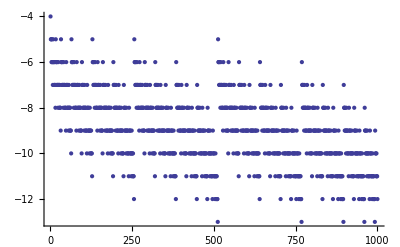

```mathematica
ListPlot[Table[Sum[IntegerExponent[2 k,2],{k,2j-2}]-4j,{j,1000}]]
```

```mathematica
m[k_]:=2IntegerExponent[k,4]+Switch[Mod[k/4^IntegerExponent[k,4],4],1,1,2,2,3,1]
```

```mathematica
Sort[Flatten[Table[(2^(n+3)-8)j-(2^(n+2)+2n-3)+2Sum[IntegerExponent[2 k,2],{k,2j-2}],{n,1,8},{j,1,8}]]]
```

{1,7,15,21,31,37,45,51,63,69,77,83,93,99,107,113,133,147,163,177,195,209,225,239,275,305,337,367,401,431,463,493,561,623,687,749,815,877,941,1003,1135,1261,1389,1515,1645,1771,1899,2285,2539,2795,3049,3307,3561,3817,4587,5097,5609,6633,7143,7655,9193,11239,13287,15333}

```mathematica
Table[(2^(n+3)-8)j-(2^(n+2)+2n-3)+2Sum[IntegerExponent[2 k,2],{k,2j-2}],{j,1,256},{n,1,10}]//MatrixForm
```

(1 | 7 | 21 | 51 | 113 | 239 | 493 | 1003 | 2025 | 4071
15 | 37 | 83 | 177 | 367 | 749 | 1515 | 3049 | 6119 | 12261
31 | 69 | 147 | 305 | 623 | 1261 | 2539 | 5097 | 10215 | 20453
45 | 99 | 209 | 431 | 877 | 1771 | 3561 | 7143 | 14309 | 28643
63 | 133 | 275 | 561 | 1135 | 2285 | 4587 | 9193 | 18407 | 36837
77 | 163 | 337 | 687 | 1389 | 2795 | 5609 | 11239 | 22501 | 45027
93 | 195 | 401 | 815 | 1645 | 3307 | 6633 | 13287 | 26597 | 53219
107 | 225 | 463 | 941 | 1899 | 3817 | 7655 | 15333 | 30691 | 61409
127 | 261 | 531 | 1073 | 2159 | 4333 | 8683 | 17385 | 34791 | 69605
141 | 291 | 593 | 1199 | 2413 | 4843 | 9705 | 19431 | 38885 | 77795
157 | 323 | 657 | 1327 | 2669 | 5355 | 10729 | 21479 | 42981 | 85987
171 | 353 | 719 | 1453 | 2923 | 5865 | 11751 | 23525 | 47075 | 94177
189 | 387 | 785 | 1583 | 3181 | 6379 | 12777 | 25575 | 51173 | 102371
203 | 417 | 847 | 1709 | 3435 | 6889 | 13799 | 27621 | 55267 | 110561
219 | 449 | 911 | 1837 | 3691 | 7401 | 14823 | 29669 | 59363 | 118753
233 | 479 | 973 | 1963 | 3945 | 7911 | 15845 | 31715 | 63457 | 126943
255 | 517 | 1043 | 2097 | 4207 | 8429 | 16875 | 33769 | 67559 | 135141
269 | 547 | 1105 | 2223 | 4461 | 8939 | 17897 | 35815 | 71653 | 143331
285 | 579 | 1169 | 2351 | 4717 | 9451 | 18921 | 37863 | 75749 | 151523
299 | 609 | 1231 | 2477 | 4971 | 9961 | 19943 | 39909 | 79843 | 159713
317 | 643 | 1297 | 2607 | 5229 | 10475 | 20969 | 41959 | 83941 | 167907
331 | 673 | 1359 | 2733 | 5483 | 10985 | 21991 | 44005 | 88035 | 176097
347 | 705 | 1423 | 2861 | 5739 | 11497 | 23015 | 46053 | 92131 | 184289
361 | 735 | 1485 | 2987 | 5993 | 12007 | 24037 | 48099 | 96225 | 192479
381 | 771 | 1553 | 3119 | 6253 | 12523 | 25065 | 50151 | 100325 | 200675
395 | 801 | 1615 | 3245 | 6507 | 13033 | 26087 | 52197 | 104419 | 208865
411 | 833 | 1679 | 3373 | 6763 | 13545 | 27111 | 54245 | 108515 | 217057
425 | 863 | 1741 | 3499 | 7017 | 14055 | 28133 | 56291 | 112609 | 225247
443 | 897 | 1807 | 3629 | 7275 | 14569 | 29159 | 58341 | 116707 | 233441
457 | 927 | 1869 | 3755 | 7529 | 15079 | 30181 | 60387 | 120801 | 241631
473 | 959 | 1933 | 3883 | 7785 | 15591 | 31205 | 62435 | 124897 | 249823
487 | 989 | 1995 | 4009 | 8039 | 16101 | 32227 | 64481 | 128991 | 258013
511 | 1029 | 2067 | 4145 | 8303 | 16621 | 33259 | 66537 | 133095 | 266213
525 | 1059 | 2129 | 4271 | 8557 | 17131 | 34281 | 68583 | 137189 | 274403
541 | 1091 | 2193 | 4399 | 8813 | 17643 | 35305 | 70631 | 141285 | 282595
555 | 1121 | 2255 | 4525 | 9067 | 18153 | 36327 | 72677 | 145379 | 290785
573 | 1155 | 2321 | 4655 | 9325 | 18667 | 37353 | 74727 | 149477 | 298979
587 | 1185 | 2383 | 4781 | 9579 | 19177 | 38375 | 76773 | 153571 | 307169
603 | 1217 | 2447 | 4909 | 9835 | 19689 | 39399 | 78821 | 157667 | 315361
617 | 1247 | 2509 | 5035 | 10089 | 20199 | 40421 | 80867 | 161761 | 323551
637 | 1283 | 2577 | 5167 | 10349 | 20715 | 41449 | 82919 | 165861 | 331747
651 | 1313 | 2639 | 5293 | 10603 | 21225 | 42471 | 84965 | 169955 | 339937
667 | 1345 | 2703 | 5421 | 10859 | 21737 | 43495 | 87013 | 174051 | 348129
681 | 1375 | 2765 | 5547 | 11113 | 22247 | 44517 | 89059 | 178145 | 356319
699 | 1409 | 2831 | 5677 | 11371 | 22761 | 45543 | 91109 | 182243 | 364513
713 | 1439 | 2893 | 5803 | 11625 | 23271 | 46565 | 93155 | 186337 | 372703
729 | 1471 | 2957 | 5931 | 11881 | 23783 | 47589 | 95203 | 190433 | 380895
743 | 1501 | 3019 | 6057 | 12135 | 24293 | 48611 | 97249 | 194527 | 389085
765 | 1539 | 3089 | 6191 | 12397 | 24811 | 49641 | 99303 | 198629 | 397283
779 | 1569 | 3151 | 6317 | 12651 | 25321 | 50663 | 101349 | 202723 | 405473
795 | 1601 | 3215 | 6445 | 12907 | 25833 | 51687 | 103397 | 206819 | 413665
809 | 1631 | 3277 | 6571 | 13161 | 26343 | 52709 | 105443 | 210913 | 421855
827 | 1665 | 3343 | 6701 | 13419 | 26857 | 53735 | 107493 | 215011 | 430049
841 | 1695 | 3405 | 6827 | 13673 | 27367 | 54757 | 109539 | 219105 | 438239
857 | 1727 | 3469 | 6955 | 13929 | 27879 | 55781 | 111587 | 223201 | 446431
871 | 1757 | 3531 | 7081 | 14183 | 28389 | 56803 | 113633 | 227295 | 454621
891 | 1793 | 3599 | 7213 | 14443 | 28905 | 57831 | 115685 | 231395 | 462817
905 | 1823 | 3661 | 7339 | 14697 | 29415 | 58853 | 117731 | 235489 | 471007
921 | 1855 | 3725 | 7467 | 14953 | 29927 | 59877 | 119779 | 239585 | 479199
935 | 1885 | 3787 | 7593 | 15207 | 30437 | 60899 | 121825 | 243679 | 487389
953 | 1919 | 3853 | 7723 | 15465 | 30951 | 61925 | 123875 | 247777 | 495583
967 | 1949 | 3915 | 7849 | 15719 | 31461 | 62947 | 125921 | 251871 | 503773
983 | 1981 | 3979 | 7977 | 15975 | 31973 | 63971 | 127969 | 255967 | 511965
997 | 2011 | 4041 | 8103 | 16229 | 32483 | 64993 | 130015 | 260061 | 520155
1023 | 2053 | 4115 | 8241 | 16495 | 33005 | 66027 | 132073 | 264167 | 528357
1037 | 2083 | 4177 | 8367 | 16749 | 33515 | 67049 | 134119 | 268261 | 536547
1053 | 2115 | 4241 | 8495 | 17005 | 34027 | 68073 | 136167 | 272357 | 544739
1067 | 2145 | 4303 | 8621 | 17259 | 34537 | 69095 | 138213 | 276451 | 552929
1085 | 2179 | 4369 | 8751 | 17517 | 35051 | 70121 | 140263 | 280549 | 561123
1099 | 2209 | 4431 | 8877 | 17771 | 35561 | 71143 | 142309 | 284643 | 569313
1115 | 2241 | 4495 | 9005 | 18027 | 36073 | 72167 | 144357 | 288739 | 577505
1129 | 2271 | 4557 | 9131 | 18281 | 36583 | 73189 | 146403 | 292833 | 585695
1149 | 2307 | 4625 | 9263 | 18541 | 37099 | 74217 | 148455 | 296933 | 593891
1163 | 2337 | 4687 | 9389 | 18795 | 37609 | 75239 | 150501 | 301027 | 602081
1179 | 2369 | 4751 | 9517 | 19051 | 38121 | 76263 | 152549 | 305123 | 610273
1193 | 2399 | 4813 | 9643 | 19305 | 38631 | 77285 | 154595 | 309217 | 618463
1211 | 2433 | 4879 | 9773 | 19563 | 39145 | 78311 | 156645 | 313315 | 626657
1225 | 2463 | 4941 | 9899 | 19817 | 39655 | 79333 | 158691 | 317409 | 634847
1241 | 2495 | 5005 | 10027 | 20073 | 40167 | 80357 | 160739 | 321505 | 643039
1255 | 2525 | 5067 | 10153 | 20327 | 40677 | 81379 | 162785 | 325599 | 651229
1277 | 2563 | 5137 | 10287 | 20589 | 41195 | 82409 | 164839 | 329701 | 659427
1291 | 2593 | 5199 | 10413 | 20843 | 41705 | 83431 | 166885 | 333795 | 667617
1307 | 2625 | 5263 | 10541 | 21099 | 42217 | 84455 | 168933 | 337891 | 675809
1321 | 2655 | 5325 | 10667 | 21353 | 42727 | 85477 | 170979 | 341985 | 683999
1339 | 2689 | 5391 | 10797 | 21611 | 43241 | 86503 | 173029 | 346083 | 692193
1353 | 2719 | 5453 | 10923 | 21865 | 43751 | 87525 | 175075 | 350177 | 700383
1369 | 2751 | 5517 | 11051 | 22121 | 44263 | 88549 | 177123 | 354273 | 708575
1383 | 2781 | 5579 | 11177 | 22375 | 44773 | 89571 | 179169 | 358367 | 716765
1403 | 2817 | 5647 | 11309 | 22635 | 45289 | 90599 | 181221 | 362467 | 724961
1417 | 2847 | 5709 | 11435 | 22889 | 45799 | 91621 | 183267 | 366561 | 733151
1433 | 2879 | 5773 | 11563 | 23145 | 46311 | 92645 | 185315 | 370657 | 741343
1447 | 2909 | 5835 | 11689 | 23399 | 46821 | 93667 | 187361 | 374751 | 749533
1465 | 2943 | 5901 | 11819 | 23657 | 47335 | 94693 | 189411 | 378849 | 757727
1479 | 2973 | 5963 | 11945 | 23911 | 47845 | 95715 | 191457 | 382943 | 765917
1495 | 3005 | 6027 | 12073 | 24167 | 48357 | 96739 | 193505 | 387039 | 774109
1509 | 3035 | 6089 | 12199 | 24421 | 48867 | 97761 | 195551 | 391133 | 782299
1533 | 3075 | 6161 | 12335 | 24685 | 49387 | 98793 | 197607 | 395237 | 790499
1547 | 3105 | 6223 | 12461 | 24939 | 49897 | 99815 | 199653 | 399331 | 798689
1563 | 3137 | 6287 | 12589 | 25195 | 50409 | 100839 | 201701 | 403427 | 806881
1577 | 3167 | 6349 | 12715 | 25449 | 50919 | 101861 | 203747 | 407521 | 815071
1595 | 3201 | 6415 | 12845 | 25707 | 51433 | 102887 | 205797 | 411619 | 823265
1609 | 3231 | 6477 | 12971 | 25961 | 51943 | 103909 | 207843 | 415713 | 831455
1625 | 3263 | 6541 | 13099 | 26217 | 52455 | 104933 | 209891 | 419809 | 839647
1639 | 3293 | 6603 | 13225 | 26471 | 52965 | 105955 | 211937 | 423903 | 847837
1659 | 3329 | 6671 | 13357 | 26731 | 53481 | 106983 | 213989 | 428003 | 856033
1673 | 3359 | 6733 | 13483 | 26985 | 53991 | 108005 | 216035 | 432097 | 864223
1689 | 3391 | 6797 | 13611 | 27241 | 54503 | 109029 | 218083 | 436193 | 872415
1703 | 3421 | 6859 | 13737 | 27495 | 55013 | 110051 | 220129 | 440287 | 880605
1721 | 3455 | 6925 | 13867 | 27753 | 55527 | 111077 | 222179 | 444385 | 888799
1735 | 3485 | 6987 | 13993 | 28007 | 56037 | 112099 | 224225 | 448479 | 896989
1751 | 3517 | 7051 | 14121 | 28263 | 56549 | 113123 | 226273 | 452575 | 905181
1765 | 3547 | 7113 | 14247 | 28517 | 57059 | 114145 | 228319 | 456669 | 913371
1787 | 3585 | 7183 | 14381 | 28779 | 57577 | 115175 | 230373 | 460771 | 921569
1801 | 3615 | 7245 | 14507 | 29033 | 58087 | 116197 | 232419 | 464865 | 929759
1817 | 3647 | 7309 | 14635 | 29289 | 58599 | 117221 | 234467 | 468961 | 937951
1831 | 3677 | 7371 | 14761 | 29543 | 59109 | 118243 | 236513 | 473055 | 946141
1849 | 3711 | 7437 | 14891 | 29801 | 59623 | 119269 | 238563 | 477153 | 954335
1863 | 3741 | 7499 | 15017 | 30055 | 60133 | 120291 | 240609 | 481247 | 962525
1879 | 3773 | 7563 | 15145 | 30311 | 60645 | 121315 | 242657 | 485343 | 970717
1893 | 3803 | 7625 | 15271 | 30565 | 61155 | 122337 | 244703 | 489437 | 978907
1913 | 3839 | 7693 | 15403 | 30825 | 61671 | 123365 | 246755 | 493537 | 987103
1927 | 3869 | 7755 | 15529 | 31079 | 62181 | 124387 | 248801 | 497631 | 995293
1943 | 3901 | 7819 | 15657 | 31335 | 62693 | 125411 | 250849 | 501727 | 1003485
1957 | 3931 | 7881 | 15783 | 31589 | 63203 | 126433 | 252895 | 505821 | 1011675
1975 | 3965 | 7947 | 15913 | 31847 | 63717 | 127459 | 254945 | 509919 | 1019869
1989 | 3995 | 8009 | 16039 | 32101 | 64227 | 128481 | 256991 | 514013 | 1028059
2005 | 4027 | 8073 | 16167 | 32357 | 64739 | 129505 | 259039 | 518109 | 1036251
2019 | 4057 | 8135 | 16293 | 32611 | 65249 | 130527 | 261085 | 522203 | 1044441
2047 | 4101 | 8211 | 16433 | 32879 | 65773 | 131563 | 263145 | 526311 | 1052645
2061 | 4131 | 8273 | 16559 | 33133 | 66283 | 132585 | 265191 | 530405 | 1060835
2077 | 4163 | 8337 | 16687 | 33389 | 66795 | 133609 | 267239 | 534501 | 1069027
2091 | 4193 | 8399 | 16813 | 33643 | 67305 | 134631 | 269285 | 538595 | 1077217
2109 | 4227 | 8465 | 16943 | 33901 | 67819 | 135657 | 271335 | 542693 | 1085411
2123 | 4257 | 8527 | 17069 | 34155 | 68329 | 136679 | 273381 | 546787 | 1093601
2139 | 4289 | 8591 | 17197 | 34411 | 68841 | 137703 | 275429 | 550883 | 1101793
2153 | 4319 | 8653 | 17323 | 34665 | 69351 | 138725 | 277475 | 554977 | 1109983
2173 | 4355 | 8721 | 17455 | 34925 | 69867 | 139753 | 279527 | 559077 | 1118179
2187 | 4385 | 8783 | 17581 | 35179 | 70377 | 140775 | 281573 | 563171 | 1126369
2203 | 4417 | 8847 | 17709 | 35435 | 70889 | 141799 | 283621 | 567267 | 1134561
2217 | 4447 | 8909 | 17835 | 35689 | 71399 | 142821 | 285667 | 571361 | 1142751
2235 | 4481 | 8975 | 17965 | 35947 | 71913 | 143847 | 287717 | 575459 | 1150945
2249 | 4511 | 9037 | 18091 | 36201 | 72423 | 144869 | 289763 | 579553 | 1159135
2265 | 4543 | 9101 | 18219 | 36457 | 72935 | 145893 | 291811 | 583649 | 1167327
2279 | 4573 | 9163 | 18345 | 36711 | 73445 | 146915 | 293857 | 587743 | 1175517
2301 | 4611 | 9233 | 18479 | 36973 | 73963 | 147945 | 295911 | 591845 | 1183715
2315 | 4641 | 9295 | 18605 | 37227 | 74473 | 148967 | 297957 | 595939 | 1191905
2331 | 4673 | 9359 | 18733 | 37483 | 74985 | 149991 | 300005 | 600035 | 1200097
2345 | 4703 | 9421 | 18859 | 37737 | 75495 | 151013 | 302051 | 604129 | 1208287
2363 | 4737 | 9487 | 18989 | 37995 | 76009 | 152039 | 304101 | 608227 | 1216481
2377 | 4767 | 9549 | 19115 | 38249 | 76519 | 153061 | 306147 | 612321 | 1224671
2393 | 4799 | 9613 | 19243 | 38505 | 77031 | 154085 | 308195 | 616417 | 1232863
2407 | 4829 | 9675 | 19369 | 38759 | 77541 | 155107 | 310241 | 620511 | 1241053
2427 | 4865 | 9743 | 19501 | 39019 | 78057 | 156135 | 312293 | 624611 | 1249249
2441 | 4895 | 9805 | 19627 | 39273 | 78567 | 157157 | 314339 | 628705 | 1257439
2457 | 4927 | 9869 | 19755 | 39529 | 79079 | 158181 | 316387 | 632801 | 1265631
2471 | 4957 | 9931 | 19881 | 39783 | 79589 | 159203 | 318433 | 636895 | 1273821
2489 | 4991 | 9997 | 20011 | 40041 | 80103 | 160229 | 320483 | 640993 | 1282015
2503 | 5021 | 10059 | 20137 | 40295 | 80613 | 161251 | 322529 | 645087 | 1290205
2519 | 5053 | 10123 | 20265 | 40551 | 81125 | 162275 | 324577 | 649183 | 1298397
2533 | 5083 | 10185 | 20391 | 40805 | 81635 | 163297 | 326623 | 653277 | 1306587
2557 | 5123 | 10257 | 20527 | 41069 | 82155 | 164329 | 328679 | 657381 | 1314787
2571 | 5153 | 10319 | 20653 | 41323 | 82665 | 165351 | 330725 | 661475 | 1322977
2587 | 5185 | 10383 | 20781 | 41579 | 83177 | 166375 | 332773 | 665571 | 1331169
2601 | 5215 | 10445 | 20907 | 41833 | 83687 | 167397 | 334819 | 669665 | 1339359
2619 | 5249 | 10511 | 21037 | 42091 | 84201 | 168423 | 336869 | 673763 | 1347553
2633 | 5279 | 10573 | 21163 | 42345 | 84711 | 169445 | 338915 | 677857 | 1355743
2649 | 5311 | 10637 | 21291 | 42601 | 85223 | 170469 | 340963 | 681953 | 1363935
2663 | 5341 | 10699 | 21417 | 42855 | 85733 | 171491 | 343009 | 686047 | 1372125
2683 | 5377 | 10767 | 21549 | 43115 | 86249 | 172519 | 345061 | 690147 | 1380321
2697 | 5407 | 10829 | 21675 | 43369 | 86759 | 173541 | 347107 | 694241 | 1388511
2713 | 5439 | 10893 | 21803 | 43625 | 87271 | 174565 | 349155 | 698337 | 1396703
2727 | 5469 | 10955 | 21929 | 43879 | 87781 | 175587 | 351201 | 702431 | 1404893
2745 | 5503 | 11021 | 22059 | 44137 | 88295 | 176613 | 353251 | 706529 | 1413087
2759 | 5533 | 11083 | 22185 | 44391 | 88805 | 177635 | 355297 | 710623 | 1421277
2775 | 5565 | 11147 | 22313 | 44647 | 89317 | 178659 | 357345 | 714719 | 1429469
2789 | 5595 | 11209 | 22439 | 44901 | 89827 | 179681 | 359391 | 718813 | 1437659
2811 | 5633 | 11279 | 22573 | 45163 | 90345 | 180711 | 361445 | 722915 | 1445857
2825 | 5663 | 11341 | 22699 | 45417 | 90855 | 181733 | 363491 | 727009 | 1454047
2841 | 5695 | 11405 | 22827 | 45673 | 91367 | 182757 | 365539 | 731105 | 1462239
2855 | 5725 | 11467 | 22953 | 45927 | 91877 | 183779 | 367585 | 735199 | 1470429
2873 | 5759 | 11533 | 23083 | 46185 | 92391 | 184805 | 369635 | 739297 | 1478623
2887 | 5789 | 11595 | 23209 | 46439 | 92901 | 185827 | 371681 | 743391 | 1486813
2903 | 5821 | 11659 | 23337 | 46695 | 93413 | 186851 | 373729 | 747487 | 1495005
2917 | 5851 | 11721 | 23463 | 46949 | 93923 | 187873 | 375775 | 751581 | 1503195
2937 | 5887 | 11789 | 23595 | 47209 | 94439 | 188901 | 377827 | 755681 | 1511391
2951 | 5917 | 11851 | 23721 | 47463 | 94949 | 189923 | 379873 | 759775 | 1519581
2967 | 5949 | 11915 | 23849 | 47719 | 95461 | 190947 | 381921 | 763871 | 1527773
2981 | 5979 | 11977 | 23975 | 47973 | 95971 | 191969 | 383967 | 767965 | 1535963
2999 | 6013 | 12043 | 24105 | 48231 | 96485 | 192995 | 386017 | 772063 | 1544157
3013 | 6043 | 12105 | 24231 | 48485 | 96995 | 194017 | 388063 | 776157 | 1552347
3029 | 6075 | 12169 | 24359 | 48741 | 97507 | 195041 | 390111 | 780253 | 1560539
3043 | 6105 | 12231 | 24485 | 48995 | 98017 | 196063 | 392157 | 784347 | 1568729
3069 | 6147 | 12305 | 24623 | 49261 | 98539 | 197097 | 394215 | 788453 | 1576931
3083 | 6177 | 12367 | 24749 | 49515 | 99049 | 198119 | 396261 | 792547 | 1585121
3099 | 6209 | 12431 | 24877 | 49771 | 99561 | 199143 | 398309 | 796643 | 1593313
3113 | 6239 | 12493 | 25003 | 50025 | 100071 | 200165 | 400355 | 800737 | 1601503
3131 | 6273 | 12559 | 25133 | 50283 | 100585 | 201191 | 402405 | 804835 | 1609697
3145 | 6303 | 12621 | 25259 | 50537 | 101095 | 202213 | 404451 | 808929 | 1617887
3161 | 6335 | 12685 | 25387 | 50793 | 101607 | 203237 | 406499 | 813025 | 1626079
3175 | 6365 | 12747 | 25513 | 51047 | 102117 | 204259 | 408545 | 817119 | 1634269
3195 | 6401 | 12815 | 25645 | 51307 | 102633 | 205287 | 410597 | 821219 | 1642465
3209 | 6431 | 12877 | 25771 | 51561 | 103143 | 206309 | 412643 | 825313 | 1650655
3225 | 6463 | 12941 | 25899 | 51817 | 103655 | 207333 | 414691 | 829409 | 1658847
3239 | 6493 | 13003 | 26025 | 52071 | 104165 | 208355 | 416737 | 833503 | 1667037
3257 | 6527 | 13069 | 26155 | 52329 | 104679 | 209381 | 418787 | 837601 | 1675231
3271 | 6557 | 13131 | 26281 | 52583 | 105189 | 210403 | 420833 | 841695 | 1683421
3287 | 6589 | 13195 | 26409 | 52839 | 105701 | 211427 | 422881 | 845791 | 1691613
3301 | 6619 | 13257 | 26535 | 53093 | 106211 | 212449 | 424927 | 849885 | 1699803
3323 | 6657 | 13327 | 26669 | 53355 | 106729 | 213479 | 426981 | 853987 | 1708001
3337 | 6687 | 13389 | 26795 | 53609 | 107239 | 214501 | 429027 | 858081 | 1716191
3353 | 6719 | 13453 | 26923 | 53865 | 107751 | 215525 | 431075 | 862177 | 1724383
3367 | 6749 | 13515 | 27049 | 54119 | 108261 | 216547 | 433121 | 866271 | 1732573
3385 | 6783 | 13581 | 27179 | 54377 | 108775 | 217573 | 435171 | 870369 | 1740767
3399 | 6813 | 13643 | 27305 | 54631 | 109285 | 218595 | 437217 | 874463 | 1748957
3415 | 6845 | 13707 | 27433 | 54887 | 109797 | 219619 | 439265 | 878559 | 1757149
3429 | 6875 | 13769 | 27559 | 55141 | 110307 | 220641 | 441311 | 882653 | 1765339
3449 | 6911 | 13837 | 27691 | 55401 | 110823 | 221669 | 443363 | 886753 | 1773535
3463 | 6941 | 13899 | 27817 | 55655 | 111333 | 222691 | 445409 | 890847 | 1781725
3479 | 6973 | 13963 | 27945 | 55911 | 111845 | 223715 | 447457 | 894943 | 1789917
3493 | 7003 | 14025 | 28071 | 56165 | 112355 | 224737 | 449503 | 899037 | 1798107
3511 | 7037 | 14091 | 28201 | 56423 | 112869 | 225763 | 451553 | 903135 | 1806301
3525 | 7067 | 14153 | 28327 | 56677 | 113379 | 226785 | 453599 | 907229 | 1814491
3541 | 7099 | 14217 | 28455 | 56933 | 113891 | 227809 | 455647 | 911325 | 1822683
3555 | 7129 | 14279 | 28581 | 57187 | 114401 | 228831 | 457693 | 915419 | 1830873
3579 | 7169 | 14351 | 28717 | 57451 | 114921 | 229863 | 459749 | 919523 | 1839073
3593 | 7199 | 14413 | 28843 | 57705 | 115431 | 230885 | 461795 | 923617 | 1847263
3609 | 7231 | 14477 | 28971 | 57961 | 115943 | 231909 | 463843 | 927713 | 1855455
3623 | 7261 | 14539 | 29097 | 58215 | 116453 | 232931 | 465889 | 931807 | 1863645
3641 | 7295 | 14605 | 29227 | 58473 | 116967 | 233957 | 467939 | 935905 | 1871839
3655 | 7325 | 14667 | 29353 | 58727 | 117477 | 234979 | 469985 | 939999 | 1880029
3671 | 7357 | 14731 | 29481 | 58983 | 117989 | 236003 | 472033 | 944095 | 1888221
3685 | 7387 | 14793 | 29607 | 59237 | 118499 | 237025 | 474079 | 948189 | 1896411
3705 | 7423 | 14861 | 29739 | 59497 | 119015 | 238053 | 476131 | 952289 | 1904607
3719 | 7453 | 14923 | 29865 | 59751 | 119525 | 239075 | 478177 | 956383 | 1912797
3735 | 7485 | 14987 | 29993 | 60007 | 120037 | 240099 | 480225 | 960479 | 1920989
3749 | 7515 | 15049 | 30119 | 60261 | 120547 | 241121 | 482271 | 964573 | 1929179
3767 | 7549 | 15115 | 30249 | 60519 | 121061 | 242147 | 484321 | 968671 | 1937373
3781 | 7579 | 15177 | 30375 | 60773 | 121571 | 243169 | 486367 | 972765 | 1945563
3797 | 7611 | 15241 | 30503 | 61029 | 122083 | 244193 | 488415 | 976861 | 1953755
3811 | 7641 | 15303 | 30629 | 61283 | 122593 | 245215 | 490461 | 980955 | 1961945
3833 | 7679 | 15373 | 30763 | 61545 | 123111 | 246245 | 492515 | 985057 | 1970143
3847 | 7709 | 15435 | 30889 | 61799 | 123621 | 247267 | 494561 | 989151 | 1978333
3863 | 7741 | 15499 | 31017 | 62055 | 124133 | 248291 | 496609 | 993247 | 1986525
3877 | 7771 | 15561 | 31143 | 62309 | 124643 | 249313 | 498655 | 997341 | 1994715
3895 | 7805 | 15627 | 31273 | 62567 | 125157 | 250339 | 500705 | 1001439 | 2002909
3909 | 7835 | 15689 | 31399 | 62821 | 125667 | 251361 | 502751 | 1005533 | 2011099
3925 | 7867 | 15753 | 31527 | 63077 | 126179 | 252385 | 504799 | 1009629 | 2019291
3939 | 7897 | 15815 | 31653 | 63331 | 126689 | 253407 | 506845 | 1013723 | 2027481
3959 | 7933 | 15883 | 31785 | 63591 | 127205 | 254435 | 508897 | 1017823 | 2035677
3973 | 7963 | 15945 | 31911 | 63845 | 127715 | 255457 | 510943 | 1021917 | 2043867
3989 | 7995 | 16009 | 32039 | 64101 | 128227 | 256481 | 512991 | 1026013 | 2052059
4003 | 8025 | 16071 | 32165 | 64355 | 128737 | 257503 | 515037 | 1030107 | 2060249
4021 | 8059 | 16137 | 32295 | 64613 | 129251 | 258529 | 517087 | 1034205 | 2068443
4035 | 8089 | 16199 | 32421 | 64867 | 129761 | 259551 | 519133 | 1038299 | 2076633
4051 | 8121 | 16263 | 32549 | 65123 | 130273 | 260575 | 521181 | 1042395 | 2084825
4065 | 8151 | 16325 | 32675 | 65377 | 130783 | 261597 | 523227 | 1046489 | 2093015)

```mathematica
Sort[Flatten[Table[(2^(n+3)-8)j-(2^(n+2)+2n-3)+2Sum[IntegerExponent[2 k,2],{k,2j-2}],{n,1,6},{j,1,30}]]]
```

{1,7,15,21,31,37,45,51,63,69,77,83,93,99,107,113,127,133,141,147,157,163,171,177,189,195,203,209,219,225,233,239,255,261,269,275,285,291,299,305,317,323,331,337,347,353,361,367,381,387,395,401,411,417,425,431,443,449,457,463,479,517,531,547,561,579,593,609,623,643,657,673,687,705,719,735,749,771,785,801,815,833,847,863,877,897,911,927,941,973,1043,1073,1105,1135,1169,1199,1231,1261,1297,1327,1359,1389,1423,1453,1485,1553,1583,1615,1645,1679,1709,1741,1771,1807,1837,1869,1899,1963,2097,2159,2223,2285,2351,2413,2477,2607,2669,2733,2795,2861,2923,2987,3119,3181,3245,3307,3373,3435,3499,3629,3691,3755,3817,3945,4207,4333,4461,4717,4843,4971,5229,5355,5483,5739,5865,5993,6253,6379,6507,6763,6889,7017,7275,7401,7529,7911,8429,8939,9451,9961,10475,10985,11497,12007,12523,13033,13545,14055,14569,15079}

```mathematica
Table[m[k],{k,5000}]==Table[IntegerExponent[2 k,2],{k,5000}]
```

True

```mathematica
Sum[IntegerExponent[2 k,2],{k,2j-2}]
```

∑_k^(-2+2 j) IntegerExponent[2 k,2]

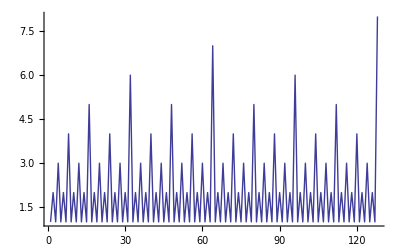

```mathematica
ListPlot[Table[IntegerExponent[2 k,2],{k,128}],Joined->True]
```

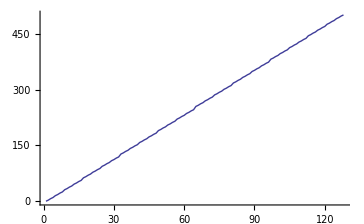

```mathematica
ListPlot[Table[Sum[IntegerExponent[2 k,2],{k,2j-2}],{j,128}],Joined->True]
```

```mathematica
list1=seqPos[Base4SEvolution[2,3276,5000],{4,3,4,6,3,1}]
```

{1,15,31,45,63,77,93,107,127,141,157,171,189,203,219,233,255,269,285,299,317,331,347,361,381,395,411,425,443,457,473,487,511,525,541,555,573,587,603,617,637,651,667,681,699,713,729,743,765,779,795,809,827,841,857,871,891,905,921,935,953,967,983,997,1023,1037,1053,1067,1085,1099,1115,1129,1149,1163,1179,1193,1211,1225,1241,1255,1277,1291,1307,1321,1339,1353,1369,1383,1403,1417,1433,1447,1465,1479,1495,1509,1533,1547,1563,1577,1595,1609,1625,1639,1659,1673,1689,1703,1721,1735,1751,1765,1787,1801,1817,1831,1849,1863,1879,1893,1913,1927,1943,1957,1975,1989,2005,2019,2047,2061,2077,2091,2109,2123,2139,2153,2173,2187,2203,2217,2235,2249,2265,2279,2301,2315,2331,2345,2363,2377,2393,2407,2427,2441,2457,2471,2489,2503,2519,2533,2557,2571,2587,2601,2619,2633,2649,2663,2683,2697,2713,2727,2745,2759,2775,2789,2811,2825,2841,2855,2873,2887,2903,2917,2937,2951,2967,2981,2999,3013,3029,3043,3069,3083,3099,3113,3131,3145,3161,3175,3195,3209,3225,3239,3257,3271,3287,3301,3323,3337,3353,3367,3385,3399,3415,3429,3449,3463,3479,3493,3511,3525,3541,3555,3579,3593,3609,3623,3641,3655,3671,3685,3705,3719,3735,3749,3767,3781,3797,3811,3833,3847,3863,3877,3895,3909,3925,3939,3959,3973,3989,4003,4021,4035,4051,4065,4095,4109,4125,4139,4157,4171,4187,4201,4221,4235,4251,4265,4283,4297,4313,4327,4349,4363,4379,4393,4411,4425,4441,4455,4475,4489,4505,4519,4537,4551,4567,4581,4605,4619,4635,4649,4667,4681,4697,4711,4731,4745,4761,4775,4793,4807,4823,4837,4859,4873,4889,4903,4921,4935,4951,4965,4985}

```mathematica
Table[4(2j-1)-3+2Sum[m[k],{k,2j-2}],{j,64}]
```

{1,15,31,45,63,77,93,107,127,141,157,171,189,203,219,233,255,269,285,299,317,331,347,361,381,395,411,425,443,457,473,487,511,525,541,555,573,587,603,617,637,651,667,681,699,713,729,743,765,779,795,809,827,841,857,871,891,905,921,935,953,967,983,997}

```mathematica
Table[4(2j+1)-3+2Sum[m[k],{k,2j}]-(4(2j-1)-3+2Sum[m[k],{k,2j-2}]),{j,64}]
```

{14,16,14,18,14,16,14,20,14,16,14,18,14,16,14,22,14,16,14,18,14,16,14,20,14,16,14,18,14,16,14,24,14,16,14,18,14,16,14,20,14,16,14,18,14,16,14,22,14,16,14,18,14,16,14,20,14,16,14,18,14,16,14,26}

```mathematica
Table[8+2Sum[m[k],{k,2j}]-2Sum[m[k],{k,2j-2}],{j,64}]
```

{14,16,14,18,14,16,14,20,14,16,14,18,14,16,14,22,14,16,14,18,14,16,14,20,14,16,14,18,14,16,14,24,14,16,14,18,14,16,14,20,14,16,14,18,14,16,14,22,14,16,14,18,14,16,14,20,14,16,14,18,14,16,14,26}

```mathematica
Table[4(2j+1)-3+2Sum[m[k],{k,2j}],{j,64}]
```

```mathematica
Differences[list1]
```

{14,16,14,18,14,16,14,20,14,16,14,18,14,16,14,22,14,16,14,18,14,16,14,20,14,16,14,18,14,16,14,24,14,16,14,18,14,16,14,20,14,16,14,18,14,16,14,22,14,16,14,18,14,16,14,20,14,16,14,18,14,16,14,26,14,16,14,18,14,16,14,20,14,16,14,18,14,16,14,22,14,16,14,18,14,16,14,20,14,16,14,18,14,16,14,24,14,16,14,18,14,16,14,20,14,16,14,18,14,16,14,22,14,16,14,18,14,16,14,20,14,16,14,18,14,16,14,28,14,16,14,18,14,16,14,20,14,16,14,18,14,16,14,22,14,16,14,18,14,16,14,20,14,16,14,18,14,16,14,24,14,16,14,18,14,16,14,20,14,16,14,18,14,16,14,22,14,16,14,18,14,16,14,20,14,16,14,18,14,16,14,26,14,16,14,18,14,16,14,20,14,16,14,18,14,16,14,22,14,16,14,18,14,16,14,20,14,16,14,18,14,16,14,24,14,16,14,18,14,16,14,20,14,16,14,18,14,16,14,22,14,16,14,18,14,16,14,20,14,16,14,18,14,16,14,30,14,16,14,18,14,16,14,20,14,16,14,18,14,16,14,22,14,16,14,18,14,16,14,20,14,16,14,18,14,16,14,24,14,16,14,18,14,16,14,20,14,16,14,18,14,16,14,22,14,16,14,18,14,16,14,20}

```mathematica
Table[10+2m[2j],{j,64}]
```

{14,16,14,18,14,16,14,20,14,16,14,18,14,16,14,22,14,16,14,18,14,16,14,20,14,16,14,18,14,16,14,24,14,16,14,18,14,16,14,20,14,16,14,18,14,16,14,22,14,16,14,18,14,16,14,20,14,16,14,18,14,16,14,26}

```mathematica
list2=seqPos[Base4SEvolution[2,3276,5000],{4,3,4,6,6,3,1,1}]
```

{7,37,69,99,133,163,195,225,261,291,323,353,387,417,449,479,517,547,579,609,643,673,705,735,771,801,833,863,897,927,959,989,1029,1059,1091,1121,1155,1185,1217,1247,1283,1313,1345,1375,1409,1439,1471,1501,1539,1569,1601,1631,1665,1695,1727,1757,1793,1823,1855,1885,1919,1949,1981,2011,2053,2083,2115,2145,2179,2209,2241,2271,2307,2337,2369,2399,2433,2463,2495,2525,2563,2593,2625,2655,2689,2719,2751,2781,2817,2847,2879,2909,2943,2973,3005,3035,3075,3105,3137,3167,3201,3231,3263,3293,3329,3359,3391,3421,3455,3485,3517,3547,3585,3615,3647,3677,3711,3741,3773,3803,3839,3869,3901,3931,3965,3995,4027,4057,4101,4131,4163,4193,4227,4257,4289,4319,4355,4385,4417,4447,4481,4511,4543,4573,4611,4641,4673,4703,4737,4767,4799,4829,4865,4895,4927,4957,4991}

```mathematica
Table[a j+b+2Sum[m[k],{k,2j-2}],{j,16}]
```

{a+b,6+2 a+b,14+3 a+b,20+4 a+b,30+5 a+b,36+6 a+b,44+7 a+b,50+8 a+b,62+9 a+b,68+10 a+b,76+11 a+b,82+12 a+b,92+13 a+b,98+14 a+b,106+15 a+b,112+16 a+b}

```mathematica
Solve[{a+b==21,6+2 a+b==83},{a,b}]
```

{{a→56,b→-35}}

```mathematica
Table[120j-69+2Sum[m[k],{k,2j-2}],{j,16}]
```

{51,177,305,431,561,687,815,941,1073,1199,1327,1453,1583,1709,1837,1963}

```mathematica
Differences[list2]
```

{30,32,30,34,30,32,30,36,30,32,30,34,30,32,30,38,30,32,30,34,30,32,30,36,30,32,30,34,30,32,30,40,30,32,30,34,30,32,30,36,30,32,30,34,30,32,30,38,30,32,30,34,30,32,30,36,30,32,30,34,30,32,30,42,30,32,30,34,30,32,30,36,30,32,30,34,30,32,30,38,30,32,30,34,30,32,30,36,30,32,30,34,30,32,30,40,30,32,30,34,30,32,30,36,30,32,30,34,30,32,30,38,30,32,30,34,30,32,30,36,30,32,30,34,30,32,30,44,30,32,30,34,30,32,30,36,30,32,30,34,30,32,30,38,30,32,30,34,30,32,30,36,30,32,30,34}

```mathematica
Table[10+16+2m[2j],{j,64}]
```

{30,32,30,34,30,32,30,36,30,32,30,34,30,32,30,38,30,32,30,34,30,32,30,36,30,32,30,34,30,32,30,40,30,32,30,34,30,32,30,36,30,32,30,34,30,32,30,38,30,32,30,34,30,32,30,36,30,32,30,34,30,32,30,42}

```mathematica
list3=seqPos[Base4SEvolution[2,3276,5000],{4,3,4,6,6,6,3,1,1,1}]
```

{21,83,147,209,275,337,401,463,531,593,657,719,785,847,911,973,1043,1105,1169,1231,1297,1359,1423,1485,1553,1615,1679,1741,1807,1869,1933,1995,2067,2129,2193,2255,2321,2383,2447,2509,2577,2639,2703,2765,2831,2893,2957,3019,3089,3151,3215,3277,3343,3405,3469,3531,3599,3661,3725,3787,3853,3915,3979,4041,4115,4177,4241,4303,4369,4431,4495,4557,4625,4687,4751,4813,4879,4941}

```mathematica
Differences[list3]
```

{62,64,62,66,62,64,62,68,62,64,62,66,62,64,62,70,62,64,62,66,62,64,62,68,62,64,62,66,62,64,62,72,62,64,62,66,62,64,62,68,62,64,62,66,62,64,62,70,62,64,62,66,62,64,62,68,62,64,62,66,62,64,62,74,62,64,62,66,62,64,62,68,62,64,62,66,62}

```mathematica
Table[10+48+2m[2j],{j,64}]
```

{62,64,62,66,62,64,62,68,62,64,62,66,62,64,62,70,62,64,62,66,62,64,62,68,62,64,62,66,62,64,62,72,62,64,62,66,62,64,62,68,62,64,62,66,62,64,62,70,62,64,62,66,62,64,62,68,62,64,62,66,62,64,62,74}

```mathematica
list4=seqPos[Base4SEvolution[2,3276,5000],{4,3,4,6,6,6,6,3,1,1,1,1}]
```

{51,177,305,431,561,687,815,941,1073,1199,1327,1453,1583,1709,1837,1963,2097,2223,2351,2477,2607,2733,2861,2987,3119,3245,3373,3499,3629,3755,3883,4009,4145,4271,4399,4525,4655,4781,4909}

```mathematica
Differences[list4]
```

{126,128,126,130,126,128,126,132,126,128,126,130,126,128,126,134,126,128,126,130,126,128,126,132,126,128,126,130,126,128,126,136,126,128,126,130,126,128}

```mathematica
Table[10+112+2m[2j],{j,64}]
```

{126,128,126,130,126,128,126,132,126,128,126,130,126,128,126,134,126,128,126,130,126,128,126,132,126,128,126,130,126,128,126,136,126,128,126,130,126,128,126,132,126,128,126,130,126,128,126,134,126,128,126,130,126,128,126,132,126,128,126,130,126,128,126,138}

```mathematica
list6=seqPos[Base4SEvolution[2,3276,5000],{4,3,4,6,6,6,6,6,6,3,1,1,1,1,1,1}]
```

{239,749,1261,1771,2285,2795,3307,3817,4333,4843}

```mathematica
list7=seqPos[Base4SEvolution[2,3276,5000],{4,3,4,6,6,6,6,6,6,6,3,1,1,1,1,1,1,1}]
```

{493,1515,2539,3561,4587}

```mathematica
FindSequenceFunction[{7,17,35,69,135,265,523,1037},m]
```

-3+2^(2+m)+2 m

```mathematica
Table[-5+2^(2+m)-2 m,{m,10}]
```

{1,7,21,51,113,239,493,1003,2025,4071}

```mathematica
Sum[2 (-3+2^(2+m)),{m,k}]
```

2 (-8+2^(3+k)-3 k)

```mathematica
m[k_]:=2IntegerExponent[k,4]+Switch[Mod[k/4^IntegerExponent[k,4],4],1,1,2,2,3,1]
```

```mathematica
Table[m[k],{k,200}]
```

{1,2,1,3,1,2,1,4,1,2,1,3,1,2,1,5,1,2,1,3,1,2,1,4,1,2,1,3,1,2,1,6,1,2,1,3,1,2,1,4,1,2,1,3,1,2,1,5,1,2,1,3,1,2,1,4,1,2,1,3,1,2,1,7,1,2,1,3,1,2,1,4,1,2,1,3,1,2,1,5,1,2,1,3,1,2,1,4,1,2,1,3,1,2,1,6,1,2,1,3,1,2,1,4,1,2,1,3,1,2,1,5,1,2,1,3,1,2,1,4,1,2,1,3,1,2,1,8,1,2,1,3,1,2,1,4,1,2,1,3,1,2,1,5,1,2,1,3,1,2,1,4,1,2,1,3,1,2,1,6,1,2,1,3,1,2,1,4,1,2,1,3,1,2,1,5,1,2,1,3,1,2,1,4,1,2,1,3,1,2,1,7,1,2,1,3,1,2,1,4}

```mathematica
Position[Table[m[k],{k,200}],1]
```

{{1},{3},{5},{7},{9},{11},{13},{15},{17},{19},{21},{23},{25},{27},{29},{31},{33},{35},{37},{39},{41},{43},{45},{47},{49},{51},{53},{55},{57},{59},{61},{63},{65},{67},{69},{71},{73},{75},{77},{79},{81},{83},{85},{87},{89},{91},{93},{95},{97},{99},{101},{103},{105},{107},{109},{111},{113},{115},{117},{119},{121},{123},{125},{127},{129},{131},{133},{135},{137},{139},{141},{143},{145},{147},{149},{151},{153},{155},{157},{159},{161},{163},{165},{167},{169},{171},{173},{175},{177},{179},{181},{183},{185},{187},{189},{191},{193},{195},{197},{199}}

```mathematica
Position[Table[m[k],{k,200}],2]
```

{{2},{6},{10},{14},{18},{22},{26},{30},{34},{38},{42},{46},{50},{54},{58},{62},{66},{70},{74},{78},{82},{86},{90},{94},{98},{102},{106},{110},{114},{118},{122},{126},{130},{134},{138},{142},{146},{150},{154},{158},{162},{166},{170},{174},{178},{182},{186},{190},{194},{198}}

```mathematica
Position[Table[m[k],{k,200}],3]
```

{{4},{12},{20},{28},{36},{44},{52},{60},{68},{76},{84},{92},{100},{108},{116},{124},{132},{140},{148},{156},{164},{172},{180},{188},{196}}

```mathematica
Position[Table[m[k],{k,200}],4]
```

{{8},{24},{40},{56},{72},{88},{104},{120},{136},{152},{168},{184},{200}}

```mathematica
seqPos[Base4SEvolution[2,3276,500],{4,3,4}]
```

{1,7,15,21,31,37,45,51,63,69,77,83,93,99,107,113,127,133,141,147,157,163,171,177,189,195,203,209,219,225,233,239,255,261,269,275,285,291,299,305,317,323,331,337,347,353,361,367,381,387,395,401,411,417,425,431,443,449,457,463,473,479,487,493}

```mathematica
Table[4j-3+2Sum[m[k],{k,j-1}],{j,64}]
```

{1,7,15,21,31,37,45,51,63,69,77,83,93,99,107,113,127,133,141,147,157,163,171,177,189,195,203,209,219,225,233,239,255,261,269,275,285,291,299,305,317,323,331,337,347,353,361,367,381,387,395,401,411,417,425,431,443,449,457,463,473,479,487,493}

```mathematica
Table[4j+2Sum[m[k],{k,j}],{j,64}]    (*donne la position du dernier 1 de chaque groupe 434666631111*)
```

{6,14,20,30,36,44,50,62,68,76,82,92,98,106,112,126,132,140,146,156,162,170,176,188,194,202,208,218,224,232,238,254,260,268,274,284,290,298,304,316,322,330,336,346,352,360,366,380,386,394,400,410,416,424,430,442,448,456,462,472,478,486,492,510}

```mathematica
Sum[IntegerExponent[k,4],{k,j}]
```

∑_k^j IntegerExponent[k,4]

```mathematica
Table[IntegerExponent[k,4],{k,4,300,4}]
```

{1,1,1,2,1,1,1,2,1,1,1,2,1,1,1,3,1,1,1,2,1,1,1,2,1,1,1,2,1,1,1,3,1,1,1,2,1,1,1,2,1,1,1,2,1,1,1,3,1,1,1,2,1,1,1,2,1,1,1,2,1,1,1,4,1,1,1,2,1,1,1,2,1,1,1}

```mathematica
Sort[Flatten[Table[(2^(m+3)-8)n-(2^(m+2)+2m-5)-2,{m,1,8,1},{n,1,8,1}]]]
```

{1,7,9,17,21,25,31,33,41,49,51,55,57,77,79,103,113,127,133,151,171,175,189,239,245,291,301,357,361,411,413,493,531,609,651,743,771,857,891,1003,1105,1247,1353,1509,1601,1751,1849,2255,2525,2759,3043,3263,3541,3767,4557,5083,5573,6589,7123,7605,9163,11203,13243,15283}

```mathematica
Table[list434[[2^j]],{j,8}]
```

{7,21,51,113,239,493,1003,2025}

```mathematica
Table[list434[[2^j+1]],{j,8}]
```

{15,31,63,127,255,511,1023,2047}

```mathematica
Table[list434[[2^j+2]],{j,8}]
```

{21,37,69,133,261,517,1029,2053}

```mathematica
Table[list434[[2^j+3]],{j,8}]
```

{31,45,77,141,269,525,1037,2061}

```mathematica
FindSequenceFunction[Table[list434[[2^j]],{j,8}],m]
```

-7+2^(3+m)-2 m

```mathematica
FindSequenceFunction[Table[list434[[2^j-1]],{j,8}],m]
```

-13+2^(3+m)-2 m

```mathematica
FindSequenceFunction[Table[list434[[2^j-2]],{j,2,8}],m]
```

-23+2^(4+m)-2 m

```mathematica
FindSequenceFunction[Table[list434[[2^j-3]],{j,2,8}],m]
```

-29+2^(4+m)-2 m

```mathematica
FindSequenceFunction[Table[list434[[2^j-4]],{j,3,10}],m]
```

-41+2^(5+m)-2 m

```mathematica
FindSequenceFunction[Table[list434[[2^j-5]],{j,3,10}],m]
```

-47+2^(5+m)-2 m

```mathematica
FindSequenceFunction[Table[list434[[2^j-6]],{j,3,10}],m]
```

-55+2^(5+m)-2 m

```mathematica
FunctionExpand[FindSequenceFunction[Table[list434[[2^j+3]],{j,8}],m]]
```

DifferenceRoot[Function[{y,n},{13-2 y[n]+y[1+n]==0,y[1]==31,y[2]==45}]][m]

```mathematica
RSolve[{a[m+1]-2a[m]==-13,a[1]==31},a[m],m]
```

{{a[m]→13+9 2^m}}

```mathematica
Table[13+9 2^m,{m,8}]
```

{31,49,85,157,301,589,1165,2317}

```mathematica
liste=Base4SEvolution[2,3276,20000];
```

```mathematica
l5={116,242,243,370,496,497,498,626,752,753,880,1006,1007,1008,1009,1138,1264,1265,1392,1518,1519,1520,1648,1774,1775,1902,2028,2029,2030,2031,2032,2162,2288,2289,2416,2542,2543,2544,2672,2798,2799,2926,3052,3053,3054,3055,3184,3310,3311,3438,3564,3565,3566,3694,3820,3821,3948,4074,4075,4076,4077,4078,4079,4210,4336,4337,4464,4590,4591,4592,4720,4846,4847,4974,5100,5101,5102,5103,5232,5358,5359,5486,5612,5613,5614,5742,5868,5869,5996,6122,6123,6124,6125,6126,6256,6382,6383,6510,6636,6637,6638,6766,6892,6893,7020,7146,7147,7148,7149,7278,7404,7405,7532,7658,7659,7660,7788,7914,7915,8042,8168,8169,8170,8171,8172,8173,8174,8306,8432,8433,8560,8686,8687,8688,8816,8942,8943,9070,9196,9197,9198,9199,9328,9454,9455,9582,9708,9709,9710,9838,9964,9965,10092,10218,10219,10220,10221,10222,10352,10478,10479,10606,10732,10733,10734,10862,10988,10989,11116,11242,11243,11244,11245,11374,11500,11501,11628,11754,11755,11756,11884,12010,12011,12138,12264,12265,12266,12267,12268,12269,12400,12526,12527,12654,12780,12781,12782,12910,13036,13037,13164,13290,13291,13292,13293,13422,13548,13549,13676,13802,13803,13804,13932,14058,14059,14186,14312,14313,14314,14315,14316,14446,14572,14573,14700,14826,14827,14828,14956,15082,15083,15210,15336,15337,15338,15339,15468,15594,15595,15722,15848,15849,15850,15978,16104,16105,16232,16358,16359,16360,16361,16362,16363,16364,16365,16498,16624,16625,16752,16878,16879,16880,17008,17134,17135,17262,17388,17389,17390,17391,17520,17646,17647,17774,17900,17901,17902,18030,18156,18157,18284,18410,18411,18412,18413,18414,18544,18670,18671,18798,18924,18925,18926,19054,19180,19181,19308,19434,19435,19436,19437,19566,19692,19693,19820,19946,19947,19948}
```

{116,242,243,370,496,497,498,626,752,753,880,1006,1007,1008,1009,1138,1264,1265,1392,1518,1519,1520,1648,1774,1775,1902,2028,2029,2030,2031,2032,2162,2288,2289,2416,2542,2543,2544,2672,2798,2799,2926,3052,3053,3054,3055,3184,3310,3311,3438,3564,3565,3566,3694,3820,3821,3948,4074,4075,4076,4077,4078,4079,4210,4336,4337,4464,4590,4591,4592,4720,4846,4847,4974,5100,5101,5102,5103,5232,5358,5359,5486,5612,5613,5614,5742,5868,5869,5996,6122,6123,6124,6125,6126,6256,6382,6383,6510,6636,6637,6638,6766,6892,6893,7020,7146,7147,7148,7149,7278,7404,7405,7532,7658,7659,7660,7788,7914,7915,8042,8168,8169,8170,8171,8172,8173,8174,8306,8432,8433,8560,8686,8687,8688,8816,8942,8943,9070,9196,9197,9198,9199,9328,9454,9455,9582,9708,9709,9710,9838,9964,9965,10092,10218,10219,10220,10221,10222,10352,10478,10479,10606,10732,10733,10734,10862,10988,10989,11116,11242,11243,11244,11245,11374,11500,11501,11628,11754,11755,11756,11884,12010,12011,12138,12264,12265,12266,12267,12268,12269,12400,12526,12527,12654,12780,12781,12782,12910,13036,13037,13164,13290,13291,13292,13293,13422,13548,13549,13676,13802,13803,13804,13932,14058,14059,14186,14312,14313,14314,14315,14316,14446,14572,14573,14700,14826,14827,14828,14956,15082,15083,15210,15336,15337,15338,15339,15468,15594,15595,15722,15848,15849,15850,15978,16104,16105,16232,16358,16359,16360,16361,16362,16363,16364,16365,16498,16624,16625,16752,16878,16879,16880,17008,17134,17135,17262,17388,17389,17390,17391,17520,17646,17647,17774,17900,17901,17902,18030,18156,18157,18284,18410,18411,18412,18413,18414,18544,18670,18671,18798,18924,18925,18926,19054,19180,19181,19308,19434,19435,19436,19437,19566,19692,19693,19820,19946,19947,19948}

```mathematica
l6={242,752,1264,1774,2288,2798,3310,3820,4336,4846,5358,5868,6382,6892,7404,7914,8432,8942,9454,9964,10478,10988,11500,12010,12526,13036,13548,14058,14572,15082,15594,16104,16624,17134,17646,18156,18670,19180,19692}
```

{242,752,1264,1774,2288,2798,3310,3820,4336,4846,5358,5868,6382,6892,7404,7914,8432,8942,9454,9964,10478,10988,11500,12010,12526,13036,13548,14058,14572,15082,15594,16104,16624,17134,17646,18156,18670,19180,19692}

```mathematica
l7={496,1518,2542,3564,4590,5612,6636,7658,8686,9708,10732,11754,12780,13802,14826,15848,16878,17900,18924,19946}
```

{496,1518,2542,3564,4590,5612,6636,7658,8686,9708,10732,11754,12780,13802,14826,15848,16878,17900,18924,19946}

```mathematica
l8={1006,3052,5100,7146,9196,11242,13290,15336,17388,19434}
```

{1006,3052,5100,7146,9196,11242,13290,15336,17388,19434}

```mathematica
l9={2028,6122,10218,14312,18410}
```

{2028,6122,10218,14312,18410}

```mathematica
l10={4074,12264}
```

{4074,12264}

```mathematica
l11={8168}
```

{8168}

```mathematica
l12={16358}
```

{16358}

```mathematica
z[l12]=a12
```

a12

```mathematica
Union[l6,l7,l8,l9,l10,l11,l12]
```

```mathematica
{242,496,752,1006,1264,1518,1774,2028,  2288,2542,2798,3052,3310,3564,    3820,4074,      4336,4590,4846,5100,5358,5612,5868,     6122,6382,6636,6892,7146,7404,7658,     7914,8168,8432,8686,8942,9196,9454,9708,9964,10218,10478,10732,10988,11242,11500,11754,12010,12264,12526,12780,13036,13290,13548,13802,14058,14312,14572,14826,15082,15336,15594,15848,16104,16358,16624,16878,17134,17388,17646,17900,18156,18410,18670,18924,19180,19434,19692,19946}
```

```mathematica
Base4SEvolution[2,3292,100]
```

{4,3,4,6,3,3,4,6,6,3,3,3,4,6,6,6,3,3,3,3,4,6,6,6,6,3,3,3,3,3,4,6,6,6,6,6,3,3,3,3,3,3,4,6,6,6,6,6,6,3,3,3,3,3,3,3,4,6,6,6,6,6,6,6,3,3,3,3,3,3,3,3,4,6,6,6,6,6,6,6,6,3,3,3,3,3,3,3,3,3,4,6,6,6,6,6,6,6,6,6}

```mathematica
RealDigits[∑_(n=0)^100 (3(8^(n+1)-1)/7+6(8^n -1)/7 8^(n+1)+4 8^(2n+1))/8^((n+1)(n+2)),8,100]
```

{{4,3,4,6,3,3,4,6,6,3,3,3,4,6,6,6,3,3,3,3,4,6,6,6,6,3,3,3,3,3,4,6,6,6,6,6,3,3,3,3,3,3,4,6,6,6,6,6,6,3,3,3,3,3,3,3,4,6,6,6,6,6,6,6,3,3,3,3,3,3,3,3,4,6,6,6,6,6,6,6,6,3,3,3,3,3,3,3,3,3,4,6,6,6,6,6,6,6,6,6},0}

```mathematica
(ExpandAll[(3(b^(n+1)-1)/(b-1)+6(b^n -1)/(b-1)b^(n+1)+4 b^(2n+1))/b^((n+1)(n+2))/.b->1/q]//PowerExpand)/.q->1/8
```

-3/7 2^(-2-6 n-3 n^2)+3/7 2^(-2-3 n-3 n^2)+2^(-1-3 n-3 n^2)-3/7 8^(-2-3 n-n^2)+3/7 8^(-1-2 n-n^2)

```mathematica
RealDigits[∑_(n=0)^100 (-3/7 2^(-2-6 n-3 n^2)+3/7 2^(-2-3 n-3 n^2)+2^(-1-3 n-3 n^2)-3/7 8^(-2-3 n-n^2)+3/7 8^(-1-2 n-n^2)),8,100]
```

{{4,3,4,6,3,3,4,6,6,3,3,3,4,6,6,6,3,3,3,3,4,6,6,6,6,3,3,3,3,3,4,6,6,6,6,6,3,3,3,3,3,3,4,6,6,6,6,6,6,3,3,3,3,3,3,3,4,6,6,6,6,6,6,6,3,3,3,3,3,3,3,3,4,6,6,6,6,6,6,6,6,3,3,3,3,3,3,3,3,3,4,6,6,6,6,6,6,6,6,6},0}

```mathematica
RealDigits[∑_(n=0)^100 (-3/56(1/8)^(n^2+2n)+17/28(1/8)^(n^2+n)-3/448(1/8)^(n^2+3n)),8,100]     (*S=2, nb=3292*)
```

{{4,3,4,6,3,3,4,6,6,3,3,3,4,6,6,6,3,3,3,3,4,6,6,6,6,3,3,3,3,3,4,6,6,6,6,6,3,3,3,3,3,3,4,6,6,6,6,6,6,3,3,3,3,3,3,3,4,6,6,6,6,6,6,6,3,3,3,3,3,3,3,3,4,6,6,6,6,6,6,6,6,3,3,3,3,3,3,3,3,3,4,6,6,6,6,6,6,6,6,6},0}

```mathematica
h[q_,k_]:=∑_(n=0)^10 q^(n^2+k n)
```

```mathematica
α+β h[1/8,0]+γ h[1/8,1]+δ h[1/8,2]+ϵ h[1/8,3]   (*C'est le modèle mais comment le raccorder ?*)
```

α+(2292162811789814591213296400422547950649631632291939305850754130790816404882222656981565441 β)/2037035976334486086268445688409378161051468393665936250636140449354381299763336706183397376+(2221434861088934240773195866898853998505039260505678403496950793381818266790749649666732949975859201 γ)/2187250724783011924372502227117621365353169430893212436425770606409952999199375923223513177023053824+(2353129719989926506620835250096626263900135005651231619529470379235367883039936551682655885402582692680171521 δ)/2348542582773833227889480596789337027375682548908319870707290971532209025114608443463698998384768703031934976+(2522344055264608056081430170783302271424534358384483504030704655274584525555205685392477492045187276156386671935356929 ϵ)/2521728396569246669585858566409191283525103313309788586748690777871726193375821479130513040312634601011624191379636224

```mathematica
α+β h[1/8,0]+γ h[1/8,1]+δ h[1/8,2]+ϵ h[1/8,3] /.{α->0,β->0,γ->17/28,δ->-3/56,ϵ->-3/448}
```

89774766113185946203596461221223601871113471087528887149668733039729002855722252303126859862962428116625075967569540827/161390617380431786853494948250188242145606612051826469551916209783790476376052574664352834580008614464743948248296718336

```mathematica
RealDigits[α+β h[1/8,0]+γ h[1/8,1]+δ h[1/8,2]+ϵ h[1/8,3] /.{α->0,β->0,γ->17/28,δ->-3/56,ϵ->-3/448},8,100]
```

{{4,3,4,6,3,3,4,6,6,3,3,3,4,6,6,6,3,3,3,3,4,6,6,6,6,3,3,3,3,3,4,6,6,6,6,6,3,3,3,3,3,3,4,6,6,6,6,6,6,3,3,3,3,3,3,3,4,6,6,6,6,6,6,6,3,3,3,3,3,3,3,3,4,6,6,6,6,6,6,6,6,3,3,3,3,3,3,3,3,3,4,6,6,6,6,6,6,6,6,6},0}

```mathematica
{SBTM[2,3292,50],SBTM[4,27459640,50]}        (*Deux machines à évolutions rigoureusement identiques : h suffit*)
```

{-Graphics-,-Graphics-}

## Autre exemple d’une MT monotone : ici aussi h va suffire :

```mathematica
SBTM[4,739434,50]
```

-Graphics-

```mathematica
Base4SEvolution[4,739434,100]
```

{10,11,0,6,8,11,11,0,6,4,8,11,11,11,0,6,4,4,8,11,11,11,11,0,6,4,4,4,8,11,11,11,11,11,0,6,4,4,4,4,8,11,11,11,11,11,11,0,6,4,4,4,4,4,8,11,11,11,11,11,11,11,0,6,4,4,4,4,4,4,8,11,11,11,11,11,11,11,11,0,6,4,4,4,4,4,4,4,8,11,11,11,11,11,11,11,11,11,0,6}

```mathematica
∑_(l=0)^n (2l+5)
```

(1+n) (5+n)

```mathematica
RealDigits[∑_(n=0)^100 (11(16^(n+2)-1)/15+8 16^(n+2)+4(16^n -1)/15 16^(n+3)+6 16^(2n+3))/16^((n+1)(n+5)),16,100]
```

{{6,8,11,11,0,6,4,8,11,11,11,0,6,4,4,8,11,11,11,11,0,6,4,4,4,8,11,11,11,11,11,0,6,4,4,4,4,8,11,11,11,11,11,11,0,6,4,4,4,4,4,8,11,11,11,11,11,11,11,0,6,4,4,4,4,4,4,8,11,11,11,11,11,11,11,11,0,6,4,4,4,4,4,4,4,8,11,11,11,11,11,11,11,11,11,0,6,4,4,4},-1}

```mathematica
ExpandAll[(11(b^(n+2)-1)/(b-1)+8 b^(n+2)+4(b^n -1)/(b-1)b^(n+3)+6 b^(2n+3))/b^((n+1)(n+5))/.b->1/q]//PowerExpand
```

6 q^(2+4 n+n^2)+8 q^(3+5 n+n^2)+(11 q^(3+5 n+n^2))/(-1+1/q)-(11 q^(5+6 n+n^2))/(-1+1/q)+(4 q^(5+4 n+n^2))/(q^2-q^3)-(4 q^(5+5 n+n^2))/(q^2-q^3)

## Exemple 3 : nettement plus compliqué

```mathematica
Base4SEvolution[4,3875544628,500]
```

{4,14,7,1,4,14,14,7,1,3,4,1,4,14,7,1,4,14,14,14,7,1,3,3,4,1,4,14,14,7,1,3,4,1,4,14,7,1,4,14,14,14,14,7,1,3,3,3,4,1,4,14,14,14,7,1,3,3,4,1,4,14,14,7,1,3,4,1,4,14,7,1,4,14,14,14,14,14,7,1,3,3,3,3,4,1,4,14,14,14,14,7,1,3,3,3,4,1,4,14,14,14,7,1,3,3,4,1,4,14,14,7,1,3,4,1,4,14,7,1,4,14,14,14,14,14,14,7,1,3,3,3,3,3,4,1,4,14,14,14,14,14,7,1,3,3,3,3,4,1,4,14,14,14,14,7,1,3,3,3,4,1,4,14,14,14,7,1,3,3,4,1,4,14,14,7,1,3,4,1,4,14,7,1,4,14,14,14,14,14,14,14,7,1,3,3,3,3,3,3,4,1,4,14,14,14,14,14,14,7,1,3,3,3,3,3,4,1,4,14,14,14,14,14,7,1,3,3,3,3,4,1,4,14,14,14,14,7,1,3,3,3,4,1,4,14,14,14,7,1,3,3,4,1,4,14,14,7,1,3,4,1,4,14,7,1,4,14,14,14,14,14,14,14,14,7,1,3,3,3,3,3,3,3,4,1,4,14,14,14,14,14,14,14,7,1,3,3,3,3,3,3,4,1,4,14,14,14,14,14,14,7,1,3,3,3,3,3,4,1,4,14,14,14,14,14,7,1,3,3,3,3,4,1,4,14,14,14,14,7,1,3,3,3,4,1,4,14,14,14,7,1,3,3,4,1,4,14,14,7,1,3,4,1,4,14,7,1,4,14,14,14,14,14,14,14,14,14,7,1,3,3,3,3,3,3,3,3,4,1,4,14,14,14,14,14,14,14,14,7,1,3,3,3,3,3,3,3,4,1,4,14,14,14,14,14,14,14,7,1,3,3,3,3,3,3,4,1,4,14,14,14,14,14,14,7,1,3,3,3,3,3,4,1,4,14,14,14,14,14,7,1,3,3,3,3,4,1,4,14,14,14,14,7,1,3,3,3,4,1,4,14,14,14,7,1,3,3,4,1,4,14,14,7,1,3,4,1,4,14,7,1,4,14,14,14,14,14,14,14}

## Two-states machine number 3276 : a non trivial example

```mathematica
liste3276=Base4SEvolution[2,3276,10000];
```

A succession of motives appear : {4 3 4} in alternance with {6^m 3 1^m}.  Their first symbol do appear at well specified positions. 
The second differences of these positions, {2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,...}, follow a well-defined sequential scheme (see below)

```mathematica
sequ434=seqPos[liste3276,{4,3,4}]
```

{1,7,15,21,31,37,45,51,63,69,77,83,93,99,107,113,127,133,141,147,157,163,171,177,189,195,203,209,219,225,233,239,255,261,269,275,285,291,299,305,317,323,331,337,347,353,361,367,381,387,395,401,411,417,425,431,443,449,457,463,473,479,487,493,511,517,525,531,541,547,555,561,573,579,587,593,603,609,617,623,637,643,651,657,667,673,681,687,699,705,713,719,729,735,743,749,765,771,779,785,795,801,809,815,827,833,841,847,857,863,871,877,891,897,905,911,921,927,935,941,953,959,967,973,983,989,997,1003,1023,1029,1037,1043,1053,1059,1067,1073,1085,1091,1099,1105,1115,1121,1129,1135,1149,1155,1163,1169,1179,1185,1193,1199,1211,1217,1225,1231,1241,1247,1255,1261,1277,1283,1291,1297,1307,1313,1321,1327,1339,1345,1353,1359,1369,1375,1383,1389,1403,1409,1417,1423,1433,1439,1447,1453,1465,1471,1479,1485,1495,1501,1509,1515,1533,1539,1547,1553,1563,1569,1577,1583,1595,1601,1609,1615,1625,1631,1639,1645,1659,1665,1673,1679,1689,1695,1703,1709,1721,1727,1735,1741,1751,1757,1765,1771,1787,1793,1801,1807,1817,1823,1831,1837,1849,1855,1863,1869,1879,1885,1893,1899,1913,1919,1927,1933,1943,1949,1957,1963,1975,1981,1989,1995,2005,2011,2019,2025,2047,2053,2061,2067,2077,2083,2091,2097,2109,2115,2123,2129,2139,2145,2153,2159,2173,2179,2187,2193,2203,2209,2217,2223,2235,2241,2249,2255,2265,2271,2279,2285,2301,2307,2315,2321,2331,2337,2345,2351,2363,2369,2377,2383,2393,2399,2407,2413,2427,2433,2441,2447,2457,2463,2471,2477,2489,2495,2503,2509,2519,2525,2533,2539,2557,2563,2571,2577,2587,2593,2601,2607,2619,2625,2633,2639,2649,2655,2663,2669,2683,2689,2697,2703,2713,2719,2727,2733,2745,2751,2759,2765,2775,2781,2789,2795,2811,2817,2825,2831,2841,2847,2855,2861,2873,2879,2887,2893,2903,2909,2917,2923,2937,2943,2951,2957,2967,2973,2981,2987,2999,3005,3013,3019,3029,3035,3043,3049,3069,3075,3083,3089,3099,3105,3113,3119,3131,3137,3145,3151,3161,3167,3175,3181,3195,3201,3209,3215,3225,3231,3239,3245,3257,3263,3271,3277,3287,3293,3301,3307,3323,3329,3337,3343,3353,3359,3367,3373,3385,3391,3399,3405,3415,3421,3429,3435,3449,3455,3463,3469,3479,3485,3493,3499,3511,3517,3525,3531,3541,3547,3555,3561,3579,3585,3593,3599,3609,3615,3623,3629,3641,3647,3655,3661,3671,3677,3685,3691,3705,3711,3719,3725,3735,3741,3749,3755,3767,3773,3781,3787,3797,3803,3811,3817,3833,3839,3847,3853,3863,3869,3877,3883,3895,3901,3909,3915,3925,3931,3939,3945,3959,3965,3973,3979,3989,3995,4003,4009,4021,4027,4035,4041,4051,4057,4065,4071,4095,4101,4109,4115,4125,4131,4139,4145,4157,4163,4171,4177,4187,4193,4201,4207,4221,4227,4235,4241,4251,4257,4265,4271,4283,4289,4297,4303,4313,4319,4327,4333,4349,4355,4363,4369,4379,4385,4393,4399,4411,4417,4425,4431,4441,4447,4455,4461,4475,4481,4489,4495,4505,4511,4519,4525,4537,4543,4551,4557,4567,4573,4581,4587,4605,4611,4619,4625,4635,4641,4649,4655,4667,4673,4681,4687,4697,4703,4711,4717,4731,4737,4745,4751,4761,4767,4775,4781,4793,4799,4807,4813,4823,4829,4837,4843,4859,4865,4873,4879,4889,4895,4903,4909,4921,4927,4935,4941,4951,4957,4965,4971,4985,4991,4999,5005,5015,5021,5029,5035,5047,5053,5061,5067,5077,5083,5091,5097,5117,5123,5131,5137,5147,5153,5161,5167,5179,5185,5193,5199,5209,5215,5223,5229,5243,5249,5257,5263,5273,5279,5287,5293,5305,5311,5319,5325,5335,5341,5349,5355,5371,5377,5385,5391,5401,5407,5415,5421,5433,5439,5447,5453,5463,5469,5477,5483,5497,5503,5511,5517,5527,5533,5541,5547,5559,5565,5573,5579,5589,5595,5603,5609,5627,5633,5641,5647,5657,5663,5671,5677,5689,5695,5703,5709,5719,5725,5733,5739,5753,5759,5767,5773,5783,5789,5797,5803,5815,5821,5829,5835,5845,5851,5859,5865,5881,5887,5895,5901,5911,5917,5925,5931,5943,5949,5957,5963,5973,5979,5987,5993,6007,6013,6021,6027,6037,6043,6051,6057,6069,6075,6083,6089,6099,6105,6113,6119,6141,6147,6155,6161,6171,6177,6185,6191,6203,6209,6217,6223,6233,6239,6247,6253,6267,6273,6281,6287,6297,6303,6311,6317,6329,6335,6343,6349,6359,6365,6373,6379,6395,6401,6409,6415,6425,6431,6439,6445,6457,6463,6471,6477,6487,6493,6501,6507,6521,6527,6535,6541,6551,6557,6565,6571,6583,6589,6597,6603,6613,6619,6627,6633,6651,6657,6665,6671,6681,6687,6695,6701,6713,6719,6727,6733,6743,6749,6757,6763,6777,6783,6791,6797,6807,6813,6821,6827,6839,6845,6853,6859,6869,6875,6883,6889,6905,6911,6919,6925,6935,6941,6949,6955,6967,6973,6981,6987,6997,7003,7011,7017,7031,7037,7045,7051,7061,7067,7075,7081,7093,7099,7107,7113,7123,7129,7137,7143,7163,7169,7177,7183,7193,7199,7207,7213,7225,7231,7239,7245,7255,7261,7269,7275,7289,7295,7303,7309,7319,7325,7333,7339,7351,7357,7365,7371,7381,7387,7395,7401,7417,7423,7431,7437,7447,7453,7461,7467,7479,7485,7493,7499,7509,7515,7523,7529,7543,7549,7557,7563,7573,7579,7587,7593,7605,7611,7619,7625,7635,7641,7649,7655,7673,7679,7687,7693,7703,7709,7717,7723,7735,7741,7749,7755,7765,7771,7779,7785,7799,7805,7813,7819,7829,7835,7843,7849,7861,7867,7875,7881,7891,7897,7905,7911,7927,7933,7941,7947,7957,7963,7971,7977,7989,7995,8003,8009,8019,8025,8033,8039,8053,8059,8067,8073,8083,8089,8097,8103,8115,8121,8129,8135,8145,8151,8159,8165,8191,8197,8205,8211,8221,8227,8235,8241,8253,8259,8267,8273,8283,8289,8297,8303,8317,8323,8331,8337,8347,8353,8361,8367,8379,8385,8393,8399,8409,8415,8423,8429,8445,8451,8459,8465,8475,8481,8489,8495,8507,8513,8521,8527,8537,8543,8551,8557,8571,8577,8585,8591,8601,8607,8615,8621,8633,8639,8647,8653,8663,8669,8677,8683,8701,8707,8715,8721,8731,8737,8745,8751,8763,8769,8777,8783,8793,8799,8807,8813,8827,8833,8841,8847,8857,8863,8871,8877,8889,8895,8903,8909,8919,8925,8933,8939,8955,8961,8969,8975,8985,8991,8999,9005,9017,9023,9031,9037,9047,9053,9061,9067,9081,9087,9095,9101,9111,9117,9125,9131,9143,9149,9157,9163,9173,9179,9187,9193,9213,9219,9227,9233,9243,9249,9257,9263,9275,9281,9289,9295,9305,9311,9319,9325,9339,9345,9353,9359,9369,9375,9383,9389,9401,9407,9415,9421,9431,9437,9445,9451,9467,9473,9481,9487,9497,9503,9511,9517,9529,9535,9543,9549,9559,9565,9573,9579,9593,9599,9607,9613,9623,9629,9637,9643,9655,9661,9669,9675,9685,9691,9699,9705,9723,9729,9737,9743,9753,9759,9767,9773,9785,9791,9799,9805,9815,9821,9829,9835,9849,9855,9863,9869,9879,9885,9893,9899,9911,9917,9925,9931,9941,9947,9955,9961,9977,9983,9991,9997}

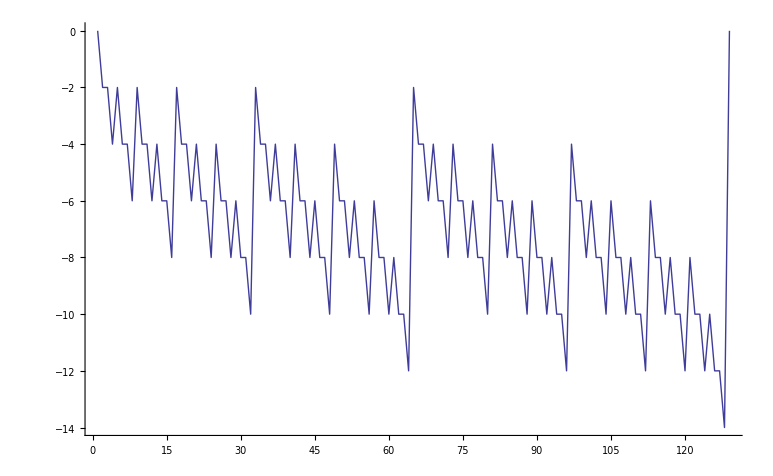

```mathematica
ListPlot[Table[sequ434[[k]]-8k+9,{k,129,257}],Joined->True]
```

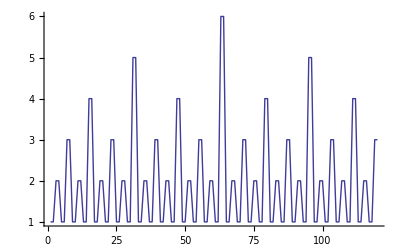

```mathematica
ListPlot[Table[IntegerExponent[2Ceiling[j/2],2],{j,120}],Joined->True]
```

```mathematica
2+Differences[Table[sequ434[[2^k]],{k,10}]]
```

{16,32,64,128,256,512,1024,2048,4096}

```mathematica
Differences[Table[sequ434[[2^k+1]],{k,10}]]
```

{16,32,64,128,256,512,1024,2048,4096}

```mathematica
Differences[Table[sequ434[[2^k+2]],{k,10}]]
```

{16,32,64,128,256,512,1024,2048,4096}

```mathematica
2+Differences[Table[sequ434[[2^k+3]],{k,10}]]
```

{16,34,66,130,258,514,1026,2050,4098}

```mathematica
FindSequenceFunction[Table[Differences[seqPos[liste3276,{4,3,4}],2][[2k-1]],{k,1,50}]]
```

FindSequenceFunction[{2,4,2,6,2,4,2,8,2,4,2,6,2,4,2,10,2,4,2,6,2,4,2,8,2,4,2,6,2,4,2,12,2,4,2,6,2,4,2,8,2,4,2,6,2,4,2,10,2,4}]

```mathematica
Differences[seqPos[liste3276,{4,3,4}],2]
```

{2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,10,-10,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,12,-12,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,10,-10,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,14,-14,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,10,-10,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,12,-12,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,10,-10,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,16,-16,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,10,-10,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,12,-12,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,10,-10,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,14,-14,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,10,-10,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,12,-12,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,10,-10,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,18,-18,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,10,-10,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,12,-12,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,10,-10,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,14,-14,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,10,-10,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,12,-12,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,10,-10,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,16,-16,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,10,-10,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,12,-12,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,10,-10,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,14,-14,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,10,-10,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,12,-12,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,10,-10,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,20,-20,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,10,-10,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,12,-12,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,10,-10,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,14,-14,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,10,-10,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,12,-12,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,10,-10,2,-2}

```mathematica
seqPos[liste3276,{4,6,3,1}]+1
```

{4,18,34,48,66,80,96,110,130,144,160,174,192,206,222,236,258,272,288,302,320,334,350,364,384,398,414,428,446,460,476,490,514,528,544,558,576,590,606,620,640,654,670,684,702,716,732,746,768,782,798,812,830,844,860,874,894,908,924,938,956,970,986,1000,1026,1040,1056,1070,1088,1102,1118,1132,1152,1166,1182,1196,1214,1228,1244,1258,1280,1294,1310,1324,1342,1356,1372,1386,1406,1420,1436,1450,1468,1482,1498,1512,1536,1550,1566,1580,1598,1612,1628,1642,1662,1676,1692,1706,1724,1738,1754,1768,1790,1804,1820,1834,1852,1866,1882,1896,1916,1930,1946,1960,1978,1992,2008,2022,2050,2064,2080,2094,2112,2126,2142,2156,2176,2190,2206,2220,2238,2252,2268,2282,2304,2318,2334,2348,2366,2380,2396,2410,2430,2444,2460,2474,2492,2506,2522,2536,2560,2574,2590,2604,2622,2636,2652,2666,2686,2700,2716,2730,2748,2762,2778,2792,2814,2828,2844,2858,2876,2890,2906,2920,2940,2954,2970,2984,3002,3016,3032,3046,3072,3086,3102,3116,3134,3148,3164,3178,3198,3212,3228,3242,3260,3274,3290,3304,3326,3340,3356,3370,3388,3402,3418,3432,3452,3466,3482,3496,3514,3528,3544,3558,3582,3596,3612,3626,3644,3658,3674,3688,3708,3722,3738,3752,3770,3784,3800,3814,3836,3850,3866,3880,3898,3912,3928,3942,3962,3976,3992,4006,4024,4038,4054,4068,4098,4112,4128,4142,4160,4174,4190,4204,4224,4238,4254,4268,4286,4300,4316,4330,4352,4366,4382,4396,4414,4428,4444,4458,4478,4492,4508,4522,4540,4554,4570,4584,4608,4622,4638,4652,4670,4684,4700,4714,4734,4748,4764,4778,4796,4810,4826,4840,4862,4876,4892,4906,4924,4938,4954,4968,4988}

```mathematica
FindSequenceFunction[Take[seqPos[liste3276,{4,6,3,1}]+1,10]-Take[seqPos[liste3276,{4,3,4}],10],m]
```

-5+8 m

```mathematica
FindSequenceFunction[Take[seqPos[liste3276,{4,6,6,6,6,6,6,6,3,1}]+1,10]-Take[seqPos[liste3276,{4,3,4}],10],m]
```

-521+1016 m

```mathematica
FindSequenceFunction[{15,33,67,133,263,521},k]
```

-3+2^(3+k)+2 k

```mathematica
Clear[n];
```

```mathematica
Table[(2^(m+4)-8)n-(2^(m+3)+2m-3),{m,0,6}]
```

{-5+8 n,-15+24 n,-33+56 n,-67+120 n,-133+248 n,-263+504 n,-521+1016 n}

```mathematica
Differences[seqPos[liste3276,{4,6,3,1}]+1]
```

{14,16,14,18,14,16,14,20,14,16,14,18,14,16,14,22,14,16,14,18,14,16,14,20,14,16,14,18,14,16,14,24,14,16,14,18,14,16,14,20,14,16,14,18,14,16,14,22,14,16,14,18,14,16,14,20,14,16,14,18,14,16,14,26,14,16,14,18,14,16,14,20,14,16,14,18,14,16,14,22,14,16,14,18,14,16,14,20,14,16,14,18,14,16,14,24,14,16,14,18,14,16,14,20,14,16,14,18,14,16,14,22,14,16,14,18,14,16,14,20,14,16,14,18,14,16,14,28,14,16,14,18,14,16,14,20,14,16,14,18,14,16,14,22,14,16,14,18,14,16,14,20,14,16,14,18,14,16,14,24,14,16,14,18,14,16,14,20,14,16,14,18,14,16,14,22,14,16,14,18,14,16,14,20,14,16,14,18,14,16,14,26,14,16,14,18,14,16,14,20,14,16,14,18,14,16,14,22,14,16,14,18,14,16,14,20,14,16,14,18,14,16,14,24,14,16,14,18,14,16,14,20,14,16,14,18,14,16,14,22,14,16,14,18,14,16,14,20,14,16,14,18,14,16,14,30,14,16,14,18,14,16,14,20,14,16,14,18,14,16,14,22,14,16,14,18,14,16,14,20,14,16,14,18,14,16,14,24,14,16,14,18,14,16,14,20,14,16,14,18,14,16,14,22,14,16,14,18,14,16,14,20}

```mathematica
Differences[seqPos[liste3276,{4,6,3,1}]+1,2]
```

{2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,10,-10,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,12,-12,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,10,-10,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,14,-14,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,10,-10,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,12,-12,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,10,-10,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,16,-16,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,10,-10,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6}

```mathematica
seqPos[liste3276,{4,6,6,3}]+1
```

{10,40,72,102,136,166,198,228,264,294,326,356,390,420,452,482,520,550,582,612,646,676,708,738,774,804,836,866,900,930,962,992,1032,1062,1094,1124,1158,1188,1220,1250,1286,1316,1348,1378,1412,1442,1474,1504,1542,1572,1604,1634,1668,1698,1730,1760,1796,1826,1858,1888,1922,1952,1984,2014,2056,2086,2118,2148,2182,2212,2244,2274,2310,2340,2372,2402,2436,2466,2498,2528,2566,2596,2628,2658,2692,2722,2754,2784,2820,2850,2882,2912,2946,2976,3008,3038,3078,3108,3140,3170,3204,3234,3266,3296,3332,3362,3394,3424,3458,3488,3520,3550,3588,3618,3650,3680,3714,3744,3776,3806,3842,3872,3904,3934,3968,3998,4030,4060,4104,4134,4166,4196,4230,4260,4292,4322,4358,4388,4420,4450,4484,4514,4546,4576,4614,4644,4676,4706,4740,4770,4802,4832,4868,4898,4930,4960,4994}

```mathematica
Differences[seqPos[liste3276,{4,6,6,3}]+1]
```

{30,32,30,34,30,32,30,36,30,32,30,34,30,32,30,38,30,32,30,34,30,32,30,36,30,32,30,34,30,32,30,40,30,32,30,34,30,32,30,36,30,32,30,34,30,32,30,38,30,32,30,34,30,32,30,36,30,32,30,34,30,32,30,42,30,32,30,34,30,32,30,36,30,32,30,34,30,32,30,38,30,32,30,34,30,32,30,36,30,32,30,34,30,32,30,40,30,32,30,34,30,32,30,36,30,32,30,34,30,32,30,38,30,32,30,34,30,32,30,36,30,32,30,34,30,32,30,44,30,32,30,34,30,32,30,36,30,32,30,34,30,32,30,38,30,32,30,34,30,32,30,36,30,32,30,34}

```mathematica
Differences[seqPos[liste3276,{4,6,6,3}]+1,2]
```

{2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,10,-10,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,12,-12,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,10,-10,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,14,-14,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4}

```mathematica
seqPos[liste3276,{4,6,6,6,3}]+1
```

{24,86,150,212,278,340,404,466,534,596,660,722,788,850,914,976,1046,1108,1172,1234,1300,1362,1426,1488,1556,1618,1682,1744,1810,1872,1936,1998,2070,2132,2196,2258,2324,2386,2450,2512,2580,2642,2706,2768,2834,2896,2960,3022,3092,3154,3218,3280,3346,3408,3472,3534,3602,3664,3728,3790,3856,3918,3982,4044,4118,4180,4244,4306,4372,4434,4498,4560,4628,4690,4754,4816,4882,4944}

```mathematica
Differences[seqPos[liste3276,{4,6,6,6,3}]+1]
```

{62,64,62,66,62,64,62,68,62,64,62,66,62,64,62,70,62,64,62,66,62,64,62,68,62,64,62,66,62,64,62,72,62,64,62,66,62,64,62,68,62,64,62,66,62,64,62,70,62,64,62,66,62,64,62,68,62,64,62,66,62,64,62,74,62,64,62,66,62,64,62,68,62,64,62,66,62}

```mathematica
Differences[seqPos[liste3276,{4,6,6,6,3}]+1,2]
```

{2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,10,-10,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,12,-12,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4}

```mathematica
seqPos[liste3276,{4,6,6,6,6,3}]+1
```

{54,180,308,434,564,690,818,944,1076,1202,1330,1456,1586,1712,1840,1966,2100,2226,2354,2480,2610,2736,2864,2990,3122,3248,3376,3502,3632,3758,3886,4012,4148,4274,4402,4528,4658,4784,4912}

```mathematica
seqPos[liste3276,{4,6,6,6,6,6,3}]+1
```

{116,370,626,880,1138,1392,1648,1902,2162,2416,2672,2926,3184,3438,3694,3948,4210,4464,4720,4974}

```mathematica
Differences[seqPos[liste3276,{4,6,6,6,6,6,3}]+1]
```

{254,256,254,258,254,256,254,260,254,256,254,258,254,256,254,262,254,256,254}

```mathematica
Differences[seqPos[liste3276,{4,6,6,6,6,6,3}]+1,2]
```

{2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2}

```mathematica
seqPos[liste3276,{4,6,6,6,6,6,6,3}]+1
```

{242,752,1264,1774,2288,2798,3310,3820,4336,4846}

```mathematica
Take[{2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,10,-10,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,12,-12,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,10,-10,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,14,-14,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,10,-10,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,12,-12,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,10,-10,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,16,-16,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,10,-10,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,12,-12,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,10,-10,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,14,-14,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,10,-10,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,12,-12,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,10,-10,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,18,-18,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,10,-10,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,12,-12,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,10,-10,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8},311]=={2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,10,-10,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,12,-12,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,10,-10,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,14,-14,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,10,-10,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,12,-12,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,10,-10,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,16,-16,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,10,-10,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6}
```

True

```mathematica
Length[{2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,10,-10,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,12,-12,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,10,-10,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,14,-14,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,10,-10,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,12,-12,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,10,-10,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,16,-16,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,10,-10,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6}]
```

311

```mathematica
seconddiff={2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,10,-10,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,12,-12,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,10,-10,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,14,-14,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,10,-10,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,12,-12,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,10,-10,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,16,-16,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,10,-10,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,12,-12,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,10,-10,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,14,-14,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,10,-10,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,12,-12,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,10,-10,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,18,-18,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,10,-10,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,12,-12,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,10,-10,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8};
```

```mathematica
Table[seconddiff[[2k-1]],{k,300}]
```

{2,4,2,6,2,4,2,8,2,4,2,6,2,4,2,10,2,4,2,6,2,4,2,8,2,4,2,6,2,4,2,12,2,4,2,6,2,4,2,8,2,4,2,6,2,4,2,10,2,4,2,6,2,4,2,8,2,4,2,6,2,4,2,14,2,4,2,6,2,4,2,8,2,4,2,6,2,4,2,10,2,4,2,6,2,4,2,8,2,4,2,6,2,4,2,12,2,4,2,6,2,4,2,8,2,4,2,6,2,4,2,10,2,4,2,6,2,4,2,8,2,4,2,6,2,4,2,16,2,4,2,6,2,4,2,8,2,4,2,6,2,4,2,10,2,4,2,6,2,4,2,8,2,4,2,6,2,4,2,12,2,4,2,6,2,4,2,8,2,4,2,6,2,4,2,10,2,4,2,6,2,4,2,8,2,4,2,6,2,4,2,14,2,4,2,6,2,4,2,8,2,4,2,6,2,4,2,10,2,4,2,6,2,4,2,8,2,4,2,6,2,4,2,12,2,4,2,6,2,4,2,8,2,4,2,6,2,4,2,10,2,4,2,6,2,4,2,8,2,4,2,6,2,4,2,18,2,4,2,6,2,4,2,8,2,4,2,6,2,4,2,10,2,4,2,6,2,4,2,8,2,4,2,6,2,4,2,12,2,4,2,6,2,4,2,8,2,4,2,6}

```mathematica
FindLinearRecurrence[Table[seconddiff[[2k-1]],{k,300}]]
```

FindLinearRecurrence[{2,4,2,6,2,4,2,8,2,4,2,6,2,4,2,10,2,4,2,6,2,4,2,8,2,4,2,6,2,4,2,12,2,4,2,6,2,4,2,8,2,4,2,6,2,4,2,10,2,4,2,6,2,4,2,8,2,4,2,6,2,4,2,14,2,4,2,6,2,4,2,8,2,4,2,6,2,4,2,10,2,4,2,6,2,4,2,8,2,4,2,6,2,4,2,12,2,4,2,6,2,4,2,8,2,4,2,6,2,4,2,10,2,4,2,6,2,4,2,8,2,4,2,6,2,4,2,16,2,4,2,6,2,4,2,8,2,4,2,6,2,4,2,10,2,4,2,6,2,4,2,8,2,4,2,6,2,4,2,12,2,4,2,6,2,4,2,8,2,4,2,6,2,4,2,10,2,4,2,6,2,4,2,8,2,4,2,6,2,4,2,14,2,4,2,6,2,4,2,8,2,4,2,6,2,4,2,10,2,4,2,6,2,4,2,8,2,4,2,6,2,4,2,12,2,4,2,6,2,4,2,8,2,4,2,6,2,4,2,10,2,4,2,6,2,4,2,8,2,4,2,6,2,4,2,18,2,4,2,6,2,4,2,8,2,4,2,6,2,4,2,10,2,4,2,6,2,4,2,8,2,4,2,6,2,4,2,12,2,4,2,6,2,4,2,8,2,4,2,6}]

```mathematica
seconddiff[[2^k(2m-1)-1/.{k->6,m->3}]]
```

12

```mathematica
{seconddiff[[287]],IntegerDigits[288,2],seconddiff[[288]]}
```

{10,{1,0,0,1,0,0,0,0,0},-10}

```mathematica
2IntegerExponent[288,2]
```

10

```mathematica
F[j_]:=(-1)^(j+1)2IntegerExponent[2Ceiling[j/2],2]    (*calcule seconddiff*)
```

```mathematica
{F[287],F[288]}
```

{10,-10}

```mathematica
Table[F[j],{j,50}]
```

{2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,10,-10,2,-2,4,-4,2,-2,6,-6,2,-2,4,-4,2,-2,8,-8,2,-2}

```mathematica
FindSequenceFunction[Flatten[Position[seconddiff,2]],m]
```

-3+4 m

```mathematica
FindSequenceFunction[Flatten[Position[seconddiff,4]],m]
```

-5+8 m

```mathematica
Table[FindSequenceFunction[Flatten[Position[seconddiff,2k]],m],{k,6}]
```

{-3+4 m,-5+8 m,-9+16 m,-17+32 m,-33+64 m,-65+128 m}

```mathematica
Flatten[Table[Position[seconddiff,2k][[1]],{k,6}]]
```

{1,3,7,15,31,63}

```mathematica
FindSequenceFunction[{1,3,7,15,31,63},n]
```

-1+2^n

```mathematica
Flatten[Table[Position[seconddiff,2k][[2]],{k,6}]]
```

{5,11,23,47,95,191}

```mathematica
FindSequenceFunction[{5,11,23,47,95,191},n]
```

-1+3 2^n

```mathematica
RSolve[{a[n+1]==2 a[n]-a[n-1]+2^(n-1),a[1]==2^n-1,a[2]==3 2^n-1},a[n],n]
```

{{a[n]→-1-2 n+2^(1+n) n}}

```mathematica
Table[-1-2 n+2^(1+n) n,{n,5}]
```

{1,11,41,119,309}

```mathematica
Flatten[Position[seconddiff,6]]
```

{7,23,39,55,71,87,103,119,135,151,167,183,199,215,231,247,263,279,295,311,327,343,359,375,391,407,423,439,455,471,487,503,519,535,551,567,583,599,615}

```mathematica
Differences[Flatten[Position[seconddiff,2]]]
```

{4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}

```mathematica
Differences[Flatten[Position[seconddiff,4]]]
```

{8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8}

```mathematica
Differences[Flatten[Position[seconddiff,6]]]
```

{16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16}

```mathematica
Differences[Flatten[Position[seconddiff,8]]]
```

{32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32}

```mathematica
Differences[Flatten[Position[seconddiff,10]]]
```

{64,64,64,64,64,64,64,64,64}

```mathematica
Sort[Flatten[Table[(2m-1)2^(k-1),{m,1,10},{k,1,5}]]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,22,24,26,28,30,34,36,38,40,44,48,52,56,60,68,72,76,80,88,104,112,120,136,144,152,176,208,240,272,304}

```mathematica
(4 5)^10
```

10240000000000

```mathematica
Base4SEvolution[5,9531397146,600]
```

{6,12,8,11,11,11,18,0,17,0,6,4,12,8,11,11,11,11,18,0,17,0,6,4,4,12,8,11,11,11,11,11,18,0,17,0,6,4,4,4,12,8,11,11,11,11,11,11,18,0,17,0,6,4,4,4,4,12,8,11,11,11,11,11,11,11,18,0,17,0,6,4,4,4,4,4,12,8,11,11,11,11,11,11,11,11,18,0,17,0,6,4,4,4,4,4,4,12,8,11,11,11,11,11,11,11,11,11,18,0,17,0,6,4,4,4,4,4,4,4,12,8,11,11,11,11,11,11,11,11,11,11,18,0,17,0,6,4,4,4,4,4,4,4,4,12,8,11,11,11,11,11,11,11,11,11,11,11,18,0,17,0,6,4,4,4,4,4,4,4,4,4,12,8,11,11,11,11,11,11,11,11,11,11,11,11,18,0,17,0,6,4,4,4,4,4,4,4,4,4,4,12,8,11,11,11,11,11,11,11,11,11,11,11,11,11,18,0,17,0,6,4,4,4,4,4,4,4,4,4,4,4,12,8,11,11,11,11,11,11,11,11,11,11,11,11,11,11,18,0,17,0,6,4,4,4,4,4,4,4,4,4,4,4,4,12,8,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,18,0,17,0,6,4,4,4,4,4,4,4,4,4,4,4,4,4,12,8,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,18,0,17,0,6,4,4,4,4,4,4,4,4,4,4,4,4,4,4,12,8,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,18,0,17,0,6,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,12,8,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,18,0,17,0,6,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,12,8,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,18,0,17,0,6,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,12,8,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,18,0,17,0,6,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,12,8,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,18,0,17,0,6,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,12,8,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,18,0,17,0,6,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}

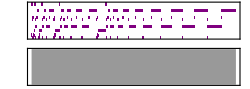

```mathematica
Sound[SoundNote[#]&/@Base4SEvolution[5,81627575424,600],50]
```

```mathematica
SBTM[5,81627575424,600]
```

-Graphics-

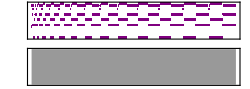

```mathematica
Sound[SoundNote[#]&/@Base4SEvolution[5,200894031406,600],150]
```

```mathematica
SBTM[5,200894031406,200]
```

-Graphics-

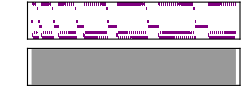

```mathematica
Sound[SoundNote[#]&/@Base4SEvolution[5,80282375310,300],50]
```

```mathematica
{SBTM[5,31935132106,200],SBTM[5,29730390108,200]}
```

{-Graphics-,-Graphics-}